```mathematica
SetDirectory[NotebookDirectory[]];
<<RTNI`
```

Package RTNI (Random Tensor Network Integrator) version 1.0.5 (last modification: 26/01/2019).

Loading precomputed Weingarten Functions from /precomputedWG/functions1.txt

Loading precomputed Weingarten Functions from /precomputedWG/functions2.txt

Loading precomputed Weingarten Functions from /precomputedWG/functions3.txt

Loading precomputed Weingarten Functions from /precomputedWG/functions4.txt

Loading precomputed Weingarten Functions from /precomputedWG/functions5.txt

Loading precomputed Weingarten Functions from /precomputedWG/functions6.txt

Loading precomputed Weingarten Functions from /precomputedWG/functions7.txt

Loading precomputed Weingarten Functions from /precomputedWG/functions8.txt

Loading precomputed Weingarten Functions from /precomputedWG/functions9.txt

Loading precomputed Weingarten Functions from /precomputedWG/functions10.txt

Loading precomputed Weingarten Functions from /precomputedWG/functions11.txt

Loading precomputed Weingarten Functions from /precomputedWG/functions12.txt

Loading precomputed Weingarten Functions from /precomputedWG/functions13.txt

Loading precomputed Weingarten Functions from /precomputedWG/functions14.txt

Loading precomputed Weingarten Functions from /precomputedWG/functions15.txt

Loading precomputed Weingarten Functions from /precomputedWG/functions16.txt

Loading precomputed Weingarten Functions from /precomputedWG/functions17.txt

Loading precomputed Weingarten Functions from /precomputedWG/functions18.txt

Loading precomputed Weingarten Functions from /precomputedWG/functions19.txt

Loading precomputed Weingarten Functions from /precomputedWG/functions20.txt

```mathematica
eWA= {{"W",1,"out",1},{"A",1,"in",1}};
eAWd = {{"A",1,"out",1},{"W*",1,"in",1}};
eWdB = {{"W*",1,"out",1},{"B",1,"in",1}};
eTR = {{"B",1,"out",1},{"W",1,"in",1}};
```

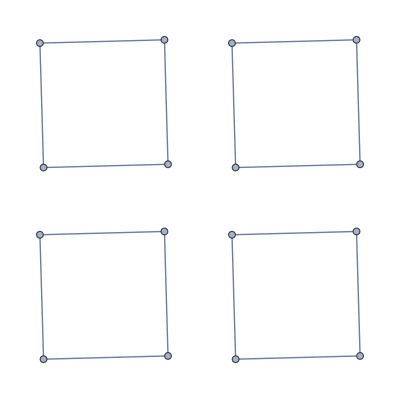
{{-Graphics-,1}}

```mathematica
eWC= {{"W",2,"out",1},{"A",2,"in",1}};
eCWd = {{"A",2,"out",1},{"W*",2,"in",1}};
eWdD = {{"W*",2,"out",1},{"B",2,"in",1}};
eTR2 = {{"B",2,"out",1},{"W",2,"in",1}};

eWE= {{"W",3,"out",1},{"A",3,"in",1}};
eEWd = {{"A",3,"out",1},{"W*",3,"in",1}};
eWdF = {{"W*",3,"out",1},{"B",3,"in",1}};
eTR3 = {{"B",3,"out",1},{"W",3,"in",1}};

eWG= {{"W",4,"out",1},{"A",4,"in",1}};
eGWd = {{"A",4,"out",1},{"W*",4,"in",1}};
eWdH = {{"W*",4,"out",1},{"B",4,"in",1}};
eTR4 = {{"B",4,"out",1},{"W",4,"in",1}};

t = {eWA,eAWd, eWdB, eTR,eWC,eCWd,eWdD,eTR2,eWE,eEWd,eWdF,eTR3,eWG,eGWd,eWdH,eTR4};
glist = {{t, 1}};
visualizeTN[glist]
```

```mathematica
Lemma6Sol = integrateHaarUnitary[glist,"W",{d},{d},d]
```

```mathematica
d->2
```

d→2

```mathematica
d
```

d

```mathematica
d=2
```

2

```mathematica
Out[24]
```

Power::infy: 碰到无穷表达式 1/0.

General::stop: 在本次计算中，Power::infy 的进一步输出将被抑制.

{{{{{B,1,out,1},{B,1,in,1}},{{B,2,out,1},{B,2,in,1}},{{B,3,out,1},{B,3,in,1}},{{B,4,out,1},{B,4,in,1}},{{A,1,in,1},{A,1,out,1}},{{A,2,in,1},{A,2,out,1}},{{A,3,in,1},{A,3,out,1}},{{A,4,in,1},{A,4,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,1,in,1}},{{B,2,out,1},{B,2,in,1}},{{B,3,out,1},{B,3,in,1}},{{B,4,out,1},{B,4,in,1}},{{A,1,in,1},{A,1,out,1}},{{A,2,in,1},{A,2,out,1}},{{A,3,in,1},{A,4,out,1}},{{A,4,in,1},{A,3,out,1}}},1/30},{{{{B,1,out,1},{B,1,in,1}},{{B,2,out,1},{B,2,in,1}},{{B,3,out,1},{B,3,in,1}},{{B,4,out,1},{B,4,in,1}},{{A,1,in,1},{A,1,out,1}},{{A,2,in,1},{A,3,out,1}},{{A,3,in,1},{A,2,out,1}},{{A,4,in,1},{A,4,out,1}}},1/30},{{{{B,1,out,1},{B,1,in,1}},{{B,2,out,1},{B,2,in,1}},{{B,3,out,1},{B,3,in,1}},{{B,4,out,1},{B,4,in,1}},{{A,1,in,1},{A,1,out,1}},{{A,2,in,1},{A,3,out,1}},{{A,3,in,1},{A,4,out,1}},{{A,4,in,1},{A,2,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,1,in,1}},{{B,2,out,1},{B,2,in,1}},{{B,3,out,1},{B,3,in,1}},{{B,4,out,1},{B,4,in,1}},{{A,1,in,1},{A,1,out,1}},{{A,2,in,1},{A,4,out,1}},{{A,3,in,1},{A,2,out,1}},{{A,4,in,1},{A,3,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,1,in,1}},{{B,2,out,1},{B,2,in,1}},{{B,3,out,1},{B,3,in,1}},{{B,4,out,1},{B,4,in,1}},{{A,1,in,1},{A,1,out,1}},{{A,2,in,1},{A,4,out,1}},{{A,3,in,1},{A,3,out,1}},{{A,4,in,1},{A,2,out,1}}},1/30},{{{{B,1,out,1},{B,1,in,1}},{{B,2,out,1},{B,2,in,1}},{{B,3,out,1},{B,3,in,1}},{{B,4,out,1},{B,4,in,1}},{{A,1,in,1},{A,2,out,1}},{{A,2,in,1},{A,1,out,1}},{{A,3,in,1},{A,3,out,1}},{{A,4,in,1},{A,4,out,1}}},1/30},{{{{B,1,out,1},{B,1,in,1}},{{B,2,out,1},{B,2,in,1}},{{B,3,out,1},{B,3,in,1}},{{B,4,out,1},{B,4,in,1}},{{A,1,in,1},{A,2,out,1}},{{A,2,in,1},{A,1,out,1}},{{A,3,in,1},{A,4,out,1}},{{A,4,in,1},{A,3,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,1,in,1}},{{B,2,out,1},{B,2,in,1}},{{B,3,out,1},{B,3,in,1}},{{B,4,out,1},{B,4,in,1}},{{A,1,in,1},{A,2,out,1}},{{A,2,in,1},{A,3,out,1}},{{A,3,in,1},{A,1,out,1}},{{A,4,in,1},{A,4,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,1,in,1}},{{B,2,out,1},{B,2,in,1}},{{B,3,out,1},{B,3,in,1}},{{B,4,out,1},{B,4,in,1}},{{A,1,in,1},{A,2,out,1}},{{A,2,in,1},{A,3,out,1}},{{A,3,in,1},{A,4,out,1}},{{A,4,in,1},{A,1,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,1,in,1}},{{B,2,out,1},{B,2,in,1}},{{B,3,out,1},{B,3,in,1}},{{B,4,out,1},{B,4,in,1}},{{A,1,in,1},{A,2,out,1}},{{A,2,in,1},{A,4,out,1}},{{A,3,in,1},{A,1,out,1}},{{A,4,in,1},{A,3,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,1,in,1}},{{B,2,out,1},{B,2,in,1}},{{B,3,out,1},{B,3,in,1}},{{B,4,out,1},{B,4,in,1}},{{A,1,in,1},{A,2,out,1}},{{A,2,in,1},{A,4,out,1}},{{A,3,in,1},{A,3,out,1}},{{A,4,in,1},{A,1,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,1,in,1}},{{B,2,out,1},{B,2,in,1}},{{B,3,out,1},{B,3,in,1}},{{B,4,out,1},{B,4,in,1}},{{A,1,in,1},{A,3,out,1}},{{A,2,in,1},{A,1,out,1}},{{A,3,in,1},{A,2,out,1}},{{A,4,in,1},{A,4,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,1,in,1}},{{B,2,out,1},{B,2,in,1}},{{B,3,out,1},{B,3,in,1}},{{B,4,out,1},{B,4,in,1}},{{A,1,in,1},{A,3,out,1}},{{A,2,in,1},{A,1,out,1}},{{A,3,in,1},{A,4,out,1}},{{A,4,in,1},{A,2,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,1,in,1}},{{B,2,out,1},{B,2,in,1}},{{B,3,out,1},{B,3,in,1}},{{B,4,out,1},{B,4,in,1}},{{A,1,in,1},{A,3,out,1}},{{A,2,in,1},{A,2,out,1}},{{A,3,in,1},{A,1,out,1}},{{A,4,in,1},{A,4,out,1}}},1/30},{{{{B,1,out,1},{B,1,in,1}},{{B,2,out,1},{B,2,in,1}},{{B,3,out,1},{B,3,in,1}},{{B,4,out,1},{B,4,in,1}},{{A,1,in,1},{A,3,out,1}},{{A,2,in,1},{A,2,out,1}},{{A,3,in,1},{A,4,out,1}},{{A,4,in,1},{A,1,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,1,in,1}},{{B,2,out,1},{B,2,in,1}},{{B,3,out,1},{B,3,in,1}},{{B,4,out,1},{B,4,in,1}},{{A,1,in,1},{A,3,out,1}},{{A,2,in,1},{A,4,out,1}},{{A,3,in,1},{A,1,out,1}},{{A,4,in,1},{A,2,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,1,in,1}},{{B,2,out,1},{B,2,in,1}},{{B,3,out,1},{B,3,in,1}},{{B,4,out,1},{B,4,in,1}},{{A,1,in,1},{A,3,out,1}},{{A,2,in,1},{A,4,out,1}},{{A,3,in,1},{A,2,out,1}},{{A,4,in,1},{A,1,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,1,in,1}},{{B,2,out,1},{B,2,in,1}},{{B,3,out,1},{B,3,in,1}},{{B,4,out,1},{B,4,in,1}},{{A,1,in,1},{A,4,out,1}},{{A,2,in,1},{A,1,out,1}},{{A,3,in,1},{A,2,out,1}},{{A,4,in,1},{A,3,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,1,in,1}},{{B,2,out,1},{B,2,in,1}},{{B,3,out,1},{B,3,in,1}},{{B,4,out,1},{B,4,in,1}},{{A,1,in,1},{A,4,out,1}},{{A,2,in,1},{A,1,out,1}},{{A,3,in,1},{A,3,out,1}},{{A,4,in,1},{A,2,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,1,in,1}},{{B,2,out,1},{B,2,in,1}},{{B,3,out,1},{B,3,in,1}},{{B,4,out,1},{B,4,in,1}},{{A,1,in,1},{A,4,out,1}},{{A,2,in,1},{A,2,out,1}},{{A,3,in,1},{A,1,out,1}},{{A,4,in,1},{A,3,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,1,in,1}},{{B,2,out,1},{B,2,in,1}},{{B,3,out,1},{B,3,in,1}},{{B,4,out,1},{B,4,in,1}},{{A,1,in,1},{A,4,out,1}},{{A,2,in,1},{A,2,out,1}},{{A,3,in,1},{A,3,out,1}},{{A,4,in,1},{A,1,out,1}}},1/30},{{{{B,1,out,1},{B,1,in,1}},{{B,2,out,1},{B,2,in,1}},{{B,3,out,1},{B,3,in,1}},{{B,4,out,1},{B,4,in,1}},{{A,1,in,1},{A,4,out,1}},{{A,2,in,1},{A,3,out,1}},{{A,3,in,1},{A,1,out,1}},{{A,4,in,1},{A,2,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,1,in,1}},{{B,2,out,1},{B,2,in,1}},{{B,3,out,1},{B,3,in,1}},{{B,4,out,1},{B,4,in,1}},{{A,1,in,1},{A,4,out,1}},{{A,2,in,1},{A,3,out,1}},{{A,3,in,1},{A,2,out,1}},{{A,4,in,1},{A,1,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,1,in,1}},{{B,2,out,1},{B,2,in,1}},{{B,3,out,1},{B,4,in,1}},{{B,4,out,1},{B,3,in,1}},{{A,1,in,1},{A,1,out,1}},{{A,2,in,1},{A,2,out,1}},{{A,3,in,1},{A,3,out,1}},{{A,4,in,1},{A,4,out,1}}},1/30},{{{{B,1,out,1},{B,1,in,1}},{{B,2,out,1},{B,2,in,1}},{{B,3,out,1},{B,4,in,1}},{{B,4,out,1},{B,3,in,1}},{{A,1,in,1},{A,1,out,1}},{{A,2,in,1},{A,2,out,1}},{{A,3,in,1},{A,4,out,1}},{{A,4,in,1},{A,3,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,1,in,1}},{{B,2,out,1},{B,2,in,1}},{{B,3,out,1},{B,4,in,1}},{{B,4,out,1},{B,3,in,1}},{{A,1,in,1},{A,1,out,1}},{{A,2,in,1},{A,3,out,1}},{{A,3,in,1},{A,2,out,1}},{{A,4,in,1},{A,4,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,1,in,1}},{{B,2,out,1},{B,2,in,1}},{{B,3,out,1},{B,4,in,1}},{{B,4,out,1},{B,3,in,1}},{{A,1,in,1},{A,1,out,1}},{{A,2,in,1},{A,3,out,1}},{{A,3,in,1},{A,4,out,1}},{{A,4,in,1},{A,2,out,1}}},1/30},{{{{B,1,out,1},{B,1,in,1}},{{B,2,out,1},{B,2,in,1}},{{B,3,out,1},{B,4,in,1}},{{B,4,out,1},{B,3,in,1}},{{A,1,in,1},{A,1,out,1}},{{A,2,in,1},{A,4,out,1}},{{A,3,in,1},{A,2,out,1}},{{A,4,in,1},{A,3,out,1}}},1/30},{{{{B,1,out,1},{B,1,in,1}},{{B,2,out,1},{B,2,in,1}},{{B,3,out,1},{B,4,in,1}},{{B,4,out,1},{B,3,in,1}},{{A,1,in,1},{A,1,out,1}},{{A,2,in,1},{A,4,out,1}},{{A,3,in,1},{A,3,out,1}},{{A,4,in,1},{A,2,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,1,in,1}},{{B,2,out,1},{B,2,in,1}},{{B,3,out,1},{B,4,in,1}},{{B,4,out,1},{B,3,in,1}},{{A,1,in,1},{A,2,out,1}},{{A,2,in,1},{A,1,out,1}},{{A,3,in,1},{A,3,out,1}},{{A,4,in,1},{A,4,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,1,in,1}},{{B,2,out,1},{B,2,in,1}},{{B,3,out,1},{B,4,in,1}},{{B,4,out,1},{B,3,in,1}},{{A,1,in,1},{A,2,out,1}},{{A,2,in,1},{A,1,out,1}},{{A,3,in,1},{A,4,out,1}},{{A,4,in,1},{A,3,out,1}}},1/30},{{{{B,1,out,1},{B,1,in,1}},{{B,2,out,1},{B,2,in,1}},{{B,3,out,1},{B,4,in,1}},{{B,4,out,1},{B,3,in,1}},{{A,1,in,1},{A,2,out,1}},{{A,2,in,1},{A,3,out,1}},{{A,3,in,1},{A,1,out,1}},{{A,4,in,1},{A,4,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,1,in,1}},{{B,2,out,1},{B,2,in,1}},{{B,3,out,1},{B,4,in,1}},{{B,4,out,1},{B,3,in,1}},{{A,1,in,1},{A,2,out,1}},{{A,2,in,1},{A,3,out,1}},{{A,3,in,1},{A,4,out,1}},{{A,4,in,1},{A,1,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,1,in,1}},{{B,2,out,1},{B,2,in,1}},{{B,3,out,1},{B,4,in,1}},{{B,4,out,1},{B,3,in,1}},{{A,1,in,1},{A,2,out,1}},{{A,2,in,1},{A,4,out,1}},{{A,3,in,1},{A,1,out,1}},{{A,4,in,1},{A,3,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,1,in,1}},{{B,2,out,1},{B,2,in,1}},{{B,3,out,1},{B,4,in,1}},{{B,4,out,1},{B,3,in,1}},{{A,1,in,1},{A,2,out,1}},{{A,2,in,1},{A,4,out,1}},{{A,3,in,1},{A,3,out,1}},{{A,4,in,1},{A,1,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,1,in,1}},{{B,2,out,1},{B,2,in,1}},{{B,3,out,1},{B,4,in,1}},{{B,4,out,1},{B,3,in,1}},{{A,1,in,1},{A,3,out,1}},{{A,2,in,1},{A,1,out,1}},{{A,3,in,1},{A,2,out,1}},{{A,4,in,1},{A,4,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,1,in,1}},{{B,2,out,1},{B,2,in,1}},{{B,3,out,1},{B,4,in,1}},{{B,4,out,1},{B,3,in,1}},{{A,1,in,1},{A,3,out,1}},{{A,2,in,1},{A,1,out,1}},{{A,3,in,1},{A,4,out,1}},{{A,4,in,1},{A,2,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,1,in,1}},{{B,2,out,1},{B,2,in,1}},{{B,3,out,1},{B,4,in,1}},{{B,4,out,1},{B,3,in,1}},{{A,1,in,1},{A,3,out,1}},{{A,2,in,1},{A,2,out,1}},{{A,3,in,1},{A,1,out,1}},{{A,4,in,1},{A,4,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,1,in,1}},{{B,2,out,1},{B,2,in,1}},{{B,3,out,1},{B,4,in,1}},{{B,4,out,1},{B,3,in,1}},{{A,1,in,1},{A,3,out,1}},{{A,2,in,1},{A,2,out,1}},{{A,3,in,1},{A,4,out,1}},{{A,4,in,1},{A,1,out,1}}},1/30},{{{{B,1,out,1},{B,1,in,1}},{{B,2,out,1},{B,2,in,1}},{{B,3,out,1},{B,4,in,1}},{{B,4,out,1},{B,3,in,1}},{{A,1,in,1},{A,3,out,1}},{{A,2,in,1},{A,4,out,1}},{{A,3,in,1},{A,1,out,1}},{{A,4,in,1},{A,2,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,1,in,1}},{{B,2,out,1},{B,2,in,1}},{{B,3,out,1},{B,4,in,1}},{{B,4,out,1},{B,3,in,1}},{{A,1,in,1},{A,3,out,1}},{{A,2,in,1},{A,4,out,1}},{{A,3,in,1},{A,2,out,1}},{{A,4,in,1},{A,1,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,1,in,1}},{{B,2,out,1},{B,2,in,1}},{{B,3,out,1},{B,4,in,1}},{{B,4,out,1},{B,3,in,1}},{{A,1,in,1},{A,4,out,1}},{{A,2,in,1},{A,1,out,1}},{{A,3,in,1},{A,2,out,1}},{{A,4,in,1},{A,3,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,1,in,1}},{{B,2,out,1},{B,2,in,1}},{{B,3,out,1},{B,4,in,1}},{{B,4,out,1},{B,3,in,1}},{{A,1,in,1},{A,4,out,1}},{{A,2,in,1},{A,1,out,1}},{{A,3,in,1},{A,3,out,1}},{{A,4,in,1},{A,2,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,1,in,1}},{{B,2,out,1},{B,2,in,1}},{{B,3,out,1},{B,4,in,1}},{{B,4,out,1},{B,3,in,1}},{{A,1,in,1},{A,4,out,1}},{{A,2,in,1},{A,2,out,1}},{{A,3,in,1},{A,1,out,1}},{{A,4,in,1},{A,3,out,1}}},1/30},{{{{B,1,out,1},{B,1,in,1}},{{B,2,out,1},{B,2,in,1}},{{B,3,out,1},{B,4,in,1}},{{B,4,out,1},{B,3,in,1}},{{A,1,in,1},{A,4,out,1}},{{A,2,in,1},{A,2,out,1}},{{A,3,in,1},{A,3,out,1}},{{A,4,in,1},{A,1,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,1,in,1}},{{B,2,out,1},{B,2,in,1}},{{B,3,out,1},{B,4,in,1}},{{B,4,out,1},{B,3,in,1}},{{A,1,in,1},{A,4,out,1}},{{A,2,in,1},{A,3,out,1}},{{A,3,in,1},{A,1,out,1}},{{A,4,in,1},{A,2,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,1,in,1}},{{B,2,out,1},{B,2,in,1}},{{B,3,out,1},{B,4,in,1}},{{B,4,out,1},{B,3,in,1}},{{A,1,in,1},{A,4,out,1}},{{A,2,in,1},{A,3,out,1}},{{A,3,in,1},{A,2,out,1}},{{A,4,in,1},{A,1,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,1,in,1}},{{B,2,out,1},{B,3,in,1}},{{B,3,out,1},{B,2,in,1}},{{B,4,out,1},{B,4,in,1}},{{A,1,in,1},{A,1,out,1}},{{A,2,in,1},{A,2,out,1}},{{A,3,in,1},{A,3,out,1}},{{A,4,in,1},{A,4,out,1}}},1/30},{{{{B,1,out,1},{B,1,in,1}},{{B,2,out,1},{B,3,in,1}},{{B,3,out,1},{B,2,in,1}},{{B,4,out,1},{B,4,in,1}},{{A,1,in,1},{A,1,out,1}},{{A,2,in,1},{A,2,out,1}},{{A,3,in,1},{A,4,out,1}},{{A,4,in,1},{A,3,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,1,in,1}},{{B,2,out,1},{B,3,in,1}},{{B,3,out,1},{B,2,in,1}},{{B,4,out,1},{B,4,in,1}},{{A,1,in,1},{A,1,out,1}},{{A,2,in,1},{A,3,out,1}},{{A,3,in,1},{A,2,out,1}},{{A,4,in,1},{A,4,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,1,in,1}},{{B,2,out,1},{B,3,in,1}},{{B,3,out,1},{B,2,in,1}},{{B,4,out,1},{B,4,in,1}},{{A,1,in,1},{A,1,out,1}},{{A,2,in,1},{A,3,out,1}},{{A,3,in,1},{A,4,out,1}},{{A,4,in,1},{A,2,out,1}}},1/30},{{{{B,1,out,1},{B,1,in,1}},{{B,2,out,1},{B,3,in,1}},{{B,3,out,1},{B,2,in,1}},{{B,4,out,1},{B,4,in,1}},{{A,1,in,1},{A,1,out,1}},{{A,2,in,1},{A,4,out,1}},{{A,3,in,1},{A,2,out,1}},{{A,4,in,1},{A,3,out,1}}},1/30},{{{{B,1,out,1},{B,1,in,1}},{{B,2,out,1},{B,3,in,1}},{{B,3,out,1},{B,2,in,1}},{{B,4,out,1},{B,4,in,1}},{{A,1,in,1},{A,1,out,1}},{{A,2,in,1},{A,4,out,1}},{{A,3,in,1},{A,3,out,1}},{{A,4,in,1},{A,2,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,1,in,1}},{{B,2,out,1},{B,3,in,1}},{{B,3,out,1},{B,2,in,1}},{{B,4,out,1},{B,4,in,1}},{{A,1,in,1},{A,2,out,1}},{{A,2,in,1},{A,1,out,1}},{{A,3,in,1},{A,3,out,1}},{{A,4,in,1},{A,4,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,1,in,1}},{{B,2,out,1},{B,3,in,1}},{{B,3,out,1},{B,2,in,1}},{{B,4,out,1},{B,4,in,1}},{{A,1,in,1},{A,2,out,1}},{{A,2,in,1},{A,1,out,1}},{{A,3,in,1},{A,4,out,1}},{{A,4,in,1},{A,3,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,1,in,1}},{{B,2,out,1},{B,3,in,1}},{{B,3,out,1},{B,2,in,1}},{{B,4,out,1},{B,4,in,1}},{{A,1,in,1},{A,2,out,1}},{{A,2,in,1},{A,3,out,1}},{{A,3,in,1},{A,1,out,1}},{{A,4,in,1},{A,4,out,1}}},1/30},{{{{B,1,out,1},{B,1,in,1}},{{B,2,out,1},{B,3,in,1}},{{B,3,out,1},{B,2,in,1}},{{B,4,out,1},{B,4,in,1}},{{A,1,in,1},{A,2,out,1}},{{A,2,in,1},{A,3,out,1}},{{A,3,in,1},{A,4,out,1}},{{A,4,in,1},{A,1,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,1,in,1}},{{B,2,out,1},{B,3,in,1}},{{B,3,out,1},{B,2,in,1}},{{B,4,out,1},{B,4,in,1}},{{A,1,in,1},{A,2,out,1}},{{A,2,in,1},{A,4,out,1}},{{A,3,in,1},{A,1,out,1}},{{A,4,in,1},{A,3,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,1,in,1}},{{B,2,out,1},{B,3,in,1}},{{B,3,out,1},{B,2,in,1}},{{B,4,out,1},{B,4,in,1}},{{A,1,in,1},{A,2,out,1}},{{A,2,in,1},{A,4,out,1}},{{A,3,in,1},{A,3,out,1}},{{A,4,in,1},{A,1,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,1,in,1}},{{B,2,out,1},{B,3,in,1}},{{B,3,out,1},{B,2,in,1}},{{B,4,out,1},{B,4,in,1}},{{A,1,in,1},{A,3,out,1}},{{A,2,in,1},{A,1,out,1}},{{A,3,in,1},{A,2,out,1}},{{A,4,in,1},{A,4,out,1}}},1/30},{{{{B,1,out,1},{B,1,in,1}},{{B,2,out,1},{B,3,in,1}},{{B,3,out,1},{B,2,in,1}},{{B,4,out,1},{B,4,in,1}},{{A,1,in,1},{A,3,out,1}},{{A,2,in,1},{A,1,out,1}},{{A,3,in,1},{A,4,out,1}},{{A,4,in,1},{A,2,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,1,in,1}},{{B,2,out,1},{B,3,in,1}},{{B,3,out,1},{B,2,in,1}},{{B,4,out,1},{B,4,in,1}},{{A,1,in,1},{A,3,out,1}},{{A,2,in,1},{A,2,out,1}},{{A,3,in,1},{A,1,out,1}},{{A,4,in,1},{A,4,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,1,in,1}},{{B,2,out,1},{B,3,in,1}},{{B,3,out,1},{B,2,in,1}},{{B,4,out,1},{B,4,in,1}},{{A,1,in,1},{A,3,out,1}},{{A,2,in,1},{A,2,out,1}},{{A,3,in,1},{A,4,out,1}},{{A,4,in,1},{A,1,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,1,in,1}},{{B,2,out,1},{B,3,in,1}},{{B,3,out,1},{B,2,in,1}},{{B,4,out,1},{B,4,in,1}},{{A,1,in,1},{A,3,out,1}},{{A,2,in,1},{A,4,out,1}},{{A,3,in,1},{A,1,out,1}},{{A,4,in,1},{A,2,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,1,in,1}},{{B,2,out,1},{B,3,in,1}},{{B,3,out,1},{B,2,in,1}},{{B,4,out,1},{B,4,in,1}},{{A,1,in,1},{A,3,out,1}},{{A,2,in,1},{A,4,out,1}},{{A,3,in,1},{A,2,out,1}},{{A,4,in,1},{A,1,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,1,in,1}},{{B,2,out,1},{B,3,in,1}},{{B,3,out,1},{B,2,in,1}},{{B,4,out,1},{B,4,in,1}},{{A,1,in,1},{A,4,out,1}},{{A,2,in,1},{A,1,out,1}},{{A,3,in,1},{A,2,out,1}},{{A,4,in,1},{A,3,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,1,in,1}},{{B,2,out,1},{B,3,in,1}},{{B,3,out,1},{B,2,in,1}},{{B,4,out,1},{B,4,in,1}},{{A,1,in,1},{A,4,out,1}},{{A,2,in,1},{A,1,out,1}},{{A,3,in,1},{A,3,out,1}},{{A,4,in,1},{A,2,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,1,in,1}},{{B,2,out,1},{B,3,in,1}},{{B,3,out,1},{B,2,in,1}},{{B,4,out,1},{B,4,in,1}},{{A,1,in,1},{A,4,out,1}},{{A,2,in,1},{A,2,out,1}},{{A,3,in,1},{A,1,out,1}},{{A,4,in,1},{A,3,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,1,in,1}},{{B,2,out,1},{B,3,in,1}},{{B,3,out,1},{B,2,in,1}},{{B,4,out,1},{B,4,in,1}},{{A,1,in,1},{A,4,out,1}},{{A,2,in,1},{A,2,out,1}},{{A,3,in,1},{A,3,out,1}},{{A,4,in,1},{A,1,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,1,in,1}},{{B,2,out,1},{B,3,in,1}},{{B,3,out,1},{B,2,in,1}},{{B,4,out,1},{B,4,in,1}},{{A,1,in,1},{A,4,out,1}},{{A,2,in,1},{A,3,out,1}},{{A,3,in,1},{A,1,out,1}},{{A,4,in,1},{A,2,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,1,in,1}},{{B,2,out,1},{B,3,in,1}},{{B,3,out,1},{B,2,in,1}},{{B,4,out,1},{B,4,in,1}},{{A,1,in,1},{A,4,out,1}},{{A,2,in,1},{A,3,out,1}},{{A,3,in,1},{A,2,out,1}},{{A,4,in,1},{A,1,out,1}}},1/30},{{{{B,1,out,1},{B,1,in,1}},{{B,2,out,1},{B,3,in,1}},{{B,3,out,1},{B,4,in,1}},{{B,4,out,1},{B,2,in,1}},{{A,1,in,1},{A,1,out,1}},{{A,2,in,1},{A,2,out,1}},{{A,3,in,1},{A,3,out,1}},{{A,4,in,1},{A,4,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,1,in,1}},{{B,2,out,1},{B,3,in,1}},{{B,3,out,1},{B,4,in,1}},{{B,4,out,1},{B,2,in,1}},{{A,1,in,1},{A,1,out,1}},{{A,2,in,1},{A,2,out,1}},{{A,3,in,1},{A,4,out,1}},{{A,4,in,1},{A,3,out,1}}},1/30},{{{{B,1,out,1},{B,1,in,1}},{{B,2,out,1},{B,3,in,1}},{{B,3,out,1},{B,4,in,1}},{{B,4,out,1},{B,2,in,1}},{{A,1,in,1},{A,1,out,1}},{{A,2,in,1},{A,3,out,1}},{{A,3,in,1},{A,2,out,1}},{{A,4,in,1},{A,4,out,1}}},1/30},{{{{B,1,out,1},{B,1,in,1}},{{B,2,out,1},{B,3,in,1}},{{B,3,out,1},{B,4,in,1}},{{B,4,out,1},{B,2,in,1}},{{A,1,in,1},{A,1,out,1}},{{A,2,in,1},{A,3,out,1}},{{A,3,in,1},{A,4,out,1}},{{A,4,in,1},{A,2,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,1,in,1}},{{B,2,out,1},{B,3,in,1}},{{B,3,out,1},{B,4,in,1}},{{B,4,out,1},{B,2,in,1}},{{A,1,in,1},{A,1,out,1}},{{A,2,in,1},{A,4,out,1}},{{A,3,in,1},{A,2,out,1}},{{A,4,in,1},{A,3,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,1,in,1}},{{B,2,out,1},{B,3,in,1}},{{B,3,out,1},{B,4,in,1}},{{B,4,out,1},{B,2,in,1}},{{A,1,in,1},{A,1,out,1}},{{A,2,in,1},{A,4,out,1}},{{A,3,in,1},{A,3,out,1}},{{A,4,in,1},{A,2,out,1}}},1/30},{{{{B,1,out,1},{B,1,in,1}},{{B,2,out,1},{B,3,in,1}},{{B,3,out,1},{B,4,in,1}},{{B,4,out,1},{B,2,in,1}},{{A,1,in,1},{A,2,out,1}},{{A,2,in,1},{A,1,out,1}},{{A,3,in,1},{A,3,out,1}},{{A,4,in,1},{A,4,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,1,in,1}},{{B,2,out,1},{B,3,in,1}},{{B,3,out,1},{B,4,in,1}},{{B,4,out,1},{B,2,in,1}},{{A,1,in,1},{A,2,out,1}},{{A,2,in,1},{A,1,out,1}},{{A,3,in,1},{A,4,out,1}},{{A,4,in,1},{A,3,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,1,in,1}},{{B,2,out,1},{B,3,in,1}},{{B,3,out,1},{B,4,in,1}},{{B,4,out,1},{B,2,in,1}},{{A,1,in,1},{A,2,out,1}},{{A,2,in,1},{A,3,out,1}},{{A,3,in,1},{A,1,out,1}},{{A,4,in,1},{A,4,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,1,in,1}},{{B,2,out,1},{B,3,in,1}},{{B,3,out,1},{B,4,in,1}},{{B,4,out,1},{B,2,in,1}},{{A,1,in,1},{A,2,out,1}},{{A,2,in,1},{A,3,out,1}},{{A,3,in,1},{A,4,out,1}},{{A,4,in,1},{A,1,out,1}}},1/30},{{{{B,1,out,1},{B,1,in,1}},{{B,2,out,1},{B,3,in,1}},{{B,3,out,1},{B,4,in,1}},{{B,4,out,1},{B,2,in,1}},{{A,1,in,1},{A,2,out,1}},{{A,2,in,1},{A,4,out,1}},{{A,3,in,1},{A,1,out,1}},{{A,4,in,1},{A,3,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,1,in,1}},{{B,2,out,1},{B,3,in,1}},{{B,3,out,1},{B,4,in,1}},{{B,4,out,1},{B,2,in,1}},{{A,1,in,1},{A,2,out,1}},{{A,2,in,1},{A,4,out,1}},{{A,3,in,1},{A,3,out,1}},{{A,4,in,1},{A,1,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,1,in,1}},{{B,2,out,1},{B,3,in,1}},{{B,3,out,1},{B,4,in,1}},{{B,4,out,1},{B,2,in,1}},{{A,1,in,1},{A,3,out,1}},{{A,2,in,1},{A,1,out,1}},{{A,3,in,1},{A,2,out,1}},{{A,4,in,1},{A,4,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,1,in,1}},{{B,2,out,1},{B,3,in,1}},{{B,3,out,1},{B,4,in,1}},{{B,4,out,1},{B,2,in,1}},{{A,1,in,1},{A,3,out,1}},{{A,2,in,1},{A,1,out,1}},{{A,3,in,1},{A,4,out,1}},{{A,4,in,1},{A,2,out,1}}},1/30},{{{{B,1,out,1},{B,1,in,1}},{{B,2,out,1},{B,3,in,1}},{{B,3,out,1},{B,4,in,1}},{{B,4,out,1},{B,2,in,1}},{{A,1,in,1},{A,3,out,1}},{{A,2,in,1},{A,2,out,1}},{{A,3,in,1},{A,1,out,1}},{{A,4,in,1},{A,4,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,1,in,1}},{{B,2,out,1},{B,3,in,1}},{{B,3,out,1},{B,4,in,1}},{{B,4,out,1},{B,2,in,1}},{{A,1,in,1},{A,3,out,1}},{{A,2,in,1},{A,2,out,1}},{{A,3,in,1},{A,4,out,1}},{{A,4,in,1},{A,1,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,1,in,1}},{{B,2,out,1},{B,3,in,1}},{{B,3,out,1},{B,4,in,1}},{{B,4,out,1},{B,2,in,1}},{{A,1,in,1},{A,3,out,1}},{{A,2,in,1},{A,4,out,1}},{{A,3,in,1},{A,1,out,1}},{{A,4,in,1},{A,2,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,1,in,1}},{{B,2,out,1},{B,3,in,1}},{{B,3,out,1},{B,4,in,1}},{{B,4,out,1},{B,2,in,1}},{{A,1,in,1},{A,3,out,1}},{{A,2,in,1},{A,4,out,1}},{{A,3,in,1},{A,2,out,1}},{{A,4,in,1},{A,1,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,1,in,1}},{{B,2,out,1},{B,3,in,1}},{{B,3,out,1},{B,4,in,1}},{{B,4,out,1},{B,2,in,1}},{{A,1,in,1},{A,4,out,1}},{{A,2,in,1},{A,1,out,1}},{{A,3,in,1},{A,2,out,1}},{{A,4,in,1},{A,3,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,1,in,1}},{{B,2,out,1},{B,3,in,1}},{{B,3,out,1},{B,4,in,1}},{{B,4,out,1},{B,2,in,1}},{{A,1,in,1},{A,4,out,1}},{{A,2,in,1},{A,1,out,1}},{{A,3,in,1},{A,3,out,1}},{{A,4,in,1},{A,2,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,1,in,1}},{{B,2,out,1},{B,3,in,1}},{{B,3,out,1},{B,4,in,1}},{{B,4,out,1},{B,2,in,1}},{{A,1,in,1},{A,4,out,1}},{{A,2,in,1},{A,2,out,1}},{{A,3,in,1},{A,1,out,1}},{{A,4,in,1},{A,3,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,1,in,1}},{{B,2,out,1},{B,3,in,1}},{{B,3,out,1},{B,4,in,1}},{{B,4,out,1},{B,2,in,1}},{{A,1,in,1},{A,4,out,1}},{{A,2,in,1},{A,2,out,1}},{{A,3,in,1},{A,3,out,1}},{{A,4,in,1},{A,1,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,1,in,1}},{{B,2,out,1},{B,3,in,1}},{{B,3,out,1},{B,4,in,1}},{{B,4,out,1},{B,2,in,1}},{{A,1,in,1},{A,4,out,1}},{{A,2,in,1},{A,3,out,1}},{{A,3,in,1},{A,1,out,1}},{{A,4,in,1},{A,2,out,1}}},1/30},{{{{B,1,out,1},{B,1,in,1}},{{B,2,out,1},{B,3,in,1}},{{B,3,out,1},{B,4,in,1}},{{B,4,out,1},{B,2,in,1}},{{A,1,in,1},{A,4,out,1}},{{A,2,in,1},{A,3,out,1}},{{A,3,in,1},{A,2,out,1}},{{A,4,in,1},{A,1,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,1,in,1}},{{B,2,out,1},{B,4,in,1}},{{B,3,out,1},{B,2,in,1}},{{B,4,out,1},{B,3,in,1}},{{A,1,in,1},{A,1,out,1}},{{A,2,in,1},{A,2,out,1}},{{A,3,in,1},{A,3,out,1}},{{A,4,in,1},{A,4,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,1,in,1}},{{B,2,out,1},{B,4,in,1}},{{B,3,out,1},{B,2,in,1}},{{B,4,out,1},{B,3,in,1}},{{A,1,in,1},{A,1,out,1}},{{A,2,in,1},{A,2,out,1}},{{A,3,in,1},{A,4,out,1}},{{A,4,in,1},{A,3,out,1}}},1/30},{{{{B,1,out,1},{B,1,in,1}},{{B,2,out,1},{B,4,in,1}},{{B,3,out,1},{B,2,in,1}},{{B,4,out,1},{B,3,in,1}},{{A,1,in,1},{A,1,out,1}},{{A,2,in,1},{A,3,out,1}},{{A,3,in,1},{A,2,out,1}},{{A,4,in,1},{A,4,out,1}}},1/30},{{{{B,1,out,1},{B,1,in,1}},{{B,2,out,1},{B,4,in,1}},{{B,3,out,1},{B,2,in,1}},{{B,4,out,1},{B,3,in,1}},{{A,1,in,1},{A,1,out,1}},{{A,2,in,1},{A,3,out,1}},{{A,3,in,1},{A,4,out,1}},{{A,4,in,1},{A,2,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,1,in,1}},{{B,2,out,1},{B,4,in,1}},{{B,3,out,1},{B,2,in,1}},{{B,4,out,1},{B,3,in,1}},{{A,1,in,1},{A,1,out,1}},{{A,2,in,1},{A,4,out,1}},{{A,3,in,1},{A,2,out,1}},{{A,4,in,1},{A,3,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,1,in,1}},{{B,2,out,1},{B,4,in,1}},{{B,3,out,1},{B,2,in,1}},{{B,4,out,1},{B,3,in,1}},{{A,1,in,1},{A,1,out,1}},{{A,2,in,1},{A,4,out,1}},{{A,3,in,1},{A,3,out,1}},{{A,4,in,1},{A,2,out,1}}},1/30},{{{{B,1,out,1},{B,1,in,1}},{{B,2,out,1},{B,4,in,1}},{{B,3,out,1},{B,2,in,1}},{{B,4,out,1},{B,3,in,1}},{{A,1,in,1},{A,2,out,1}},{{A,2,in,1},{A,1,out,1}},{{A,3,in,1},{A,3,out,1}},{{A,4,in,1},{A,4,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,1,in,1}},{{B,2,out,1},{B,4,in,1}},{{B,3,out,1},{B,2,in,1}},{{B,4,out,1},{B,3,in,1}},{{A,1,in,1},{A,2,out,1}},{{A,2,in,1},{A,1,out,1}},{{A,3,in,1},{A,4,out,1}},{{A,4,in,1},{A,3,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,1,in,1}},{{B,2,out,1},{B,4,in,1}},{{B,3,out,1},{B,2,in,1}},{{B,4,out,1},{B,3,in,1}},{{A,1,in,1},{A,2,out,1}},{{A,2,in,1},{A,3,out,1}},{{A,3,in,1},{A,1,out,1}},{{A,4,in,1},{A,4,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,1,in,1}},{{B,2,out,1},{B,4,in,1}},{{B,3,out,1},{B,2,in,1}},{{B,4,out,1},{B,3,in,1}},{{A,1,in,1},{A,2,out,1}},{{A,2,in,1},{A,3,out,1}},{{A,3,in,1},{A,4,out,1}},{{A,4,in,1},{A,1,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,1,in,1}},{{B,2,out,1},{B,4,in,1}},{{B,3,out,1},{B,2,in,1}},{{B,4,out,1},{B,3,in,1}},{{A,1,in,1},{A,2,out,1}},{{A,2,in,1},{A,4,out,1}},{{A,3,in,1},{A,1,out,1}},{{A,4,in,1},{A,3,out,1}}},1/30},{{{{B,1,out,1},{B,1,in,1}},{{B,2,out,1},{B,4,in,1}},{{B,3,out,1},{B,2,in,1}},{{B,4,out,1},{B,3,in,1}},{{A,1,in,1},{A,2,out,1}},{{A,2,in,1},{A,4,out,1}},{{A,3,in,1},{A,3,out,1}},{{A,4,in,1},{A,1,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,1,in,1}},{{B,2,out,1},{B,4,in,1}},{{B,3,out,1},{B,2,in,1}},{{B,4,out,1},{B,3,in,1}},{{A,1,in,1},{A,3,out,1}},{{A,2,in,1},{A,1,out,1}},{{A,3,in,1},{A,2,out,1}},{{A,4,in,1},{A,4,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,1,in,1}},{{B,2,out,1},{B,4,in,1}},{{B,3,out,1},{B,2,in,1}},{{B,4,out,1},{B,3,in,1}},{{A,1,in,1},{A,3,out,1}},{{A,2,in,1},{A,1,out,1}},{{A,3,in,1},{A,4,out,1}},{{A,4,in,1},{A,2,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,1,in,1}},{{B,2,out,1},{B,4,in,1}},{{B,3,out,1},{B,2,in,1}},{{B,4,out,1},{B,3,in,1}},{{A,1,in,1},{A,3,out,1}},{{A,2,in,1},{A,2,out,1}},{{A,3,in,1},{A,1,out,1}},{{A,4,in,1},{A,4,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,1,in,1}},{{B,2,out,1},{B,4,in,1}},{{B,3,out,1},{B,2,in,1}},{{B,4,out,1},{B,3,in,1}},{{A,1,in,1},{A,3,out,1}},{{A,2,in,1},{A,2,out,1}},{{A,3,in,1},{A,4,out,1}},{{A,4,in,1},{A,1,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,1,in,1}},{{B,2,out,1},{B,4,in,1}},{{B,3,out,1},{B,2,in,1}},{{B,4,out,1},{B,3,in,1}},{{A,1,in,1},{A,3,out,1}},{{A,2,in,1},{A,4,out,1}},{{A,3,in,1},{A,1,out,1}},{{A,4,in,1},{A,2,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,1,in,1}},{{B,2,out,1},{B,4,in,1}},{{B,3,out,1},{B,2,in,1}},{{B,4,out,1},{B,3,in,1}},{{A,1,in,1},{A,3,out,1}},{{A,2,in,1},{A,4,out,1}},{{A,3,in,1},{A,2,out,1}},{{A,4,in,1},{A,1,out,1}}},1/30},{{{{B,1,out,1},{B,1,in,1}},{{B,2,out,1},{B,4,in,1}},{{B,3,out,1},{B,2,in,1}},{{B,4,out,1},{B,3,in,1}},{{A,1,in,1},{A,4,out,1}},{{A,2,in,1},{A,1,out,1}},{{A,3,in,1},{A,2,out,1}},{{A,4,in,1},{A,3,out,1}}},1/30},{{{{B,1,out,1},{B,1,in,1}},{{B,2,out,1},{B,4,in,1}},{{B,3,out,1},{B,2,in,1}},{{B,4,out,1},{B,3,in,1}},{{A,1,in,1},{A,4,out,1}},{{A,2,in,1},{A,1,out,1}},{{A,3,in,1},{A,3,out,1}},{{A,4,in,1},{A,2,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,1,in,1}},{{B,2,out,1},{B,4,in,1}},{{B,3,out,1},{B,2,in,1}},{{B,4,out,1},{B,3,in,1}},{{A,1,in,1},{A,4,out,1}},{{A,2,in,1},{A,2,out,1}},{{A,3,in,1},{A,1,out,1}},{{A,4,in,1},{A,3,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,1,in,1}},{{B,2,out,1},{B,4,in,1}},{{B,3,out,1},{B,2,in,1}},{{B,4,out,1},{B,3,in,1}},{{A,1,in,1},{A,4,out,1}},{{A,2,in,1},{A,2,out,1}},{{A,3,in,1},{A,3,out,1}},{{A,4,in,1},{A,1,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,1,in,1}},{{B,2,out,1},{B,4,in,1}},{{B,3,out,1},{B,2,in,1}},{{B,4,out,1},{B,3,in,1}},{{A,1,in,1},{A,4,out,1}},{{A,2,in,1},{A,3,out,1}},{{A,3,in,1},{A,1,out,1}},{{A,4,in,1},{A,2,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,1,in,1}},{{B,2,out,1},{B,4,in,1}},{{B,3,out,1},{B,2,in,1}},{{B,4,out,1},{B,3,in,1}},{{A,1,in,1},{A,4,out,1}},{{A,2,in,1},{A,3,out,1}},{{A,3,in,1},{A,2,out,1}},{{A,4,in,1},{A,1,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,1,in,1}},{{B,2,out,1},{B,4,in,1}},{{B,3,out,1},{B,3,in,1}},{{B,4,out,1},{B,2,in,1}},{{A,1,in,1},{A,1,out,1}},{{A,2,in,1},{A,2,out,1}},{{A,3,in,1},{A,3,out,1}},{{A,4,in,1},{A,4,out,1}}},1/30},{{{{B,1,out,1},{B,1,in,1}},{{B,2,out,1},{B,4,in,1}},{{B,3,out,1},{B,3,in,1}},{{B,4,out,1},{B,2,in,1}},{{A,1,in,1},{A,1,out,1}},{{A,2,in,1},{A,2,out,1}},{{A,3,in,1},{A,4,out,1}},{{A,4,in,1},{A,3,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,1,in,1}},{{B,2,out,1},{B,4,in,1}},{{B,3,out,1},{B,3,in,1}},{{B,4,out,1},{B,2,in,1}},{{A,1,in,1},{A,1,out,1}},{{A,2,in,1},{A,3,out,1}},{{A,3,in,1},{A,2,out,1}},{{A,4,in,1},{A,4,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,1,in,1}},{{B,2,out,1},{B,4,in,1}},{{B,3,out,1},{B,3,in,1}},{{B,4,out,1},{B,2,in,1}},{{A,1,in,1},{A,1,out,1}},{{A,2,in,1},{A,3,out,1}},{{A,3,in,1},{A,4,out,1}},{{A,4,in,1},{A,2,out,1}}},1/30},{{{{B,1,out,1},{B,1,in,1}},{{B,2,out,1},{B,4,in,1}},{{B,3,out,1},{B,3,in,1}},{{B,4,out,1},{B,2,in,1}},{{A,1,in,1},{A,1,out,1}},{{A,2,in,1},{A,4,out,1}},{{A,3,in,1},{A,2,out,1}},{{A,4,in,1},{A,3,out,1}}},1/30},{{{{B,1,out,1},{B,1,in,1}},{{B,2,out,1},{B,4,in,1}},{{B,3,out,1},{B,3,in,1}},{{B,4,out,1},{B,2,in,1}},{{A,1,in,1},{A,1,out,1}},{{A,2,in,1},{A,4,out,1}},{{A,3,in,1},{A,3,out,1}},{{A,4,in,1},{A,2,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,1,in,1}},{{B,2,out,1},{B,4,in,1}},{{B,3,out,1},{B,3,in,1}},{{B,4,out,1},{B,2,in,1}},{{A,1,in,1},{A,2,out,1}},{{A,2,in,1},{A,1,out,1}},{{A,3,in,1},{A,3,out,1}},{{A,4,in,1},{A,4,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,1,in,1}},{{B,2,out,1},{B,4,in,1}},{{B,3,out,1},{B,3,in,1}},{{B,4,out,1},{B,2,in,1}},{{A,1,in,1},{A,2,out,1}},{{A,2,in,1},{A,1,out,1}},{{A,3,in,1},{A,4,out,1}},{{A,4,in,1},{A,3,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,1,in,1}},{{B,2,out,1},{B,4,in,1}},{{B,3,out,1},{B,3,in,1}},{{B,4,out,1},{B,2,in,1}},{{A,1,in,1},{A,2,out,1}},{{A,2,in,1},{A,3,out,1}},{{A,3,in,1},{A,1,out,1}},{{A,4,in,1},{A,4,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,1,in,1}},{{B,2,out,1},{B,4,in,1}},{{B,3,out,1},{B,3,in,1}},{{B,4,out,1},{B,2,in,1}},{{A,1,in,1},{A,2,out,1}},{{A,2,in,1},{A,3,out,1}},{{A,3,in,1},{A,4,out,1}},{{A,4,in,1},{A,1,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,1,in,1}},{{B,2,out,1},{B,4,in,1}},{{B,3,out,1},{B,3,in,1}},{{B,4,out,1},{B,2,in,1}},{{A,1,in,1},{A,2,out,1}},{{A,2,in,1},{A,4,out,1}},{{A,3,in,1},{A,1,out,1}},{{A,4,in,1},{A,3,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,1,in,1}},{{B,2,out,1},{B,4,in,1}},{{B,3,out,1},{B,3,in,1}},{{B,4,out,1},{B,2,in,1}},{{A,1,in,1},{A,2,out,1}},{{A,2,in,1},{A,4,out,1}},{{A,3,in,1},{A,3,out,1}},{{A,4,in,1},{A,1,out,1}}},1/30},{{{{B,1,out,1},{B,1,in,1}},{{B,2,out,1},{B,4,in,1}},{{B,3,out,1},{B,3,in,1}},{{B,4,out,1},{B,2,in,1}},{{A,1,in,1},{A,3,out,1}},{{A,2,in,1},{A,1,out,1}},{{A,3,in,1},{A,2,out,1}},{{A,4,in,1},{A,4,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,1,in,1}},{{B,2,out,1},{B,4,in,1}},{{B,3,out,1},{B,3,in,1}},{{B,4,out,1},{B,2,in,1}},{{A,1,in,1},{A,3,out,1}},{{A,2,in,1},{A,1,out,1}},{{A,3,in,1},{A,4,out,1}},{{A,4,in,1},{A,2,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,1,in,1}},{{B,2,out,1},{B,4,in,1}},{{B,3,out,1},{B,3,in,1}},{{B,4,out,1},{B,2,in,1}},{{A,1,in,1},{A,3,out,1}},{{A,2,in,1},{A,2,out,1}},{{A,3,in,1},{A,1,out,1}},{{A,4,in,1},{A,4,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,1,in,1}},{{B,2,out,1},{B,4,in,1}},{{B,3,out,1},{B,3,in,1}},{{B,4,out,1},{B,2,in,1}},{{A,1,in,1},{A,3,out,1}},{{A,2,in,1},{A,2,out,1}},{{A,3,in,1},{A,4,out,1}},{{A,4,in,1},{A,1,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,1,in,1}},{{B,2,out,1},{B,4,in,1}},{{B,3,out,1},{B,3,in,1}},{{B,4,out,1},{B,2,in,1}},{{A,1,in,1},{A,3,out,1}},{{A,2,in,1},{A,4,out,1}},{{A,3,in,1},{A,1,out,1}},{{A,4,in,1},{A,2,out,1}}},1/30},{{{{B,1,out,1},{B,1,in,1}},{{B,2,out,1},{B,4,in,1}},{{B,3,out,1},{B,3,in,1}},{{B,4,out,1},{B,2,in,1}},{{A,1,in,1},{A,3,out,1}},{{A,2,in,1},{A,4,out,1}},{{A,3,in,1},{A,2,out,1}},{{A,4,in,1},{A,1,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,1,in,1}},{{B,2,out,1},{B,4,in,1}},{{B,3,out,1},{B,3,in,1}},{{B,4,out,1},{B,2,in,1}},{{A,1,in,1},{A,4,out,1}},{{A,2,in,1},{A,1,out,1}},{{A,3,in,1},{A,2,out,1}},{{A,4,in,1},{A,3,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,1,in,1}},{{B,2,out,1},{B,4,in,1}},{{B,3,out,1},{B,3,in,1}},{{B,4,out,1},{B,2,in,1}},{{A,1,in,1},{A,4,out,1}},{{A,2,in,1},{A,1,out,1}},{{A,3,in,1},{A,3,out,1}},{{A,4,in,1},{A,2,out,1}}},1/30},{{{{B,1,out,1},{B,1,in,1}},{{B,2,out,1},{B,4,in,1}},{{B,3,out,1},{B,3,in,1}},{{B,4,out,1},{B,2,in,1}},{{A,1,in,1},{A,4,out,1}},{{A,2,in,1},{A,2,out,1}},{{A,3,in,1},{A,1,out,1}},{{A,4,in,1},{A,3,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,1,in,1}},{{B,2,out,1},{B,4,in,1}},{{B,3,out,1},{B,3,in,1}},{{B,4,out,1},{B,2,in,1}},{{A,1,in,1},{A,4,out,1}},{{A,2,in,1},{A,2,out,1}},{{A,3,in,1},{A,3,out,1}},{{A,4,in,1},{A,1,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,1,in,1}},{{B,2,out,1},{B,4,in,1}},{{B,3,out,1},{B,3,in,1}},{{B,4,out,1},{B,2,in,1}},{{A,1,in,1},{A,4,out,1}},{{A,2,in,1},{A,3,out,1}},{{A,3,in,1},{A,1,out,1}},{{A,4,in,1},{A,2,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,1,in,1}},{{B,2,out,1},{B,4,in,1}},{{B,3,out,1},{B,3,in,1}},{{B,4,out,1},{B,2,in,1}},{{A,1,in,1},{A,4,out,1}},{{A,2,in,1},{A,3,out,1}},{{A,3,in,1},{A,2,out,1}},{{A,4,in,1},{A,1,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,2,in,1}},{{B,2,out,1},{B,1,in,1}},{{B,3,out,1},{B,3,in,1}},{{B,4,out,1},{B,4,in,1}},{{A,1,in,1},{A,1,out,1}},{{A,2,in,1},{A,2,out,1}},{{A,3,in,1},{A,3,out,1}},{{A,4,in,1},{A,4,out,1}}},1/30},{{{{B,1,out,1},{B,2,in,1}},{{B,2,out,1},{B,1,in,1}},{{B,3,out,1},{B,3,in,1}},{{B,4,out,1},{B,4,in,1}},{{A,1,in,1},{A,1,out,1}},{{A,2,in,1},{A,2,out,1}},{{A,3,in,1},{A,4,out,1}},{{A,4,in,1},{A,3,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,2,in,1}},{{B,2,out,1},{B,1,in,1}},{{B,3,out,1},{B,3,in,1}},{{B,4,out,1},{B,4,in,1}},{{A,1,in,1},{A,1,out,1}},{{A,2,in,1},{A,3,out,1}},{{A,3,in,1},{A,2,out,1}},{{A,4,in,1},{A,4,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,2,in,1}},{{B,2,out,1},{B,1,in,1}},{{B,3,out,1},{B,3,in,1}},{{B,4,out,1},{B,4,in,1}},{{A,1,in,1},{A,1,out,1}},{{A,2,in,1},{A,3,out,1}},{{A,3,in,1},{A,4,out,1}},{{A,4,in,1},{A,2,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,2,in,1}},{{B,2,out,1},{B,1,in,1}},{{B,3,out,1},{B,3,in,1}},{{B,4,out,1},{B,4,in,1}},{{A,1,in,1},{A,1,out,1}},{{A,2,in,1},{A,4,out,1}},{{A,3,in,1},{A,2,out,1}},{{A,4,in,1},{A,3,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,2,in,1}},{{B,2,out,1},{B,1,in,1}},{{B,3,out,1},{B,3,in,1}},{{B,4,out,1},{B,4,in,1}},{{A,1,in,1},{A,1,out,1}},{{A,2,in,1},{A,4,out,1}},{{A,3,in,1},{A,3,out,1}},{{A,4,in,1},{A,2,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,2,in,1}},{{B,2,out,1},{B,1,in,1}},{{B,3,out,1},{B,3,in,1}},{{B,4,out,1},{B,4,in,1}},{{A,1,in,1},{A,2,out,1}},{{A,2,in,1},{A,1,out,1}},{{A,3,in,1},{A,3,out,1}},{{A,4,in,1},{A,4,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,2,in,1}},{{B,2,out,1},{B,1,in,1}},{{B,3,out,1},{B,3,in,1}},{{B,4,out,1},{B,4,in,1}},{{A,1,in,1},{A,2,out,1}},{{A,2,in,1},{A,1,out,1}},{{A,3,in,1},{A,4,out,1}},{{A,4,in,1},{A,3,out,1}}},1/30},{{{{B,1,out,1},{B,2,in,1}},{{B,2,out,1},{B,1,in,1}},{{B,3,out,1},{B,3,in,1}},{{B,4,out,1},{B,4,in,1}},{{A,1,in,1},{A,2,out,1}},{{A,2,in,1},{A,3,out,1}},{{A,3,in,1},{A,1,out,1}},{{A,4,in,1},{A,4,out,1}}},1/30},{{{{B,1,out,1},{B,2,in,1}},{{B,2,out,1},{B,1,in,1}},{{B,3,out,1},{B,3,in,1}},{{B,4,out,1},{B,4,in,1}},{{A,1,in,1},{A,2,out,1}},{{A,2,in,1},{A,3,out,1}},{{A,3,in,1},{A,4,out,1}},{{A,4,in,1},{A,1,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,2,in,1}},{{B,2,out,1},{B,1,in,1}},{{B,3,out,1},{B,3,in,1}},{{B,4,out,1},{B,4,in,1}},{{A,1,in,1},{A,2,out,1}},{{A,2,in,1},{A,4,out,1}},{{A,3,in,1},{A,1,out,1}},{{A,4,in,1},{A,3,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,2,in,1}},{{B,2,out,1},{B,1,in,1}},{{B,3,out,1},{B,3,in,1}},{{B,4,out,1},{B,4,in,1}},{{A,1,in,1},{A,2,out,1}},{{A,2,in,1},{A,4,out,1}},{{A,3,in,1},{A,3,out,1}},{{A,4,in,1},{A,1,out,1}}},1/30},{{{{B,1,out,1},{B,2,in,1}},{{B,2,out,1},{B,1,in,1}},{{B,3,out,1},{B,3,in,1}},{{B,4,out,1},{B,4,in,1}},{{A,1,in,1},{A,3,out,1}},{{A,2,in,1},{A,1,out,1}},{{A,3,in,1},{A,2,out,1}},{{A,4,in,1},{A,4,out,1}}},1/30},{{{{B,1,out,1},{B,2,in,1}},{{B,2,out,1},{B,1,in,1}},{{B,3,out,1},{B,3,in,1}},{{B,4,out,1},{B,4,in,1}},{{A,1,in,1},{A,3,out,1}},{{A,2,in,1},{A,1,out,1}},{{A,3,in,1},{A,4,out,1}},{{A,4,in,1},{A,2,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,2,in,1}},{{B,2,out,1},{B,1,in,1}},{{B,3,out,1},{B,3,in,1}},{{B,4,out,1},{B,4,in,1}},{{A,1,in,1},{A,3,out,1}},{{A,2,in,1},{A,2,out,1}},{{A,3,in,1},{A,1,out,1}},{{A,4,in,1},{A,4,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,2,in,1}},{{B,2,out,1},{B,1,in,1}},{{B,3,out,1},{B,3,in,1}},{{B,4,out,1},{B,4,in,1}},{{A,1,in,1},{A,3,out,1}},{{A,2,in,1},{A,2,out,1}},{{A,3,in,1},{A,4,out,1}},{{A,4,in,1},{A,1,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,2,in,1}},{{B,2,out,1},{B,1,in,1}},{{B,3,out,1},{B,3,in,1}},{{B,4,out,1},{B,4,in,1}},{{A,1,in,1},{A,3,out,1}},{{A,2,in,1},{A,4,out,1}},{{A,3,in,1},{A,1,out,1}},{{A,4,in,1},{A,2,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,2,in,1}},{{B,2,out,1},{B,1,in,1}},{{B,3,out,1},{B,3,in,1}},{{B,4,out,1},{B,4,in,1}},{{A,1,in,1},{A,3,out,1}},{{A,2,in,1},{A,4,out,1}},{{A,3,in,1},{A,2,out,1}},{{A,4,in,1},{A,1,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,2,in,1}},{{B,2,out,1},{B,1,in,1}},{{B,3,out,1},{B,3,in,1}},{{B,4,out,1},{B,4,in,1}},{{A,1,in,1},{A,4,out,1}},{{A,2,in,1},{A,1,out,1}},{{A,3,in,1},{A,2,out,1}},{{A,4,in,1},{A,3,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,2,in,1}},{{B,2,out,1},{B,1,in,1}},{{B,3,out,1},{B,3,in,1}},{{B,4,out,1},{B,4,in,1}},{{A,1,in,1},{A,4,out,1}},{{A,2,in,1},{A,1,out,1}},{{A,3,in,1},{A,3,out,1}},{{A,4,in,1},{A,2,out,1}}},1/30},{{{{B,1,out,1},{B,2,in,1}},{{B,2,out,1},{B,1,in,1}},{{B,3,out,1},{B,3,in,1}},{{B,4,out,1},{B,4,in,1}},{{A,1,in,1},{A,4,out,1}},{{A,2,in,1},{A,2,out,1}},{{A,3,in,1},{A,1,out,1}},{{A,4,in,1},{A,3,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,2,in,1}},{{B,2,out,1},{B,1,in,1}},{{B,3,out,1},{B,3,in,1}},{{B,4,out,1},{B,4,in,1}},{{A,1,in,1},{A,4,out,1}},{{A,2,in,1},{A,2,out,1}},{{A,3,in,1},{A,3,out,1}},{{A,4,in,1},{A,1,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,2,in,1}},{{B,2,out,1},{B,1,in,1}},{{B,3,out,1},{B,3,in,1}},{{B,4,out,1},{B,4,in,1}},{{A,1,in,1},{A,4,out,1}},{{A,2,in,1},{A,3,out,1}},{{A,3,in,1},{A,1,out,1}},{{A,4,in,1},{A,2,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,2,in,1}},{{B,2,out,1},{B,1,in,1}},{{B,3,out,1},{B,3,in,1}},{{B,4,out,1},{B,4,in,1}},{{A,1,in,1},{A,4,out,1}},{{A,2,in,1},{A,3,out,1}},{{A,3,in,1},{A,2,out,1}},{{A,4,in,1},{A,1,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,2,in,1}},{{B,2,out,1},{B,1,in,1}},{{B,3,out,1},{B,4,in,1}},{{B,4,out,1},{B,3,in,1}},{{A,1,in,1},{A,1,out,1}},{{A,2,in,1},{A,2,out,1}},{{A,3,in,1},{A,3,out,1}},{{A,4,in,1},{A,4,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,2,in,1}},{{B,2,out,1},{B,1,in,1}},{{B,3,out,1},{B,4,in,1}},{{B,4,out,1},{B,3,in,1}},{{A,1,in,1},{A,1,out,1}},{{A,2,in,1},{A,2,out,1}},{{A,3,in,1},{A,4,out,1}},{{A,4,in,1},{A,3,out,1}}},1/30},{{{{B,1,out,1},{B,2,in,1}},{{B,2,out,1},{B,1,in,1}},{{B,3,out,1},{B,4,in,1}},{{B,4,out,1},{B,3,in,1}},{{A,1,in,1},{A,1,out,1}},{{A,2,in,1},{A,3,out,1}},{{A,3,in,1},{A,2,out,1}},{{A,4,in,1},{A,4,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,2,in,1}},{{B,2,out,1},{B,1,in,1}},{{B,3,out,1},{B,4,in,1}},{{B,4,out,1},{B,3,in,1}},{{A,1,in,1},{A,1,out,1}},{{A,2,in,1},{A,3,out,1}},{{A,3,in,1},{A,4,out,1}},{{A,4,in,1},{A,2,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,2,in,1}},{{B,2,out,1},{B,1,in,1}},{{B,3,out,1},{B,4,in,1}},{{B,4,out,1},{B,3,in,1}},{{A,1,in,1},{A,1,out,1}},{{A,2,in,1},{A,4,out,1}},{{A,3,in,1},{A,2,out,1}},{{A,4,in,1},{A,3,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,2,in,1}},{{B,2,out,1},{B,1,in,1}},{{B,3,out,1},{B,4,in,1}},{{B,4,out,1},{B,3,in,1}},{{A,1,in,1},{A,1,out,1}},{{A,2,in,1},{A,4,out,1}},{{A,3,in,1},{A,3,out,1}},{{A,4,in,1},{A,2,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,2,in,1}},{{B,2,out,1},{B,1,in,1}},{{B,3,out,1},{B,4,in,1}},{{B,4,out,1},{B,3,in,1}},{{A,1,in,1},{A,2,out,1}},{{A,2,in,1},{A,1,out,1}},{{A,3,in,1},{A,3,out,1}},{{A,4,in,1},{A,4,out,1}}},1/30},{{{{B,1,out,1},{B,2,in,1}},{{B,2,out,1},{B,1,in,1}},{{B,3,out,1},{B,4,in,1}},{{B,4,out,1},{B,3,in,1}},{{A,1,in,1},{A,2,out,1}},{{A,2,in,1},{A,1,out,1}},{{A,3,in,1},{A,4,out,1}},{{A,4,in,1},{A,3,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,2,in,1}},{{B,2,out,1},{B,1,in,1}},{{B,3,out,1},{B,4,in,1}},{{B,4,out,1},{B,3,in,1}},{{A,1,in,1},{A,2,out,1}},{{A,2,in,1},{A,3,out,1}},{{A,3,in,1},{A,1,out,1}},{{A,4,in,1},{A,4,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,2,in,1}},{{B,2,out,1},{B,1,in,1}},{{B,3,out,1},{B,4,in,1}},{{B,4,out,1},{B,3,in,1}},{{A,1,in,1},{A,2,out,1}},{{A,2,in,1},{A,3,out,1}},{{A,3,in,1},{A,4,out,1}},{{A,4,in,1},{A,1,out,1}}},1/30},{{{{B,1,out,1},{B,2,in,1}},{{B,2,out,1},{B,1,in,1}},{{B,3,out,1},{B,4,in,1}},{{B,4,out,1},{B,3,in,1}},{{A,1,in,1},{A,2,out,1}},{{A,2,in,1},{A,4,out,1}},{{A,3,in,1},{A,1,out,1}},{{A,4,in,1},{A,3,out,1}}},1/30},{{{{B,1,out,1},{B,2,in,1}},{{B,2,out,1},{B,1,in,1}},{{B,3,out,1},{B,4,in,1}},{{B,4,out,1},{B,3,in,1}},{{A,1,in,1},{A,2,out,1}},{{A,2,in,1},{A,4,out,1}},{{A,3,in,1},{A,3,out,1}},{{A,4,in,1},{A,1,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,2,in,1}},{{B,2,out,1},{B,1,in,1}},{{B,3,out,1},{B,4,in,1}},{{B,4,out,1},{B,3,in,1}},{{A,1,in,1},{A,3,out,1}},{{A,2,in,1},{A,1,out,1}},{{A,3,in,1},{A,2,out,1}},{{A,4,in,1},{A,4,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,2,in,1}},{{B,2,out,1},{B,1,in,1}},{{B,3,out,1},{B,4,in,1}},{{B,4,out,1},{B,3,in,1}},{{A,1,in,1},{A,3,out,1}},{{A,2,in,1},{A,1,out,1}},{{A,3,in,1},{A,4,out,1}},{{A,4,in,1},{A,2,out,1}}},1/30},{{{{B,1,out,1},{B,2,in,1}},{{B,2,out,1},{B,1,in,1}},{{B,3,out,1},{B,4,in,1}},{{B,4,out,1},{B,3,in,1}},{{A,1,in,1},{A,3,out,1}},{{A,2,in,1},{A,2,out,1}},{{A,3,in,1},{A,1,out,1}},{{A,4,in,1},{A,4,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,2,in,1}},{{B,2,out,1},{B,1,in,1}},{{B,3,out,1},{B,4,in,1}},{{B,4,out,1},{B,3,in,1}},{{A,1,in,1},{A,3,out,1}},{{A,2,in,1},{A,2,out,1}},{{A,3,in,1},{A,4,out,1}},{{A,4,in,1},{A,1,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,2,in,1}},{{B,2,out,1},{B,1,in,1}},{{B,3,out,1},{B,4,in,1}},{{B,4,out,1},{B,3,in,1}},{{A,1,in,1},{A,3,out,1}},{{A,2,in,1},{A,4,out,1}},{{A,3,in,1},{A,1,out,1}},{{A,4,in,1},{A,2,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,2,in,1}},{{B,2,out,1},{B,1,in,1}},{{B,3,out,1},{B,4,in,1}},{{B,4,out,1},{B,3,in,1}},{{A,1,in,1},{A,3,out,1}},{{A,2,in,1},{A,4,out,1}},{{A,3,in,1},{A,2,out,1}},{{A,4,in,1},{A,1,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,2,in,1}},{{B,2,out,1},{B,1,in,1}},{{B,3,out,1},{B,4,in,1}},{{B,4,out,1},{B,3,in,1}},{{A,1,in,1},{A,4,out,1}},{{A,2,in,1},{A,1,out,1}},{{A,3,in,1},{A,2,out,1}},{{A,4,in,1},{A,3,out,1}}},1/30},{{{{B,1,out,1},{B,2,in,1}},{{B,2,out,1},{B,1,in,1}},{{B,3,out,1},{B,4,in,1}},{{B,4,out,1},{B,3,in,1}},{{A,1,in,1},{A,4,out,1}},{{A,2,in,1},{A,1,out,1}},{{A,3,in,1},{A,3,out,1}},{{A,4,in,1},{A,2,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,2,in,1}},{{B,2,out,1},{B,1,in,1}},{{B,3,out,1},{B,4,in,1}},{{B,4,out,1},{B,3,in,1}},{{A,1,in,1},{A,4,out,1}},{{A,2,in,1},{A,2,out,1}},{{A,3,in,1},{A,1,out,1}},{{A,4,in,1},{A,3,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,2,in,1}},{{B,2,out,1},{B,1,in,1}},{{B,3,out,1},{B,4,in,1}},{{B,4,out,1},{B,3,in,1}},{{A,1,in,1},{A,4,out,1}},{{A,2,in,1},{A,2,out,1}},{{A,3,in,1},{A,3,out,1}},{{A,4,in,1},{A,1,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,2,in,1}},{{B,2,out,1},{B,1,in,1}},{{B,3,out,1},{B,4,in,1}},{{B,4,out,1},{B,3,in,1}},{{A,1,in,1},{A,4,out,1}},{{A,2,in,1},{A,3,out,1}},{{A,3,in,1},{A,1,out,1}},{{A,4,in,1},{A,2,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,2,in,1}},{{B,2,out,1},{B,1,in,1}},{{B,3,out,1},{B,4,in,1}},{{B,4,out,1},{B,3,in,1}},{{A,1,in,1},{A,4,out,1}},{{A,2,in,1},{A,3,out,1}},{{A,3,in,1},{A,2,out,1}},{{A,4,in,1},{A,1,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,2,in,1}},{{B,2,out,1},{B,3,in,1}},{{B,3,out,1},{B,1,in,1}},{{B,4,out,1},{B,4,in,1}},{{A,1,in,1},{A,1,out,1}},{{A,2,in,1},{A,2,out,1}},{{A,3,in,1},{A,3,out,1}},{{A,4,in,1},{A,4,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,2,in,1}},{{B,2,out,1},{B,3,in,1}},{{B,3,out,1},{B,1,in,1}},{{B,4,out,1},{B,4,in,1}},{{A,1,in,1},{A,1,out,1}},{{A,2,in,1},{A,2,out,1}},{{A,3,in,1},{A,4,out,1}},{{A,4,in,1},{A,3,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,2,in,1}},{{B,2,out,1},{B,3,in,1}},{{B,3,out,1},{B,1,in,1}},{{B,4,out,1},{B,4,in,1}},{{A,1,in,1},{A,1,out,1}},{{A,2,in,1},{A,3,out,1}},{{A,3,in,1},{A,2,out,1}},{{A,4,in,1},{A,4,out,1}}},1/30},{{{{B,1,out,1},{B,2,in,1}},{{B,2,out,1},{B,3,in,1}},{{B,3,out,1},{B,1,in,1}},{{B,4,out,1},{B,4,in,1}},{{A,1,in,1},{A,1,out,1}},{{A,2,in,1},{A,3,out,1}},{{A,3,in,1},{A,4,out,1}},{{A,4,in,1},{A,2,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,2,in,1}},{{B,2,out,1},{B,3,in,1}},{{B,3,out,1},{B,1,in,1}},{{B,4,out,1},{B,4,in,1}},{{A,1,in,1},{A,1,out,1}},{{A,2,in,1},{A,4,out,1}},{{A,3,in,1},{A,2,out,1}},{{A,4,in,1},{A,3,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,2,in,1}},{{B,2,out,1},{B,3,in,1}},{{B,3,out,1},{B,1,in,1}},{{B,4,out,1},{B,4,in,1}},{{A,1,in,1},{A,1,out,1}},{{A,2,in,1},{A,4,out,1}},{{A,3,in,1},{A,3,out,1}},{{A,4,in,1},{A,2,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,2,in,1}},{{B,2,out,1},{B,3,in,1}},{{B,3,out,1},{B,1,in,1}},{{B,4,out,1},{B,4,in,1}},{{A,1,in,1},{A,2,out,1}},{{A,2,in,1},{A,1,out,1}},{{A,3,in,1},{A,3,out,1}},{{A,4,in,1},{A,4,out,1}}},1/30},{{{{B,1,out,1},{B,2,in,1}},{{B,2,out,1},{B,3,in,1}},{{B,3,out,1},{B,1,in,1}},{{B,4,out,1},{B,4,in,1}},{{A,1,in,1},{A,2,out,1}},{{A,2,in,1},{A,1,out,1}},{{A,3,in,1},{A,4,out,1}},{{A,4,in,1},{A,3,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,2,in,1}},{{B,2,out,1},{B,3,in,1}},{{B,3,out,1},{B,1,in,1}},{{B,4,out,1},{B,4,in,1}},{{A,1,in,1},{A,2,out,1}},{{A,2,in,1},{A,3,out,1}},{{A,3,in,1},{A,1,out,1}},{{A,4,in,1},{A,4,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,2,in,1}},{{B,2,out,1},{B,3,in,1}},{{B,3,out,1},{B,1,in,1}},{{B,4,out,1},{B,4,in,1}},{{A,1,in,1},{A,2,out,1}},{{A,2,in,1},{A,3,out,1}},{{A,3,in,1},{A,4,out,1}},{{A,4,in,1},{A,1,out,1}}},1/30},{{{{B,1,out,1},{B,2,in,1}},{{B,2,out,1},{B,3,in,1}},{{B,3,out,1},{B,1,in,1}},{{B,4,out,1},{B,4,in,1}},{{A,1,in,1},{A,2,out,1}},{{A,2,in,1},{A,4,out,1}},{{A,3,in,1},{A,1,out,1}},{{A,4,in,1},{A,3,out,1}}},1/30},{{{{B,1,out,1},{B,2,in,1}},{{B,2,out,1},{B,3,in,1}},{{B,3,out,1},{B,1,in,1}},{{B,4,out,1},{B,4,in,1}},{{A,1,in,1},{A,2,out,1}},{{A,2,in,1},{A,4,out,1}},{{A,3,in,1},{A,3,out,1}},{{A,4,in,1},{A,1,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,2,in,1}},{{B,2,out,1},{B,3,in,1}},{{B,3,out,1},{B,1,in,1}},{{B,4,out,1},{B,4,in,1}},{{A,1,in,1},{A,3,out,1}},{{A,2,in,1},{A,1,out,1}},{{A,3,in,1},{A,2,out,1}},{{A,4,in,1},{A,4,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,2,in,1}},{{B,2,out,1},{B,3,in,1}},{{B,3,out,1},{B,1,in,1}},{{B,4,out,1},{B,4,in,1}},{{A,1,in,1},{A,3,out,1}},{{A,2,in,1},{A,1,out,1}},{{A,3,in,1},{A,4,out,1}},{{A,4,in,1},{A,2,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,2,in,1}},{{B,2,out,1},{B,3,in,1}},{{B,3,out,1},{B,1,in,1}},{{B,4,out,1},{B,4,in,1}},{{A,1,in,1},{A,3,out,1}},{{A,2,in,1},{A,2,out,1}},{{A,3,in,1},{A,1,out,1}},{{A,4,in,1},{A,4,out,1}}},1/30},{{{{B,1,out,1},{B,2,in,1}},{{B,2,out,1},{B,3,in,1}},{{B,3,out,1},{B,1,in,1}},{{B,4,out,1},{B,4,in,1}},{{A,1,in,1},{A,3,out,1}},{{A,2,in,1},{A,2,out,1}},{{A,3,in,1},{A,4,out,1}},{{A,4,in,1},{A,1,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,2,in,1}},{{B,2,out,1},{B,3,in,1}},{{B,3,out,1},{B,1,in,1}},{{B,4,out,1},{B,4,in,1}},{{A,1,in,1},{A,3,out,1}},{{A,2,in,1},{A,4,out,1}},{{A,3,in,1},{A,1,out,1}},{{A,4,in,1},{A,2,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,2,in,1}},{{B,2,out,1},{B,3,in,1}},{{B,3,out,1},{B,1,in,1}},{{B,4,out,1},{B,4,in,1}},{{A,1,in,1},{A,3,out,1}},{{A,2,in,1},{A,4,out,1}},{{A,3,in,1},{A,2,out,1}},{{A,4,in,1},{A,1,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,2,in,1}},{{B,2,out,1},{B,3,in,1}},{{B,3,out,1},{B,1,in,1}},{{B,4,out,1},{B,4,in,1}},{{A,1,in,1},{A,4,out,1}},{{A,2,in,1},{A,1,out,1}},{{A,3,in,1},{A,2,out,1}},{{A,4,in,1},{A,3,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,2,in,1}},{{B,2,out,1},{B,3,in,1}},{{B,3,out,1},{B,1,in,1}},{{B,4,out,1},{B,4,in,1}},{{A,1,in,1},{A,4,out,1}},{{A,2,in,1},{A,1,out,1}},{{A,3,in,1},{A,3,out,1}},{{A,4,in,1},{A,2,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,2,in,1}},{{B,2,out,1},{B,3,in,1}},{{B,3,out,1},{B,1,in,1}},{{B,4,out,1},{B,4,in,1}},{{A,1,in,1},{A,4,out,1}},{{A,2,in,1},{A,2,out,1}},{{A,3,in,1},{A,1,out,1}},{{A,4,in,1},{A,3,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,2,in,1}},{{B,2,out,1},{B,3,in,1}},{{B,3,out,1},{B,1,in,1}},{{B,4,out,1},{B,4,in,1}},{{A,1,in,1},{A,4,out,1}},{{A,2,in,1},{A,2,out,1}},{{A,3,in,1},{A,3,out,1}},{{A,4,in,1},{A,1,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,2,in,1}},{{B,2,out,1},{B,3,in,1}},{{B,3,out,1},{B,1,in,1}},{{B,4,out,1},{B,4,in,1}},{{A,1,in,1},{A,4,out,1}},{{A,2,in,1},{A,3,out,1}},{{A,3,in,1},{A,1,out,1}},{{A,4,in,1},{A,2,out,1}}},1/30},{{{{B,1,out,1},{B,2,in,1}},{{B,2,out,1},{B,3,in,1}},{{B,3,out,1},{B,1,in,1}},{{B,4,out,1},{B,4,in,1}},{{A,1,in,1},{A,4,out,1}},{{A,2,in,1},{A,3,out,1}},{{A,3,in,1},{A,2,out,1}},{{A,4,in,1},{A,1,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,2,in,1}},{{B,2,out,1},{B,3,in,1}},{{B,3,out,1},{B,4,in,1}},{{B,4,out,1},{B,1,in,1}},{{A,1,in,1},{A,1,out,1}},{{A,2,in,1},{A,2,out,1}},{{A,3,in,1},{A,3,out,1}},{{A,4,in,1},{A,4,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,2,in,1}},{{B,2,out,1},{B,3,in,1}},{{B,3,out,1},{B,4,in,1}},{{B,4,out,1},{B,1,in,1}},{{A,1,in,1},{A,1,out,1}},{{A,2,in,1},{A,2,out,1}},{{A,3,in,1},{A,4,out,1}},{{A,4,in,1},{A,3,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,2,in,1}},{{B,2,out,1},{B,3,in,1}},{{B,3,out,1},{B,4,in,1}},{{B,4,out,1},{B,1,in,1}},{{A,1,in,1},{A,1,out,1}},{{A,2,in,1},{A,3,out,1}},{{A,3,in,1},{A,2,out,1}},{{A,4,in,1},{A,4,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,2,in,1}},{{B,2,out,1},{B,3,in,1}},{{B,3,out,1},{B,4,in,1}},{{B,4,out,1},{B,1,in,1}},{{A,1,in,1},{A,1,out,1}},{{A,2,in,1},{A,3,out,1}},{{A,3,in,1},{A,4,out,1}},{{A,4,in,1},{A,2,out,1}}},1/30},{{{{B,1,out,1},{B,2,in,1}},{{B,2,out,1},{B,3,in,1}},{{B,3,out,1},{B,4,in,1}},{{B,4,out,1},{B,1,in,1}},{{A,1,in,1},{A,1,out,1}},{{A,2,in,1},{A,4,out,1}},{{A,3,in,1},{A,2,out,1}},{{A,4,in,1},{A,3,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,2,in,1}},{{B,2,out,1},{B,3,in,1}},{{B,3,out,1},{B,4,in,1}},{{B,4,out,1},{B,1,in,1}},{{A,1,in,1},{A,1,out,1}},{{A,2,in,1},{A,4,out,1}},{{A,3,in,1},{A,3,out,1}},{{A,4,in,1},{A,2,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,2,in,1}},{{B,2,out,1},{B,3,in,1}},{{B,3,out,1},{B,4,in,1}},{{B,4,out,1},{B,1,in,1}},{{A,1,in,1},{A,2,out,1}},{{A,2,in,1},{A,1,out,1}},{{A,3,in,1},{A,3,out,1}},{{A,4,in,1},{A,4,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,2,in,1}},{{B,2,out,1},{B,3,in,1}},{{B,3,out,1},{B,4,in,1}},{{B,4,out,1},{B,1,in,1}},{{A,1,in,1},{A,2,out,1}},{{A,2,in,1},{A,1,out,1}},{{A,3,in,1},{A,4,out,1}},{{A,4,in,1},{A,3,out,1}}},1/30},{{{{B,1,out,1},{B,2,in,1}},{{B,2,out,1},{B,3,in,1}},{{B,3,out,1},{B,4,in,1}},{{B,4,out,1},{B,1,in,1}},{{A,1,in,1},{A,2,out,1}},{{A,2,in,1},{A,3,out,1}},{{A,3,in,1},{A,1,out,1}},{{A,4,in,1},{A,4,out,1}}},1/30},{{{{B,1,out,1},{B,2,in,1}},{{B,2,out,1},{B,3,in,1}},{{B,3,out,1},{B,4,in,1}},{{B,4,out,1},{B,1,in,1}},{{A,1,in,1},{A,2,out,1}},{{A,2,in,1},{A,3,out,1}},{{A,3,in,1},{A,4,out,1}},{{A,4,in,1},{A,1,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,2,in,1}},{{B,2,out,1},{B,3,in,1}},{{B,3,out,1},{B,4,in,1}},{{B,4,out,1},{B,1,in,1}},{{A,1,in,1},{A,2,out,1}},{{A,2,in,1},{A,4,out,1}},{{A,3,in,1},{A,1,out,1}},{{A,4,in,1},{A,3,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,2,in,1}},{{B,2,out,1},{B,3,in,1}},{{B,3,out,1},{B,4,in,1}},{{B,4,out,1},{B,1,in,1}},{{A,1,in,1},{A,2,out,1}},{{A,2,in,1},{A,4,out,1}},{{A,3,in,1},{A,3,out,1}},{{A,4,in,1},{A,1,out,1}}},1/30},{{{{B,1,out,1},{B,2,in,1}},{{B,2,out,1},{B,3,in,1}},{{B,3,out,1},{B,4,in,1}},{{B,4,out,1},{B,1,in,1}},{{A,1,in,1},{A,3,out,1}},{{A,2,in,1},{A,1,out,1}},{{A,3,in,1},{A,2,out,1}},{{A,4,in,1},{A,4,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,2,in,1}},{{B,2,out,1},{B,3,in,1}},{{B,3,out,1},{B,4,in,1}},{{B,4,out,1},{B,1,in,1}},{{A,1,in,1},{A,3,out,1}},{{A,2,in,1},{A,1,out,1}},{{A,3,in,1},{A,4,out,1}},{{A,4,in,1},{A,2,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,2,in,1}},{{B,2,out,1},{B,3,in,1}},{{B,3,out,1},{B,4,in,1}},{{B,4,out,1},{B,1,in,1}},{{A,1,in,1},{A,3,out,1}},{{A,2,in,1},{A,2,out,1}},{{A,3,in,1},{A,1,out,1}},{{A,4,in,1},{A,4,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,2,in,1}},{{B,2,out,1},{B,3,in,1}},{{B,3,out,1},{B,4,in,1}},{{B,4,out,1},{B,1,in,1}},{{A,1,in,1},{A,3,out,1}},{{A,2,in,1},{A,2,out,1}},{{A,3,in,1},{A,4,out,1}},{{A,4,in,1},{A,1,out,1}}},1/30},{{{{B,1,out,1},{B,2,in,1}},{{B,2,out,1},{B,3,in,1}},{{B,3,out,1},{B,4,in,1}},{{B,4,out,1},{B,1,in,1}},{{A,1,in,1},{A,3,out,1}},{{A,2,in,1},{A,4,out,1}},{{A,3,in,1},{A,1,out,1}},{{A,4,in,1},{A,2,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,2,in,1}},{{B,2,out,1},{B,3,in,1}},{{B,3,out,1},{B,4,in,1}},{{B,4,out,1},{B,1,in,1}},{{A,1,in,1},{A,3,out,1}},{{A,2,in,1},{A,4,out,1}},{{A,3,in,1},{A,2,out,1}},{{A,4,in,1},{A,1,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,2,in,1}},{{B,2,out,1},{B,3,in,1}},{{B,3,out,1},{B,4,in,1}},{{B,4,out,1},{B,1,in,1}},{{A,1,in,1},{A,4,out,1}},{{A,2,in,1},{A,1,out,1}},{{A,3,in,1},{A,2,out,1}},{{A,4,in,1},{A,3,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,2,in,1}},{{B,2,out,1},{B,3,in,1}},{{B,3,out,1},{B,4,in,1}},{{B,4,out,1},{B,1,in,1}},{{A,1,in,1},{A,4,out,1}},{{A,2,in,1},{A,1,out,1}},{{A,3,in,1},{A,3,out,1}},{{A,4,in,1},{A,2,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,2,in,1}},{{B,2,out,1},{B,3,in,1}},{{B,3,out,1},{B,4,in,1}},{{B,4,out,1},{B,1,in,1}},{{A,1,in,1},{A,4,out,1}},{{A,2,in,1},{A,2,out,1}},{{A,3,in,1},{A,1,out,1}},{{A,4,in,1},{A,3,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,2,in,1}},{{B,2,out,1},{B,3,in,1}},{{B,3,out,1},{B,4,in,1}},{{B,4,out,1},{B,1,in,1}},{{A,1,in,1},{A,4,out,1}},{{A,2,in,1},{A,2,out,1}},{{A,3,in,1},{A,3,out,1}},{{A,4,in,1},{A,1,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,2,in,1}},{{B,2,out,1},{B,3,in,1}},{{B,3,out,1},{B,4,in,1}},{{B,4,out,1},{B,1,in,1}},{{A,1,in,1},{A,4,out,1}},{{A,2,in,1},{A,3,out,1}},{{A,3,in,1},{A,1,out,1}},{{A,4,in,1},{A,2,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,2,in,1}},{{B,2,out,1},{B,3,in,1}},{{B,3,out,1},{B,4,in,1}},{{B,4,out,1},{B,1,in,1}},{{A,1,in,1},{A,4,out,1}},{{A,2,in,1},{A,3,out,1}},{{A,3,in,1},{A,2,out,1}},{{A,4,in,1},{A,1,out,1}}},1/30},{{{{B,1,out,1},{B,2,in,1}},{{B,2,out,1},{B,4,in,1}},{{B,3,out,1},{B,1,in,1}},{{B,4,out,1},{B,3,in,1}},{{A,1,in,1},{A,1,out,1}},{{A,2,in,1},{A,2,out,1}},{{A,3,in,1},{A,3,out,1}},{{A,4,in,1},{A,4,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,2,in,1}},{{B,2,out,1},{B,4,in,1}},{{B,3,out,1},{B,1,in,1}},{{B,4,out,1},{B,3,in,1}},{{A,1,in,1},{A,1,out,1}},{{A,2,in,1},{A,2,out,1}},{{A,3,in,1},{A,4,out,1}},{{A,4,in,1},{A,3,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,2,in,1}},{{B,2,out,1},{B,4,in,1}},{{B,3,out,1},{B,1,in,1}},{{B,4,out,1},{B,3,in,1}},{{A,1,in,1},{A,1,out,1}},{{A,2,in,1},{A,3,out,1}},{{A,3,in,1},{A,2,out,1}},{{A,4,in,1},{A,4,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,2,in,1}},{{B,2,out,1},{B,4,in,1}},{{B,3,out,1},{B,1,in,1}},{{B,4,out,1},{B,3,in,1}},{{A,1,in,1},{A,1,out,1}},{{A,2,in,1},{A,3,out,1}},{{A,3,in,1},{A,4,out,1}},{{A,4,in,1},{A,2,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,2,in,1}},{{B,2,out,1},{B,4,in,1}},{{B,3,out,1},{B,1,in,1}},{{B,4,out,1},{B,3,in,1}},{{A,1,in,1},{A,1,out,1}},{{A,2,in,1},{A,4,out,1}},{{A,3,in,1},{A,2,out,1}},{{A,4,in,1},{A,3,out,1}}},1/30},{{{{B,1,out,1},{B,2,in,1}},{{B,2,out,1},{B,4,in,1}},{{B,3,out,1},{B,1,in,1}},{{B,4,out,1},{B,3,in,1}},{{A,1,in,1},{A,1,out,1}},{{A,2,in,1},{A,4,out,1}},{{A,3,in,1},{A,3,out,1}},{{A,4,in,1},{A,2,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,2,in,1}},{{B,2,out,1},{B,4,in,1}},{{B,3,out,1},{B,1,in,1}},{{B,4,out,1},{B,3,in,1}},{{A,1,in,1},{A,2,out,1}},{{A,2,in,1},{A,1,out,1}},{{A,3,in,1},{A,3,out,1}},{{A,4,in,1},{A,4,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,2,in,1}},{{B,2,out,1},{B,4,in,1}},{{B,3,out,1},{B,1,in,1}},{{B,4,out,1},{B,3,in,1}},{{A,1,in,1},{A,2,out,1}},{{A,2,in,1},{A,1,out,1}},{{A,3,in,1},{A,4,out,1}},{{A,4,in,1},{A,3,out,1}}},1/30},{{{{B,1,out,1},{B,2,in,1}},{{B,2,out,1},{B,4,in,1}},{{B,3,out,1},{B,1,in,1}},{{B,4,out,1},{B,3,in,1}},{{A,1,in,1},{A,2,out,1}},{{A,2,in,1},{A,3,out,1}},{{A,3,in,1},{A,1,out,1}},{{A,4,in,1},{A,4,out,1}}},1/30},{{{{B,1,out,1},{B,2,in,1}},{{B,2,out,1},{B,4,in,1}},{{B,3,out,1},{B,1,in,1}},{{B,4,out,1},{B,3,in,1}},{{A,1,in,1},{A,2,out,1}},{{A,2,in,1},{A,3,out,1}},{{A,3,in,1},{A,4,out,1}},{{A,4,in,1},{A,1,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,2,in,1}},{{B,2,out,1},{B,4,in,1}},{{B,3,out,1},{B,1,in,1}},{{B,4,out,1},{B,3,in,1}},{{A,1,in,1},{A,2,out,1}},{{A,2,in,1},{A,4,out,1}},{{A,3,in,1},{A,1,out,1}},{{A,4,in,1},{A,3,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,2,in,1}},{{B,2,out,1},{B,4,in,1}},{{B,3,out,1},{B,1,in,1}},{{B,4,out,1},{B,3,in,1}},{{A,1,in,1},{A,2,out,1}},{{A,2,in,1},{A,4,out,1}},{{A,3,in,1},{A,3,out,1}},{{A,4,in,1},{A,1,out,1}}},1/30},{{{{B,1,out,1},{B,2,in,1}},{{B,2,out,1},{B,4,in,1}},{{B,3,out,1},{B,1,in,1}},{{B,4,out,1},{B,3,in,1}},{{A,1,in,1},{A,3,out,1}},{{A,2,in,1},{A,1,out,1}},{{A,3,in,1},{A,2,out,1}},{{A,4,in,1},{A,4,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,2,in,1}},{{B,2,out,1},{B,4,in,1}},{{B,3,out,1},{B,1,in,1}},{{B,4,out,1},{B,3,in,1}},{{A,1,in,1},{A,3,out,1}},{{A,2,in,1},{A,1,out,1}},{{A,3,in,1},{A,4,out,1}},{{A,4,in,1},{A,2,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,2,in,1}},{{B,2,out,1},{B,4,in,1}},{{B,3,out,1},{B,1,in,1}},{{B,4,out,1},{B,3,in,1}},{{A,1,in,1},{A,3,out,1}},{{A,2,in,1},{A,2,out,1}},{{A,3,in,1},{A,1,out,1}},{{A,4,in,1},{A,4,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,2,in,1}},{{B,2,out,1},{B,4,in,1}},{{B,3,out,1},{B,1,in,1}},{{B,4,out,1},{B,3,in,1}},{{A,1,in,1},{A,3,out,1}},{{A,2,in,1},{A,2,out,1}},{{A,3,in,1},{A,4,out,1}},{{A,4,in,1},{A,1,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,2,in,1}},{{B,2,out,1},{B,4,in,1}},{{B,3,out,1},{B,1,in,1}},{{B,4,out,1},{B,3,in,1}},{{A,1,in,1},{A,3,out,1}},{{A,2,in,1},{A,4,out,1}},{{A,3,in,1},{A,1,out,1}},{{A,4,in,1},{A,2,out,1}}},1/30},{{{{B,1,out,1},{B,2,in,1}},{{B,2,out,1},{B,4,in,1}},{{B,3,out,1},{B,1,in,1}},{{B,4,out,1},{B,3,in,1}},{{A,1,in,1},{A,3,out,1}},{{A,2,in,1},{A,4,out,1}},{{A,3,in,1},{A,2,out,1}},{{A,4,in,1},{A,1,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,2,in,1}},{{B,2,out,1},{B,4,in,1}},{{B,3,out,1},{B,1,in,1}},{{B,4,out,1},{B,3,in,1}},{{A,1,in,1},{A,4,out,1}},{{A,2,in,1},{A,1,out,1}},{{A,3,in,1},{A,2,out,1}},{{A,4,in,1},{A,3,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,2,in,1}},{{B,2,out,1},{B,4,in,1}},{{B,3,out,1},{B,1,in,1}},{{B,4,out,1},{B,3,in,1}},{{A,1,in,1},{A,4,out,1}},{{A,2,in,1},{A,1,out,1}},{{A,3,in,1},{A,3,out,1}},{{A,4,in,1},{A,2,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,2,in,1}},{{B,2,out,1},{B,4,in,1}},{{B,3,out,1},{B,1,in,1}},{{B,4,out,1},{B,3,in,1}},{{A,1,in,1},{A,4,out,1}},{{A,2,in,1},{A,2,out,1}},{{A,3,in,1},{A,1,out,1}},{{A,4,in,1},{A,3,out,1}}},1/30},{{{{B,1,out,1},{B,2,in,1}},{{B,2,out,1},{B,4,in,1}},{{B,3,out,1},{B,1,in,1}},{{B,4,out,1},{B,3,in,1}},{{A,1,in,1},{A,4,out,1}},{{A,2,in,1},{A,2,out,1}},{{A,3,in,1},{A,3,out,1}},{{A,4,in,1},{A,1,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,2,in,1}},{{B,2,out,1},{B,4,in,1}},{{B,3,out,1},{B,1,in,1}},{{B,4,out,1},{B,3,in,1}},{{A,1,in,1},{A,4,out,1}},{{A,2,in,1},{A,3,out,1}},{{A,3,in,1},{A,1,out,1}},{{A,4,in,1},{A,2,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,2,in,1}},{{B,2,out,1},{B,4,in,1}},{{B,3,out,1},{B,1,in,1}},{{B,4,out,1},{B,3,in,1}},{{A,1,in,1},{A,4,out,1}},{{A,2,in,1},{A,3,out,1}},{{A,3,in,1},{A,2,out,1}},{{A,4,in,1},{A,1,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,2,in,1}},{{B,2,out,1},{B,4,in,1}},{{B,3,out,1},{B,3,in,1}},{{B,4,out,1},{B,1,in,1}},{{A,1,in,1},{A,1,out,1}},{{A,2,in,1},{A,2,out,1}},{{A,3,in,1},{A,3,out,1}},{{A,4,in,1},{A,4,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,2,in,1}},{{B,2,out,1},{B,4,in,1}},{{B,3,out,1},{B,3,in,1}},{{B,4,out,1},{B,1,in,1}},{{A,1,in,1},{A,1,out,1}},{{A,2,in,1},{A,2,out,1}},{{A,3,in,1},{A,4,out,1}},{{A,4,in,1},{A,3,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,2,in,1}},{{B,2,out,1},{B,4,in,1}},{{B,3,out,1},{B,3,in,1}},{{B,4,out,1},{B,1,in,1}},{{A,1,in,1},{A,1,out,1}},{{A,2,in,1},{A,3,out,1}},{{A,3,in,1},{A,2,out,1}},{{A,4,in,1},{A,4,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,2,in,1}},{{B,2,out,1},{B,4,in,1}},{{B,3,out,1},{B,3,in,1}},{{B,4,out,1},{B,1,in,1}},{{A,1,in,1},{A,1,out,1}},{{A,2,in,1},{A,3,out,1}},{{A,3,in,1},{A,4,out,1}},{{A,4,in,1},{A,2,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,2,in,1}},{{B,2,out,1},{B,4,in,1}},{{B,3,out,1},{B,3,in,1}},{{B,4,out,1},{B,1,in,1}},{{A,1,in,1},{A,1,out,1}},{{A,2,in,1},{A,4,out,1}},{{A,3,in,1},{A,2,out,1}},{{A,4,in,1},{A,3,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,2,in,1}},{{B,2,out,1},{B,4,in,1}},{{B,3,out,1},{B,3,in,1}},{{B,4,out,1},{B,1,in,1}},{{A,1,in,1},{A,1,out,1}},{{A,2,in,1},{A,4,out,1}},{{A,3,in,1},{A,3,out,1}},{{A,4,in,1},{A,2,out,1}}},1/30},{{{{B,1,out,1},{B,2,in,1}},{{B,2,out,1},{B,4,in,1}},{{B,3,out,1},{B,3,in,1}},{{B,4,out,1},{B,1,in,1}},{{A,1,in,1},{A,2,out,1}},{{A,2,in,1},{A,1,out,1}},{{A,3,in,1},{A,3,out,1}},{{A,4,in,1},{A,4,out,1}}},1/30},{{{{B,1,out,1},{B,2,in,1}},{{B,2,out,1},{B,4,in,1}},{{B,3,out,1},{B,3,in,1}},{{B,4,out,1},{B,1,in,1}},{{A,1,in,1},{A,2,out,1}},{{A,2,in,1},{A,1,out,1}},{{A,3,in,1},{A,4,out,1}},{{A,4,in,1},{A,3,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,2,in,1}},{{B,2,out,1},{B,4,in,1}},{{B,3,out,1},{B,3,in,1}},{{B,4,out,1},{B,1,in,1}},{{A,1,in,1},{A,2,out,1}},{{A,2,in,1},{A,3,out,1}},{{A,3,in,1},{A,1,out,1}},{{A,4,in,1},{A,4,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,2,in,1}},{{B,2,out,1},{B,4,in,1}},{{B,3,out,1},{B,3,in,1}},{{B,4,out,1},{B,1,in,1}},{{A,1,in,1},{A,2,out,1}},{{A,2,in,1},{A,3,out,1}},{{A,3,in,1},{A,4,out,1}},{{A,4,in,1},{A,1,out,1}}},1/30},{{{{B,1,out,1},{B,2,in,1}},{{B,2,out,1},{B,4,in,1}},{{B,3,out,1},{B,3,in,1}},{{B,4,out,1},{B,1,in,1}},{{A,1,in,1},{A,2,out,1}},{{A,2,in,1},{A,4,out,1}},{{A,3,in,1},{A,1,out,1}},{{A,4,in,1},{A,3,out,1}}},1/30},{{{{B,1,out,1},{B,2,in,1}},{{B,2,out,1},{B,4,in,1}},{{B,3,out,1},{B,3,in,1}},{{B,4,out,1},{B,1,in,1}},{{A,1,in,1},{A,2,out,1}},{{A,2,in,1},{A,4,out,1}},{{A,3,in,1},{A,3,out,1}},{{A,4,in,1},{A,1,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,2,in,1}},{{B,2,out,1},{B,4,in,1}},{{B,3,out,1},{B,3,in,1}},{{B,4,out,1},{B,1,in,1}},{{A,1,in,1},{A,3,out,1}},{{A,2,in,1},{A,1,out,1}},{{A,3,in,1},{A,2,out,1}},{{A,4,in,1},{A,4,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,2,in,1}},{{B,2,out,1},{B,4,in,1}},{{B,3,out,1},{B,3,in,1}},{{B,4,out,1},{B,1,in,1}},{{A,1,in,1},{A,3,out,1}},{{A,2,in,1},{A,1,out,1}},{{A,3,in,1},{A,4,out,1}},{{A,4,in,1},{A,2,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,2,in,1}},{{B,2,out,1},{B,4,in,1}},{{B,3,out,1},{B,3,in,1}},{{B,4,out,1},{B,1,in,1}},{{A,1,in,1},{A,3,out,1}},{{A,2,in,1},{A,2,out,1}},{{A,3,in,1},{A,1,out,1}},{{A,4,in,1},{A,4,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,2,in,1}},{{B,2,out,1},{B,4,in,1}},{{B,3,out,1},{B,3,in,1}},{{B,4,out,1},{B,1,in,1}},{{A,1,in,1},{A,3,out,1}},{{A,2,in,1},{A,2,out,1}},{{A,3,in,1},{A,4,out,1}},{{A,4,in,1},{A,1,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,2,in,1}},{{B,2,out,1},{B,4,in,1}},{{B,3,out,1},{B,3,in,1}},{{B,4,out,1},{B,1,in,1}},{{A,1,in,1},{A,3,out,1}},{{A,2,in,1},{A,4,out,1}},{{A,3,in,1},{A,1,out,1}},{{A,4,in,1},{A,2,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,2,in,1}},{{B,2,out,1},{B,4,in,1}},{{B,3,out,1},{B,3,in,1}},{{B,4,out,1},{B,1,in,1}},{{A,1,in,1},{A,3,out,1}},{{A,2,in,1},{A,4,out,1}},{{A,3,in,1},{A,2,out,1}},{{A,4,in,1},{A,1,out,1}}},1/30},{{{{B,1,out,1},{B,2,in,1}},{{B,2,out,1},{B,4,in,1}},{{B,3,out,1},{B,3,in,1}},{{B,4,out,1},{B,1,in,1}},{{A,1,in,1},{A,4,out,1}},{{A,2,in,1},{A,1,out,1}},{{A,3,in,1},{A,2,out,1}},{{A,4,in,1},{A,3,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,2,in,1}},{{B,2,out,1},{B,4,in,1}},{{B,3,out,1},{B,3,in,1}},{{B,4,out,1},{B,1,in,1}},{{A,1,in,1},{A,4,out,1}},{{A,2,in,1},{A,1,out,1}},{{A,3,in,1},{A,3,out,1}},{{A,4,in,1},{A,2,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,2,in,1}},{{B,2,out,1},{B,4,in,1}},{{B,3,out,1},{B,3,in,1}},{{B,4,out,1},{B,1,in,1}},{{A,1,in,1},{A,4,out,1}},{{A,2,in,1},{A,2,out,1}},{{A,3,in,1},{A,1,out,1}},{{A,4,in,1},{A,3,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,2,in,1}},{{B,2,out,1},{B,4,in,1}},{{B,3,out,1},{B,3,in,1}},{{B,4,out,1},{B,1,in,1}},{{A,1,in,1},{A,4,out,1}},{{A,2,in,1},{A,2,out,1}},{{A,3,in,1},{A,3,out,1}},{{A,4,in,1},{A,1,out,1}}},1/30},{{{{B,1,out,1},{B,2,in,1}},{{B,2,out,1},{B,4,in,1}},{{B,3,out,1},{B,3,in,1}},{{B,4,out,1},{B,1,in,1}},{{A,1,in,1},{A,4,out,1}},{{A,2,in,1},{A,3,out,1}},{{A,3,in,1},{A,1,out,1}},{{A,4,in,1},{A,2,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,2,in,1}},{{B,2,out,1},{B,4,in,1}},{{B,3,out,1},{B,3,in,1}},{{B,4,out,1},{B,1,in,1}},{{A,1,in,1},{A,4,out,1}},{{A,2,in,1},{A,3,out,1}},{{A,3,in,1},{A,2,out,1}},{{A,4,in,1},{A,1,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,3,in,1}},{{B,2,out,1},{B,1,in,1}},{{B,3,out,1},{B,2,in,1}},{{B,4,out,1},{B,4,in,1}},{{A,1,in,1},{A,1,out,1}},{{A,2,in,1},{A,2,out,1}},{{A,3,in,1},{A,3,out,1}},{{A,4,in,1},{A,4,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,3,in,1}},{{B,2,out,1},{B,1,in,1}},{{B,3,out,1},{B,2,in,1}},{{B,4,out,1},{B,4,in,1}},{{A,1,in,1},{A,1,out,1}},{{A,2,in,1},{A,2,out,1}},{{A,3,in,1},{A,4,out,1}},{{A,4,in,1},{A,3,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,3,in,1}},{{B,2,out,1},{B,1,in,1}},{{B,3,out,1},{B,2,in,1}},{{B,4,out,1},{B,4,in,1}},{{A,1,in,1},{A,1,out,1}},{{A,2,in,1},{A,3,out,1}},{{A,3,in,1},{A,2,out,1}},{{A,4,in,1},{A,4,out,1}}},1/30},{{{{B,1,out,1},{B,3,in,1}},{{B,2,out,1},{B,1,in,1}},{{B,3,out,1},{B,2,in,1}},{{B,4,out,1},{B,4,in,1}},{{A,1,in,1},{A,1,out,1}},{{A,2,in,1},{A,3,out,1}},{{A,3,in,1},{A,4,out,1}},{{A,4,in,1},{A,2,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,3,in,1}},{{B,2,out,1},{B,1,in,1}},{{B,3,out,1},{B,2,in,1}},{{B,4,out,1},{B,4,in,1}},{{A,1,in,1},{A,1,out,1}},{{A,2,in,1},{A,4,out,1}},{{A,3,in,1},{A,2,out,1}},{{A,4,in,1},{A,3,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,3,in,1}},{{B,2,out,1},{B,1,in,1}},{{B,3,out,1},{B,2,in,1}},{{B,4,out,1},{B,4,in,1}},{{A,1,in,1},{A,1,out,1}},{{A,2,in,1},{A,4,out,1}},{{A,3,in,1},{A,3,out,1}},{{A,4,in,1},{A,2,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,3,in,1}},{{B,2,out,1},{B,1,in,1}},{{B,3,out,1},{B,2,in,1}},{{B,4,out,1},{B,4,in,1}},{{A,1,in,1},{A,2,out,1}},{{A,2,in,1},{A,1,out,1}},{{A,3,in,1},{A,3,out,1}},{{A,4,in,1},{A,4,out,1}}},1/30},{{{{B,1,out,1},{B,3,in,1}},{{B,2,out,1},{B,1,in,1}},{{B,3,out,1},{B,2,in,1}},{{B,4,out,1},{B,4,in,1}},{{A,1,in,1},{A,2,out,1}},{{A,2,in,1},{A,1,out,1}},{{A,3,in,1},{A,4,out,1}},{{A,4,in,1},{A,3,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,3,in,1}},{{B,2,out,1},{B,1,in,1}},{{B,3,out,1},{B,2,in,1}},{{B,4,out,1},{B,4,in,1}},{{A,1,in,1},{A,2,out,1}},{{A,2,in,1},{A,3,out,1}},{{A,3,in,1},{A,1,out,1}},{{A,4,in,1},{A,4,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,3,in,1}},{{B,2,out,1},{B,1,in,1}},{{B,3,out,1},{B,2,in,1}},{{B,4,out,1},{B,4,in,1}},{{A,1,in,1},{A,2,out,1}},{{A,2,in,1},{A,3,out,1}},{{A,3,in,1},{A,4,out,1}},{{A,4,in,1},{A,1,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,3,in,1}},{{B,2,out,1},{B,1,in,1}},{{B,3,out,1},{B,2,in,1}},{{B,4,out,1},{B,4,in,1}},{{A,1,in,1},{A,2,out,1}},{{A,2,in,1},{A,4,out,1}},{{A,3,in,1},{A,1,out,1}},{{A,4,in,1},{A,3,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,3,in,1}},{{B,2,out,1},{B,1,in,1}},{{B,3,out,1},{B,2,in,1}},{{B,4,out,1},{B,4,in,1}},{{A,1,in,1},{A,2,out,1}},{{A,2,in,1},{A,4,out,1}},{{A,3,in,1},{A,3,out,1}},{{A,4,in,1},{A,1,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,3,in,1}},{{B,2,out,1},{B,1,in,1}},{{B,3,out,1},{B,2,in,1}},{{B,4,out,1},{B,4,in,1}},{{A,1,in,1},{A,3,out,1}},{{A,2,in,1},{A,1,out,1}},{{A,3,in,1},{A,2,out,1}},{{A,4,in,1},{A,4,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,3,in,1}},{{B,2,out,1},{B,1,in,1}},{{B,3,out,1},{B,2,in,1}},{{B,4,out,1},{B,4,in,1}},{{A,1,in,1},{A,3,out,1}},{{A,2,in,1},{A,1,out,1}},{{A,3,in,1},{A,4,out,1}},{{A,4,in,1},{A,2,out,1}}},1/30},{{{{B,1,out,1},{B,3,in,1}},{{B,2,out,1},{B,1,in,1}},{{B,3,out,1},{B,2,in,1}},{{B,4,out,1},{B,4,in,1}},{{A,1,in,1},{A,3,out,1}},{{A,2,in,1},{A,2,out,1}},{{A,3,in,1},{A,1,out,1}},{{A,4,in,1},{A,4,out,1}}},1/30},{{{{B,1,out,1},{B,3,in,1}},{{B,2,out,1},{B,1,in,1}},{{B,3,out,1},{B,2,in,1}},{{B,4,out,1},{B,4,in,1}},{{A,1,in,1},{A,3,out,1}},{{A,2,in,1},{A,2,out,1}},{{A,3,in,1},{A,4,out,1}},{{A,4,in,1},{A,1,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,3,in,1}},{{B,2,out,1},{B,1,in,1}},{{B,3,out,1},{B,2,in,1}},{{B,4,out,1},{B,4,in,1}},{{A,1,in,1},{A,3,out,1}},{{A,2,in,1},{A,4,out,1}},{{A,3,in,1},{A,1,out,1}},{{A,4,in,1},{A,2,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,3,in,1}},{{B,2,out,1},{B,1,in,1}},{{B,3,out,1},{B,2,in,1}},{{B,4,out,1},{B,4,in,1}},{{A,1,in,1},{A,3,out,1}},{{A,2,in,1},{A,4,out,1}},{{A,3,in,1},{A,2,out,1}},{{A,4,in,1},{A,1,out,1}}},1/30},{{{{B,1,out,1},{B,3,in,1}},{{B,2,out,1},{B,1,in,1}},{{B,3,out,1},{B,2,in,1}},{{B,4,out,1},{B,4,in,1}},{{A,1,in,1},{A,4,out,1}},{{A,2,in,1},{A,1,out,1}},{{A,3,in,1},{A,2,out,1}},{{A,4,in,1},{A,3,out,1}}},1/30},{{{{B,1,out,1},{B,3,in,1}},{{B,2,out,1},{B,1,in,1}},{{B,3,out,1},{B,2,in,1}},{{B,4,out,1},{B,4,in,1}},{{A,1,in,1},{A,4,out,1}},{{A,2,in,1},{A,1,out,1}},{{A,3,in,1},{A,3,out,1}},{{A,4,in,1},{A,2,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,3,in,1}},{{B,2,out,1},{B,1,in,1}},{{B,3,out,1},{B,2,in,1}},{{B,4,out,1},{B,4,in,1}},{{A,1,in,1},{A,4,out,1}},{{A,2,in,1},{A,2,out,1}},{{A,3,in,1},{A,1,out,1}},{{A,4,in,1},{A,3,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,3,in,1}},{{B,2,out,1},{B,1,in,1}},{{B,3,out,1},{B,2,in,1}},{{B,4,out,1},{B,4,in,1}},{{A,1,in,1},{A,4,out,1}},{{A,2,in,1},{A,2,out,1}},{{A,3,in,1},{A,3,out,1}},{{A,4,in,1},{A,1,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,3,in,1}},{{B,2,out,1},{B,1,in,1}},{{B,3,out,1},{B,2,in,1}},{{B,4,out,1},{B,4,in,1}},{{A,1,in,1},{A,4,out,1}},{{A,2,in,1},{A,3,out,1}},{{A,3,in,1},{A,1,out,1}},{{A,4,in,1},{A,2,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,3,in,1}},{{B,2,out,1},{B,1,in,1}},{{B,3,out,1},{B,2,in,1}},{{B,4,out,1},{B,4,in,1}},{{A,1,in,1},{A,4,out,1}},{{A,2,in,1},{A,3,out,1}},{{A,3,in,1},{A,2,out,1}},{{A,4,in,1},{A,1,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,3,in,1}},{{B,2,out,1},{B,1,in,1}},{{B,3,out,1},{B,4,in,1}},{{B,4,out,1},{B,2,in,1}},{{A,1,in,1},{A,1,out,1}},{{A,2,in,1},{A,2,out,1}},{{A,3,in,1},{A,3,out,1}},{{A,4,in,1},{A,4,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,3,in,1}},{{B,2,out,1},{B,1,in,1}},{{B,3,out,1},{B,4,in,1}},{{B,4,out,1},{B,2,in,1}},{{A,1,in,1},{A,1,out,1}},{{A,2,in,1},{A,2,out,1}},{{A,3,in,1},{A,4,out,1}},{{A,4,in,1},{A,3,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,3,in,1}},{{B,2,out,1},{B,1,in,1}},{{B,3,out,1},{B,4,in,1}},{{B,4,out,1},{B,2,in,1}},{{A,1,in,1},{A,1,out,1}},{{A,2,in,1},{A,3,out,1}},{{A,3,in,1},{A,2,out,1}},{{A,4,in,1},{A,4,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,3,in,1}},{{B,2,out,1},{B,1,in,1}},{{B,3,out,1},{B,4,in,1}},{{B,4,out,1},{B,2,in,1}},{{A,1,in,1},{A,1,out,1}},{{A,2,in,1},{A,3,out,1}},{{A,3,in,1},{A,4,out,1}},{{A,4,in,1},{A,2,out,1}}},1/30},{{{{B,1,out,1},{B,3,in,1}},{{B,2,out,1},{B,1,in,1}},{{B,3,out,1},{B,4,in,1}},{{B,4,out,1},{B,2,in,1}},{{A,1,in,1},{A,1,out,1}},{{A,2,in,1},{A,4,out,1}},{{A,3,in,1},{A,2,out,1}},{{A,4,in,1},{A,3,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,3,in,1}},{{B,2,out,1},{B,1,in,1}},{{B,3,out,1},{B,4,in,1}},{{B,4,out,1},{B,2,in,1}},{{A,1,in,1},{A,1,out,1}},{{A,2,in,1},{A,4,out,1}},{{A,3,in,1},{A,3,out,1}},{{A,4,in,1},{A,2,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,3,in,1}},{{B,2,out,1},{B,1,in,1}},{{B,3,out,1},{B,4,in,1}},{{B,4,out,1},{B,2,in,1}},{{A,1,in,1},{A,2,out,1}},{{A,2,in,1},{A,1,out,1}},{{A,3,in,1},{A,3,out,1}},{{A,4,in,1},{A,4,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,3,in,1}},{{B,2,out,1},{B,1,in,1}},{{B,3,out,1},{B,4,in,1}},{{B,4,out,1},{B,2,in,1}},{{A,1,in,1},{A,2,out,1}},{{A,2,in,1},{A,1,out,1}},{{A,3,in,1},{A,4,out,1}},{{A,4,in,1},{A,3,out,1}}},1/30},{{{{B,1,out,1},{B,3,in,1}},{{B,2,out,1},{B,1,in,1}},{{B,3,out,1},{B,4,in,1}},{{B,4,out,1},{B,2,in,1}},{{A,1,in,1},{A,2,out,1}},{{A,2,in,1},{A,3,out,1}},{{A,3,in,1},{A,1,out,1}},{{A,4,in,1},{A,4,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,3,in,1}},{{B,2,out,1},{B,1,in,1}},{{B,3,out,1},{B,4,in,1}},{{B,4,out,1},{B,2,in,1}},{{A,1,in,1},{A,2,out,1}},{{A,2,in,1},{A,3,out,1}},{{A,3,in,1},{A,4,out,1}},{{A,4,in,1},{A,1,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,3,in,1}},{{B,2,out,1},{B,1,in,1}},{{B,3,out,1},{B,4,in,1}},{{B,4,out,1},{B,2,in,1}},{{A,1,in,1},{A,2,out,1}},{{A,2,in,1},{A,4,out,1}},{{A,3,in,1},{A,1,out,1}},{{A,4,in,1},{A,3,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,3,in,1}},{{B,2,out,1},{B,1,in,1}},{{B,3,out,1},{B,4,in,1}},{{B,4,out,1},{B,2,in,1}},{{A,1,in,1},{A,2,out,1}},{{A,2,in,1},{A,4,out,1}},{{A,3,in,1},{A,3,out,1}},{{A,4,in,1},{A,1,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,3,in,1}},{{B,2,out,1},{B,1,in,1}},{{B,3,out,1},{B,4,in,1}},{{B,4,out,1},{B,2,in,1}},{{A,1,in,1},{A,3,out,1}},{{A,2,in,1},{A,1,out,1}},{{A,3,in,1},{A,2,out,1}},{{A,4,in,1},{A,4,out,1}}},1/30},{{{{B,1,out,1},{B,3,in,1}},{{B,2,out,1},{B,1,in,1}},{{B,3,out,1},{B,4,in,1}},{{B,4,out,1},{B,2,in,1}},{{A,1,in,1},{A,3,out,1}},{{A,2,in,1},{A,1,out,1}},{{A,3,in,1},{A,4,out,1}},{{A,4,in,1},{A,2,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,3,in,1}},{{B,2,out,1},{B,1,in,1}},{{B,3,out,1},{B,4,in,1}},{{B,4,out,1},{B,2,in,1}},{{A,1,in,1},{A,3,out,1}},{{A,2,in,1},{A,2,out,1}},{{A,3,in,1},{A,1,out,1}},{{A,4,in,1},{A,4,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,3,in,1}},{{B,2,out,1},{B,1,in,1}},{{B,3,out,1},{B,4,in,1}},{{B,4,out,1},{B,2,in,1}},{{A,1,in,1},{A,3,out,1}},{{A,2,in,1},{A,2,out,1}},{{A,3,in,1},{A,4,out,1}},{{A,4,in,1},{A,1,out,1}}},1/30},{{{{B,1,out,1},{B,3,in,1}},{{B,2,out,1},{B,1,in,1}},{{B,3,out,1},{B,4,in,1}},{{B,4,out,1},{B,2,in,1}},{{A,1,in,1},{A,3,out,1}},{{A,2,in,1},{A,4,out,1}},{{A,3,in,1},{A,1,out,1}},{{A,4,in,1},{A,2,out,1}}},1/30},{{{{B,1,out,1},{B,3,in,1}},{{B,2,out,1},{B,1,in,1}},{{B,3,out,1},{B,4,in,1}},{{B,4,out,1},{B,2,in,1}},{{A,1,in,1},{A,3,out,1}},{{A,2,in,1},{A,4,out,1}},{{A,3,in,1},{A,2,out,1}},{{A,4,in,1},{A,1,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,3,in,1}},{{B,2,out,1},{B,1,in,1}},{{B,3,out,1},{B,4,in,1}},{{B,4,out,1},{B,2,in,1}},{{A,1,in,1},{A,4,out,1}},{{A,2,in,1},{A,1,out,1}},{{A,3,in,1},{A,2,out,1}},{{A,4,in,1},{A,3,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,3,in,1}},{{B,2,out,1},{B,1,in,1}},{{B,3,out,1},{B,4,in,1}},{{B,4,out,1},{B,2,in,1}},{{A,1,in,1},{A,4,out,1}},{{A,2,in,1},{A,1,out,1}},{{A,3,in,1},{A,3,out,1}},{{A,4,in,1},{A,2,out,1}}},1/30},{{{{B,1,out,1},{B,3,in,1}},{{B,2,out,1},{B,1,in,1}},{{B,3,out,1},{B,4,in,1}},{{B,4,out,1},{B,2,in,1}},{{A,1,in,1},{A,4,out,1}},{{A,2,in,1},{A,2,out,1}},{{A,3,in,1},{A,1,out,1}},{{A,4,in,1},{A,3,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,3,in,1}},{{B,2,out,1},{B,1,in,1}},{{B,3,out,1},{B,4,in,1}},{{B,4,out,1},{B,2,in,1}},{{A,1,in,1},{A,4,out,1}},{{A,2,in,1},{A,2,out,1}},{{A,3,in,1},{A,3,out,1}},{{A,4,in,1},{A,1,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,3,in,1}},{{B,2,out,1},{B,1,in,1}},{{B,3,out,1},{B,4,in,1}},{{B,4,out,1},{B,2,in,1}},{{A,1,in,1},{A,4,out,1}},{{A,2,in,1},{A,3,out,1}},{{A,3,in,1},{A,1,out,1}},{{A,4,in,1},{A,2,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,3,in,1}},{{B,2,out,1},{B,1,in,1}},{{B,3,out,1},{B,4,in,1}},{{B,4,out,1},{B,2,in,1}},{{A,1,in,1},{A,4,out,1}},{{A,2,in,1},{A,3,out,1}},{{A,3,in,1},{A,2,out,1}},{{A,4,in,1},{A,1,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,3,in,1}},{{B,2,out,1},{B,2,in,1}},{{B,3,out,1},{B,1,in,1}},{{B,4,out,1},{B,4,in,1}},{{A,1,in,1},{A,1,out,1}},{{A,2,in,1},{A,2,out,1}},{{A,3,in,1},{A,3,out,1}},{{A,4,in,1},{A,4,out,1}}},1/30},{{{{B,1,out,1},{B,3,in,1}},{{B,2,out,1},{B,2,in,1}},{{B,3,out,1},{B,1,in,1}},{{B,4,out,1},{B,4,in,1}},{{A,1,in,1},{A,1,out,1}},{{A,2,in,1},{A,2,out,1}},{{A,3,in,1},{A,4,out,1}},{{A,4,in,1},{A,3,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,3,in,1}},{{B,2,out,1},{B,2,in,1}},{{B,3,out,1},{B,1,in,1}},{{B,4,out,1},{B,4,in,1}},{{A,1,in,1},{A,1,out,1}},{{A,2,in,1},{A,3,out,1}},{{A,3,in,1},{A,2,out,1}},{{A,4,in,1},{A,4,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,3,in,1}},{{B,2,out,1},{B,2,in,1}},{{B,3,out,1},{B,1,in,1}},{{B,4,out,1},{B,4,in,1}},{{A,1,in,1},{A,1,out,1}},{{A,2,in,1},{A,3,out,1}},{{A,3,in,1},{A,4,out,1}},{{A,4,in,1},{A,2,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,3,in,1}},{{B,2,out,1},{B,2,in,1}},{{B,3,out,1},{B,1,in,1}},{{B,4,out,1},{B,4,in,1}},{{A,1,in,1},{A,1,out,1}},{{A,2,in,1},{A,4,out,1}},{{A,3,in,1},{A,2,out,1}},{{A,4,in,1},{A,3,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,3,in,1}},{{B,2,out,1},{B,2,in,1}},{{B,3,out,1},{B,1,in,1}},{{B,4,out,1},{B,4,in,1}},{{A,1,in,1},{A,1,out,1}},{{A,2,in,1},{A,4,out,1}},{{A,3,in,1},{A,3,out,1}},{{A,4,in,1},{A,2,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,3,in,1}},{{B,2,out,1},{B,2,in,1}},{{B,3,out,1},{B,1,in,1}},{{B,4,out,1},{B,4,in,1}},{{A,1,in,1},{A,2,out,1}},{{A,2,in,1},{A,1,out,1}},{{A,3,in,1},{A,3,out,1}},{{A,4,in,1},{A,4,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,3,in,1}},{{B,2,out,1},{B,2,in,1}},{{B,3,out,1},{B,1,in,1}},{{B,4,out,1},{B,4,in,1}},{{A,1,in,1},{A,2,out,1}},{{A,2,in,1},{A,1,out,1}},{{A,3,in,1},{A,4,out,1}},{{A,4,in,1},{A,3,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,3,in,1}},{{B,2,out,1},{B,2,in,1}},{{B,3,out,1},{B,1,in,1}},{{B,4,out,1},{B,4,in,1}},{{A,1,in,1},{A,2,out,1}},{{A,2,in,1},{A,3,out,1}},{{A,3,in,1},{A,1,out,1}},{{A,4,in,1},{A,4,out,1}}},1/30},{{{{B,1,out,1},{B,3,in,1}},{{B,2,out,1},{B,2,in,1}},{{B,3,out,1},{B,1,in,1}},{{B,4,out,1},{B,4,in,1}},{{A,1,in,1},{A,2,out,1}},{{A,2,in,1},{A,3,out,1}},{{A,3,in,1},{A,4,out,1}},{{A,4,in,1},{A,1,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,3,in,1}},{{B,2,out,1},{B,2,in,1}},{{B,3,out,1},{B,1,in,1}},{{B,4,out,1},{B,4,in,1}},{{A,1,in,1},{A,2,out,1}},{{A,2,in,1},{A,4,out,1}},{{A,3,in,1},{A,1,out,1}},{{A,4,in,1},{A,3,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,3,in,1}},{{B,2,out,1},{B,2,in,1}},{{B,3,out,1},{B,1,in,1}},{{B,4,out,1},{B,4,in,1}},{{A,1,in,1},{A,2,out,1}},{{A,2,in,1},{A,4,out,1}},{{A,3,in,1},{A,3,out,1}},{{A,4,in,1},{A,1,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,3,in,1}},{{B,2,out,1},{B,2,in,1}},{{B,3,out,1},{B,1,in,1}},{{B,4,out,1},{B,4,in,1}},{{A,1,in,1},{A,3,out,1}},{{A,2,in,1},{A,1,out,1}},{{A,3,in,1},{A,2,out,1}},{{A,4,in,1},{A,4,out,1}}},1/30},{{{{B,1,out,1},{B,3,in,1}},{{B,2,out,1},{B,2,in,1}},{{B,3,out,1},{B,1,in,1}},{{B,4,out,1},{B,4,in,1}},{{A,1,in,1},{A,3,out,1}},{{A,2,in,1},{A,1,out,1}},{{A,3,in,1},{A,4,out,1}},{{A,4,in,1},{A,2,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,3,in,1}},{{B,2,out,1},{B,2,in,1}},{{B,3,out,1},{B,1,in,1}},{{B,4,out,1},{B,4,in,1}},{{A,1,in,1},{A,3,out,1}},{{A,2,in,1},{A,2,out,1}},{{A,3,in,1},{A,1,out,1}},{{A,4,in,1},{A,4,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,3,in,1}},{{B,2,out,1},{B,2,in,1}},{{B,3,out,1},{B,1,in,1}},{{B,4,out,1},{B,4,in,1}},{{A,1,in,1},{A,3,out,1}},{{A,2,in,1},{A,2,out,1}},{{A,3,in,1},{A,4,out,1}},{{A,4,in,1},{A,1,out,1}}},1/30},{{{{B,1,out,1},{B,3,in,1}},{{B,2,out,1},{B,2,in,1}},{{B,3,out,1},{B,1,in,1}},{{B,4,out,1},{B,4,in,1}},{{A,1,in,1},{A,3,out,1}},{{A,2,in,1},{A,4,out,1}},{{A,3,in,1},{A,1,out,1}},{{A,4,in,1},{A,2,out,1}}},1/30},{{{{B,1,out,1},{B,3,in,1}},{{B,2,out,1},{B,2,in,1}},{{B,3,out,1},{B,1,in,1}},{{B,4,out,1},{B,4,in,1}},{{A,1,in,1},{A,3,out,1}},{{A,2,in,1},{A,4,out,1}},{{A,3,in,1},{A,2,out,1}},{{A,4,in,1},{A,1,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,3,in,1}},{{B,2,out,1},{B,2,in,1}},{{B,3,out,1},{B,1,in,1}},{{B,4,out,1},{B,4,in,1}},{{A,1,in,1},{A,4,out,1}},{{A,2,in,1},{A,1,out,1}},{{A,3,in,1},{A,2,out,1}},{{A,4,in,1},{A,3,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,3,in,1}},{{B,2,out,1},{B,2,in,1}},{{B,3,out,1},{B,1,in,1}},{{B,4,out,1},{B,4,in,1}},{{A,1,in,1},{A,4,out,1}},{{A,2,in,1},{A,1,out,1}},{{A,3,in,1},{A,3,out,1}},{{A,4,in,1},{A,2,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,3,in,1}},{{B,2,out,1},{B,2,in,1}},{{B,3,out,1},{B,1,in,1}},{{B,4,out,1},{B,4,in,1}},{{A,1,in,1},{A,4,out,1}},{{A,2,in,1},{A,2,out,1}},{{A,3,in,1},{A,1,out,1}},{{A,4,in,1},{A,3,out,1}}},1/30},{{{{B,1,out,1},{B,3,in,1}},{{B,2,out,1},{B,2,in,1}},{{B,3,out,1},{B,1,in,1}},{{B,4,out,1},{B,4,in,1}},{{A,1,in,1},{A,4,out,1}},{{A,2,in,1},{A,2,out,1}},{{A,3,in,1},{A,3,out,1}},{{A,4,in,1},{A,1,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,3,in,1}},{{B,2,out,1},{B,2,in,1}},{{B,3,out,1},{B,1,in,1}},{{B,4,out,1},{B,4,in,1}},{{A,1,in,1},{A,4,out,1}},{{A,2,in,1},{A,3,out,1}},{{A,3,in,1},{A,1,out,1}},{{A,4,in,1},{A,2,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,3,in,1}},{{B,2,out,1},{B,2,in,1}},{{B,3,out,1},{B,1,in,1}},{{B,4,out,1},{B,4,in,1}},{{A,1,in,1},{A,4,out,1}},{{A,2,in,1},{A,3,out,1}},{{A,3,in,1},{A,2,out,1}},{{A,4,in,1},{A,1,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,3,in,1}},{{B,2,out,1},{B,2,in,1}},{{B,3,out,1},{B,4,in,1}},{{B,4,out,1},{B,1,in,1}},{{A,1,in,1},{A,1,out,1}},{{A,2,in,1},{A,2,out,1}},{{A,3,in,1},{A,3,out,1}},{{A,4,in,1},{A,4,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,3,in,1}},{{B,2,out,1},{B,2,in,1}},{{B,3,out,1},{B,4,in,1}},{{B,4,out,1},{B,1,in,1}},{{A,1,in,1},{A,1,out,1}},{{A,2,in,1},{A,2,out,1}},{{A,3,in,1},{A,4,out,1}},{{A,4,in,1},{A,3,out,1}}},1/30},{{{{B,1,out,1},{B,3,in,1}},{{B,2,out,1},{B,2,in,1}},{{B,3,out,1},{B,4,in,1}},{{B,4,out,1},{B,1,in,1}},{{A,1,in,1},{A,1,out,1}},{{A,2,in,1},{A,3,out,1}},{{A,3,in,1},{A,2,out,1}},{{A,4,in,1},{A,4,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,3,in,1}},{{B,2,out,1},{B,2,in,1}},{{B,3,out,1},{B,4,in,1}},{{B,4,out,1},{B,1,in,1}},{{A,1,in,1},{A,1,out,1}},{{A,2,in,1},{A,3,out,1}},{{A,3,in,1},{A,4,out,1}},{{A,4,in,1},{A,2,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,3,in,1}},{{B,2,out,1},{B,2,in,1}},{{B,3,out,1},{B,4,in,1}},{{B,4,out,1},{B,1,in,1}},{{A,1,in,1},{A,1,out,1}},{{A,2,in,1},{A,4,out,1}},{{A,3,in,1},{A,2,out,1}},{{A,4,in,1},{A,3,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,3,in,1}},{{B,2,out,1},{B,2,in,1}},{{B,3,out,1},{B,4,in,1}},{{B,4,out,1},{B,1,in,1}},{{A,1,in,1},{A,1,out,1}},{{A,2,in,1},{A,4,out,1}},{{A,3,in,1},{A,3,out,1}},{{A,4,in,1},{A,2,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,3,in,1}},{{B,2,out,1},{B,2,in,1}},{{B,3,out,1},{B,4,in,1}},{{B,4,out,1},{B,1,in,1}},{{A,1,in,1},{A,2,out,1}},{{A,2,in,1},{A,1,out,1}},{{A,3,in,1},{A,3,out,1}},{{A,4,in,1},{A,4,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,3,in,1}},{{B,2,out,1},{B,2,in,1}},{{B,3,out,1},{B,4,in,1}},{{B,4,out,1},{B,1,in,1}},{{A,1,in,1},{A,2,out,1}},{{A,2,in,1},{A,1,out,1}},{{A,3,in,1},{A,4,out,1}},{{A,4,in,1},{A,3,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,3,in,1}},{{B,2,out,1},{B,2,in,1}},{{B,3,out,1},{B,4,in,1}},{{B,4,out,1},{B,1,in,1}},{{A,1,in,1},{A,2,out,1}},{{A,2,in,1},{A,3,out,1}},{{A,3,in,1},{A,1,out,1}},{{A,4,in,1},{A,4,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,3,in,1}},{{B,2,out,1},{B,2,in,1}},{{B,3,out,1},{B,4,in,1}},{{B,4,out,1},{B,1,in,1}},{{A,1,in,1},{A,2,out,1}},{{A,2,in,1},{A,3,out,1}},{{A,3,in,1},{A,4,out,1}},{{A,4,in,1},{A,1,out,1}}},1/30},{{{{B,1,out,1},{B,3,in,1}},{{B,2,out,1},{B,2,in,1}},{{B,3,out,1},{B,4,in,1}},{{B,4,out,1},{B,1,in,1}},{{A,1,in,1},{A,2,out,1}},{{A,2,in,1},{A,4,out,1}},{{A,3,in,1},{A,1,out,1}},{{A,4,in,1},{A,3,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,3,in,1}},{{B,2,out,1},{B,2,in,1}},{{B,3,out,1},{B,4,in,1}},{{B,4,out,1},{B,1,in,1}},{{A,1,in,1},{A,2,out,1}},{{A,2,in,1},{A,4,out,1}},{{A,3,in,1},{A,3,out,1}},{{A,4,in,1},{A,1,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,3,in,1}},{{B,2,out,1},{B,2,in,1}},{{B,3,out,1},{B,4,in,1}},{{B,4,out,1},{B,1,in,1}},{{A,1,in,1},{A,3,out,1}},{{A,2,in,1},{A,1,out,1}},{{A,3,in,1},{A,2,out,1}},{{A,4,in,1},{A,4,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,3,in,1}},{{B,2,out,1},{B,2,in,1}},{{B,3,out,1},{B,4,in,1}},{{B,4,out,1},{B,1,in,1}},{{A,1,in,1},{A,3,out,1}},{{A,2,in,1},{A,1,out,1}},{{A,3,in,1},{A,4,out,1}},{{A,4,in,1},{A,2,out,1}}},1/30},{{{{B,1,out,1},{B,3,in,1}},{{B,2,out,1},{B,2,in,1}},{{B,3,out,1},{B,4,in,1}},{{B,4,out,1},{B,1,in,1}},{{A,1,in,1},{A,3,out,1}},{{A,2,in,1},{A,2,out,1}},{{A,3,in,1},{A,1,out,1}},{{A,4,in,1},{A,4,out,1}}},1/30},{{{{B,1,out,1},{B,3,in,1}},{{B,2,out,1},{B,2,in,1}},{{B,3,out,1},{B,4,in,1}},{{B,4,out,1},{B,1,in,1}},{{A,1,in,1},{A,3,out,1}},{{A,2,in,1},{A,2,out,1}},{{A,3,in,1},{A,4,out,1}},{{A,4,in,1},{A,1,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,3,in,1}},{{B,2,out,1},{B,2,in,1}},{{B,3,out,1},{B,4,in,1}},{{B,4,out,1},{B,1,in,1}},{{A,1,in,1},{A,3,out,1}},{{A,2,in,1},{A,4,out,1}},{{A,3,in,1},{A,1,out,1}},{{A,4,in,1},{A,2,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,3,in,1}},{{B,2,out,1},{B,2,in,1}},{{B,3,out,1},{B,4,in,1}},{{B,4,out,1},{B,1,in,1}},{{A,1,in,1},{A,3,out,1}},{{A,2,in,1},{A,4,out,1}},{{A,3,in,1},{A,2,out,1}},{{A,4,in,1},{A,1,out,1}}},1/30},{{{{B,1,out,1},{B,3,in,1}},{{B,2,out,1},{B,2,in,1}},{{B,3,out,1},{B,4,in,1}},{{B,4,out,1},{B,1,in,1}},{{A,1,in,1},{A,4,out,1}},{{A,2,in,1},{A,1,out,1}},{{A,3,in,1},{A,2,out,1}},{{A,4,in,1},{A,3,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,3,in,1}},{{B,2,out,1},{B,2,in,1}},{{B,3,out,1},{B,4,in,1}},{{B,4,out,1},{B,1,in,1}},{{A,1,in,1},{A,4,out,1}},{{A,2,in,1},{A,1,out,1}},{{A,3,in,1},{A,3,out,1}},{{A,4,in,1},{A,2,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,3,in,1}},{{B,2,out,1},{B,2,in,1}},{{B,3,out,1},{B,4,in,1}},{{B,4,out,1},{B,1,in,1}},{{A,1,in,1},{A,4,out,1}},{{A,2,in,1},{A,2,out,1}},{{A,3,in,1},{A,1,out,1}},{{A,4,in,1},{A,3,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,3,in,1}},{{B,2,out,1},{B,2,in,1}},{{B,3,out,1},{B,4,in,1}},{{B,4,out,1},{B,1,in,1}},{{A,1,in,1},{A,4,out,1}},{{A,2,in,1},{A,2,out,1}},{{A,3,in,1},{A,3,out,1}},{{A,4,in,1},{A,1,out,1}}},1/30},{{{{B,1,out,1},{B,3,in,1}},{{B,2,out,1},{B,2,in,1}},{{B,3,out,1},{B,4,in,1}},{{B,4,out,1},{B,1,in,1}},{{A,1,in,1},{A,4,out,1}},{{A,2,in,1},{A,3,out,1}},{{A,3,in,1},{A,1,out,1}},{{A,4,in,1},{A,2,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,3,in,1}},{{B,2,out,1},{B,2,in,1}},{{B,3,out,1},{B,4,in,1}},{{B,4,out,1},{B,1,in,1}},{{A,1,in,1},{A,4,out,1}},{{A,2,in,1},{A,3,out,1}},{{A,3,in,1},{A,2,out,1}},{{A,4,in,1},{A,1,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,3,in,1}},{{B,2,out,1},{B,4,in,1}},{{B,3,out,1},{B,1,in,1}},{{B,4,out,1},{B,2,in,1}},{{A,1,in,1},{A,1,out,1}},{{A,2,in,1},{A,2,out,1}},{{A,3,in,1},{A,3,out,1}},{{A,4,in,1},{A,4,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,3,in,1}},{{B,2,out,1},{B,4,in,1}},{{B,3,out,1},{B,1,in,1}},{{B,4,out,1},{B,2,in,1}},{{A,1,in,1},{A,1,out,1}},{{A,2,in,1},{A,2,out,1}},{{A,3,in,1},{A,4,out,1}},{{A,4,in,1},{A,3,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,3,in,1}},{{B,2,out,1},{B,4,in,1}},{{B,3,out,1},{B,1,in,1}},{{B,4,out,1},{B,2,in,1}},{{A,1,in,1},{A,1,out,1}},{{A,2,in,1},{A,3,out,1}},{{A,3,in,1},{A,2,out,1}},{{A,4,in,1},{A,4,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,3,in,1}},{{B,2,out,1},{B,4,in,1}},{{B,3,out,1},{B,1,in,1}},{{B,4,out,1},{B,2,in,1}},{{A,1,in,1},{A,1,out,1}},{{A,2,in,1},{A,3,out,1}},{{A,3,in,1},{A,4,out,1}},{{A,4,in,1},{A,2,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,3,in,1}},{{B,2,out,1},{B,4,in,1}},{{B,3,out,1},{B,1,in,1}},{{B,4,out,1},{B,2,in,1}},{{A,1,in,1},{A,1,out,1}},{{A,2,in,1},{A,4,out,1}},{{A,3,in,1},{A,2,out,1}},{{A,4,in,1},{A,3,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,3,in,1}},{{B,2,out,1},{B,4,in,1}},{{B,3,out,1},{B,1,in,1}},{{B,4,out,1},{B,2,in,1}},{{A,1,in,1},{A,1,out,1}},{{A,2,in,1},{A,4,out,1}},{{A,3,in,1},{A,3,out,1}},{{A,4,in,1},{A,2,out,1}}},1/30},{{{{B,1,out,1},{B,3,in,1}},{{B,2,out,1},{B,4,in,1}},{{B,3,out,1},{B,1,in,1}},{{B,4,out,1},{B,2,in,1}},{{A,1,in,1},{A,2,out,1}},{{A,2,in,1},{A,1,out,1}},{{A,3,in,1},{A,3,out,1}},{{A,4,in,1},{A,4,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,3,in,1}},{{B,2,out,1},{B,4,in,1}},{{B,3,out,1},{B,1,in,1}},{{B,4,out,1},{B,2,in,1}},{{A,1,in,1},{A,2,out,1}},{{A,2,in,1},{A,1,out,1}},{{A,3,in,1},{A,4,out,1}},{{A,4,in,1},{A,3,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,3,in,1}},{{B,2,out,1},{B,4,in,1}},{{B,3,out,1},{B,1,in,1}},{{B,4,out,1},{B,2,in,1}},{{A,1,in,1},{A,2,out,1}},{{A,2,in,1},{A,3,out,1}},{{A,3,in,1},{A,1,out,1}},{{A,4,in,1},{A,4,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,3,in,1}},{{B,2,out,1},{B,4,in,1}},{{B,3,out,1},{B,1,in,1}},{{B,4,out,1},{B,2,in,1}},{{A,1,in,1},{A,2,out,1}},{{A,2,in,1},{A,3,out,1}},{{A,3,in,1},{A,4,out,1}},{{A,4,in,1},{A,1,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,3,in,1}},{{B,2,out,1},{B,4,in,1}},{{B,3,out,1},{B,1,in,1}},{{B,4,out,1},{B,2,in,1}},{{A,1,in,1},{A,2,out,1}},{{A,2,in,1},{A,4,out,1}},{{A,3,in,1},{A,1,out,1}},{{A,4,in,1},{A,3,out,1}}},1/30},{{{{B,1,out,1},{B,3,in,1}},{{B,2,out,1},{B,4,in,1}},{{B,3,out,1},{B,1,in,1}},{{B,4,out,1},{B,2,in,1}},{{A,1,in,1},{A,2,out,1}},{{A,2,in,1},{A,4,out,1}},{{A,3,in,1},{A,3,out,1}},{{A,4,in,1},{A,1,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,3,in,1}},{{B,2,out,1},{B,4,in,1}},{{B,3,out,1},{B,1,in,1}},{{B,4,out,1},{B,2,in,1}},{{A,1,in,1},{A,3,out,1}},{{A,2,in,1},{A,1,out,1}},{{A,3,in,1},{A,2,out,1}},{{A,4,in,1},{A,4,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,3,in,1}},{{B,2,out,1},{B,4,in,1}},{{B,3,out,1},{B,1,in,1}},{{B,4,out,1},{B,2,in,1}},{{A,1,in,1},{A,3,out,1}},{{A,2,in,1},{A,1,out,1}},{{A,3,in,1},{A,4,out,1}},{{A,4,in,1},{A,2,out,1}}},1/30},{{{{B,1,out,1},{B,3,in,1}},{{B,2,out,1},{B,4,in,1}},{{B,3,out,1},{B,1,in,1}},{{B,4,out,1},{B,2,in,1}},{{A,1,in,1},{A,3,out,1}},{{A,2,in,1},{A,2,out,1}},{{A,3,in,1},{A,1,out,1}},{{A,4,in,1},{A,4,out,1}}},1/30},{{{{B,1,out,1},{B,3,in,1}},{{B,2,out,1},{B,4,in,1}},{{B,3,out,1},{B,1,in,1}},{{B,4,out,1},{B,2,in,1}},{{A,1,in,1},{A,3,out,1}},{{A,2,in,1},{A,2,out,1}},{{A,3,in,1},{A,4,out,1}},{{A,4,in,1},{A,1,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,3,in,1}},{{B,2,out,1},{B,4,in,1}},{{B,3,out,1},{B,1,in,1}},{{B,4,out,1},{B,2,in,1}},{{A,1,in,1},{A,3,out,1}},{{A,2,in,1},{A,4,out,1}},{{A,3,in,1},{A,1,out,1}},{{A,4,in,1},{A,2,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,3,in,1}},{{B,2,out,1},{B,4,in,1}},{{B,3,out,1},{B,1,in,1}},{{B,4,out,1},{B,2,in,1}},{{A,1,in,1},{A,3,out,1}},{{A,2,in,1},{A,4,out,1}},{{A,3,in,1},{A,2,out,1}},{{A,4,in,1},{A,1,out,1}}},1/30},{{{{B,1,out,1},{B,3,in,1}},{{B,2,out,1},{B,4,in,1}},{{B,3,out,1},{B,1,in,1}},{{B,4,out,1},{B,2,in,1}},{{A,1,in,1},{A,4,out,1}},{{A,2,in,1},{A,1,out,1}},{{A,3,in,1},{A,2,out,1}},{{A,4,in,1},{A,3,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,3,in,1}},{{B,2,out,1},{B,4,in,1}},{{B,3,out,1},{B,1,in,1}},{{B,4,out,1},{B,2,in,1}},{{A,1,in,1},{A,4,out,1}},{{A,2,in,1},{A,1,out,1}},{{A,3,in,1},{A,3,out,1}},{{A,4,in,1},{A,2,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,3,in,1}},{{B,2,out,1},{B,4,in,1}},{{B,3,out,1},{B,1,in,1}},{{B,4,out,1},{B,2,in,1}},{{A,1,in,1},{A,4,out,1}},{{A,2,in,1},{A,2,out,1}},{{A,3,in,1},{A,1,out,1}},{{A,4,in,1},{A,3,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,3,in,1}},{{B,2,out,1},{B,4,in,1}},{{B,3,out,1},{B,1,in,1}},{{B,4,out,1},{B,2,in,1}},{{A,1,in,1},{A,4,out,1}},{{A,2,in,1},{A,2,out,1}},{{A,3,in,1},{A,3,out,1}},{{A,4,in,1},{A,1,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,3,in,1}},{{B,2,out,1},{B,4,in,1}},{{B,3,out,1},{B,1,in,1}},{{B,4,out,1},{B,2,in,1}},{{A,1,in,1},{A,4,out,1}},{{A,2,in,1},{A,3,out,1}},{{A,3,in,1},{A,1,out,1}},{{A,4,in,1},{A,2,out,1}}},1/30},{{{{B,1,out,1},{B,3,in,1}},{{B,2,out,1},{B,4,in,1}},{{B,3,out,1},{B,1,in,1}},{{B,4,out,1},{B,2,in,1}},{{A,1,in,1},{A,4,out,1}},{{A,2,in,1},{A,3,out,1}},{{A,3,in,1},{A,2,out,1}},{{A,4,in,1},{A,1,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,3,in,1}},{{B,2,out,1},{B,4,in,1}},{{B,3,out,1},{B,2,in,1}},{{B,4,out,1},{B,1,in,1}},{{A,1,in,1},{A,1,out,1}},{{A,2,in,1},{A,2,out,1}},{{A,3,in,1},{A,3,out,1}},{{A,4,in,1},{A,4,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,3,in,1}},{{B,2,out,1},{B,4,in,1}},{{B,3,out,1},{B,2,in,1}},{{B,4,out,1},{B,1,in,1}},{{A,1,in,1},{A,1,out,1}},{{A,2,in,1},{A,2,out,1}},{{A,3,in,1},{A,4,out,1}},{{A,4,in,1},{A,3,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,3,in,1}},{{B,2,out,1},{B,4,in,1}},{{B,3,out,1},{B,2,in,1}},{{B,4,out,1},{B,1,in,1}},{{A,1,in,1},{A,1,out,1}},{{A,2,in,1},{A,3,out,1}},{{A,3,in,1},{A,2,out,1}},{{A,4,in,1},{A,4,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,3,in,1}},{{B,2,out,1},{B,4,in,1}},{{B,3,out,1},{B,2,in,1}},{{B,4,out,1},{B,1,in,1}},{{A,1,in,1},{A,1,out,1}},{{A,2,in,1},{A,3,out,1}},{{A,3,in,1},{A,4,out,1}},{{A,4,in,1},{A,2,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,3,in,1}},{{B,2,out,1},{B,4,in,1}},{{B,3,out,1},{B,2,in,1}},{{B,4,out,1},{B,1,in,1}},{{A,1,in,1},{A,1,out,1}},{{A,2,in,1},{A,4,out,1}},{{A,3,in,1},{A,2,out,1}},{{A,4,in,1},{A,3,out,1}}},1/30},{{{{B,1,out,1},{B,3,in,1}},{{B,2,out,1},{B,4,in,1}},{{B,3,out,1},{B,2,in,1}},{{B,4,out,1},{B,1,in,1}},{{A,1,in,1},{A,1,out,1}},{{A,2,in,1},{A,4,out,1}},{{A,3,in,1},{A,3,out,1}},{{A,4,in,1},{A,2,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,3,in,1}},{{B,2,out,1},{B,4,in,1}},{{B,3,out,1},{B,2,in,1}},{{B,4,out,1},{B,1,in,1}},{{A,1,in,1},{A,2,out,1}},{{A,2,in,1},{A,1,out,1}},{{A,3,in,1},{A,3,out,1}},{{A,4,in,1},{A,4,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,3,in,1}},{{B,2,out,1},{B,4,in,1}},{{B,3,out,1},{B,2,in,1}},{{B,4,out,1},{B,1,in,1}},{{A,1,in,1},{A,2,out,1}},{{A,2,in,1},{A,1,out,1}},{{A,3,in,1},{A,4,out,1}},{{A,4,in,1},{A,3,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,3,in,1}},{{B,2,out,1},{B,4,in,1}},{{B,3,out,1},{B,2,in,1}},{{B,4,out,1},{B,1,in,1}},{{A,1,in,1},{A,2,out,1}},{{A,2,in,1},{A,3,out,1}},{{A,3,in,1},{A,1,out,1}},{{A,4,in,1},{A,4,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,3,in,1}},{{B,2,out,1},{B,4,in,1}},{{B,3,out,1},{B,2,in,1}},{{B,4,out,1},{B,1,in,1}},{{A,1,in,1},{A,2,out,1}},{{A,2,in,1},{A,3,out,1}},{{A,3,in,1},{A,4,out,1}},{{A,4,in,1},{A,1,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,3,in,1}},{{B,2,out,1},{B,4,in,1}},{{B,3,out,1},{B,2,in,1}},{{B,4,out,1},{B,1,in,1}},{{A,1,in,1},{A,2,out,1}},{{A,2,in,1},{A,4,out,1}},{{A,3,in,1},{A,1,out,1}},{{A,4,in,1},{A,3,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,3,in,1}},{{B,2,out,1},{B,4,in,1}},{{B,3,out,1},{B,2,in,1}},{{B,4,out,1},{B,1,in,1}},{{A,1,in,1},{A,2,out,1}},{{A,2,in,1},{A,4,out,1}},{{A,3,in,1},{A,3,out,1}},{{A,4,in,1},{A,1,out,1}}},1/30},{{{{B,1,out,1},{B,3,in,1}},{{B,2,out,1},{B,4,in,1}},{{B,3,out,1},{B,2,in,1}},{{B,4,out,1},{B,1,in,1}},{{A,1,in,1},{A,3,out,1}},{{A,2,in,1},{A,1,out,1}},{{A,3,in,1},{A,2,out,1}},{{A,4,in,1},{A,4,out,1}}},1/30},{{{{B,1,out,1},{B,3,in,1}},{{B,2,out,1},{B,4,in,1}},{{B,3,out,1},{B,2,in,1}},{{B,4,out,1},{B,1,in,1}},{{A,1,in,1},{A,3,out,1}},{{A,2,in,1},{A,1,out,1}},{{A,3,in,1},{A,4,out,1}},{{A,4,in,1},{A,2,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,3,in,1}},{{B,2,out,1},{B,4,in,1}},{{B,3,out,1},{B,2,in,1}},{{B,4,out,1},{B,1,in,1}},{{A,1,in,1},{A,3,out,1}},{{A,2,in,1},{A,2,out,1}},{{A,3,in,1},{A,1,out,1}},{{A,4,in,1},{A,4,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,3,in,1}},{{B,2,out,1},{B,4,in,1}},{{B,3,out,1},{B,2,in,1}},{{B,4,out,1},{B,1,in,1}},{{A,1,in,1},{A,3,out,1}},{{A,2,in,1},{A,2,out,1}},{{A,3,in,1},{A,4,out,1}},{{A,4,in,1},{A,1,out,1}}},1/30},{{{{B,1,out,1},{B,3,in,1}},{{B,2,out,1},{B,4,in,1}},{{B,3,out,1},{B,2,in,1}},{{B,4,out,1},{B,1,in,1}},{{A,1,in,1},{A,3,out,1}},{{A,2,in,1},{A,4,out,1}},{{A,3,in,1},{A,1,out,1}},{{A,4,in,1},{A,2,out,1}}},1/30},{{{{B,1,out,1},{B,3,in,1}},{{B,2,out,1},{B,4,in,1}},{{B,3,out,1},{B,2,in,1}},{{B,4,out,1},{B,1,in,1}},{{A,1,in,1},{A,3,out,1}},{{A,2,in,1},{A,4,out,1}},{{A,3,in,1},{A,2,out,1}},{{A,4,in,1},{A,1,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,3,in,1}},{{B,2,out,1},{B,4,in,1}},{{B,3,out,1},{B,2,in,1}},{{B,4,out,1},{B,1,in,1}},{{A,1,in,1},{A,4,out,1}},{{A,2,in,1},{A,1,out,1}},{{A,3,in,1},{A,2,out,1}},{{A,4,in,1},{A,3,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,3,in,1}},{{B,2,out,1},{B,4,in,1}},{{B,3,out,1},{B,2,in,1}},{{B,4,out,1},{B,1,in,1}},{{A,1,in,1},{A,4,out,1}},{{A,2,in,1},{A,1,out,1}},{{A,3,in,1},{A,3,out,1}},{{A,4,in,1},{A,2,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,3,in,1}},{{B,2,out,1},{B,4,in,1}},{{B,3,out,1},{B,2,in,1}},{{B,4,out,1},{B,1,in,1}},{{A,1,in,1},{A,4,out,1}},{{A,2,in,1},{A,2,out,1}},{{A,3,in,1},{A,1,out,1}},{{A,4,in,1},{A,3,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,3,in,1}},{{B,2,out,1},{B,4,in,1}},{{B,3,out,1},{B,2,in,1}},{{B,4,out,1},{B,1,in,1}},{{A,1,in,1},{A,4,out,1}},{{A,2,in,1},{A,2,out,1}},{{A,3,in,1},{A,3,out,1}},{{A,4,in,1},{A,1,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,3,in,1}},{{B,2,out,1},{B,4,in,1}},{{B,3,out,1},{B,2,in,1}},{{B,4,out,1},{B,1,in,1}},{{A,1,in,1},{A,4,out,1}},{{A,2,in,1},{A,3,out,1}},{{A,3,in,1},{A,1,out,1}},{{A,4,in,1},{A,2,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,3,in,1}},{{B,2,out,1},{B,4,in,1}},{{B,3,out,1},{B,2,in,1}},{{B,4,out,1},{B,1,in,1}},{{A,1,in,1},{A,4,out,1}},{{A,2,in,1},{A,3,out,1}},{{A,3,in,1},{A,2,out,1}},{{A,4,in,1},{A,1,out,1}}},1/30},{{{{B,1,out,1},{B,4,in,1}},{{B,2,out,1},{B,1,in,1}},{{B,3,out,1},{B,2,in,1}},{{B,4,out,1},{B,3,in,1}},{{A,1,in,1},{A,1,out,1}},{{A,2,in,1},{A,2,out,1}},{{A,3,in,1},{A,3,out,1}},{{A,4,in,1},{A,4,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,4,in,1}},{{B,2,out,1},{B,1,in,1}},{{B,3,out,1},{B,2,in,1}},{{B,4,out,1},{B,3,in,1}},{{A,1,in,1},{A,1,out,1}},{{A,2,in,1},{A,2,out,1}},{{A,3,in,1},{A,4,out,1}},{{A,4,in,1},{A,3,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,4,in,1}},{{B,2,out,1},{B,1,in,1}},{{B,3,out,1},{B,2,in,1}},{{B,4,out,1},{B,3,in,1}},{{A,1,in,1},{A,1,out,1}},{{A,2,in,1},{A,3,out,1}},{{A,3,in,1},{A,2,out,1}},{{A,4,in,1},{A,4,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,4,in,1}},{{B,2,out,1},{B,1,in,1}},{{B,3,out,1},{B,2,in,1}},{{B,4,out,1},{B,3,in,1}},{{A,1,in,1},{A,1,out,1}},{{A,2,in,1},{A,3,out,1}},{{A,3,in,1},{A,4,out,1}},{{A,4,in,1},{A,2,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,4,in,1}},{{B,2,out,1},{B,1,in,1}},{{B,3,out,1},{B,2,in,1}},{{B,4,out,1},{B,3,in,1}},{{A,1,in,1},{A,1,out,1}},{{A,2,in,1},{A,4,out,1}},{{A,3,in,1},{A,2,out,1}},{{A,4,in,1},{A,3,out,1}}},1/30},{{{{B,1,out,1},{B,4,in,1}},{{B,2,out,1},{B,1,in,1}},{{B,3,out,1},{B,2,in,1}},{{B,4,out,1},{B,3,in,1}},{{A,1,in,1},{A,1,out,1}},{{A,2,in,1},{A,4,out,1}},{{A,3,in,1},{A,3,out,1}},{{A,4,in,1},{A,2,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,4,in,1}},{{B,2,out,1},{B,1,in,1}},{{B,3,out,1},{B,2,in,1}},{{B,4,out,1},{B,3,in,1}},{{A,1,in,1},{A,2,out,1}},{{A,2,in,1},{A,1,out,1}},{{A,3,in,1},{A,3,out,1}},{{A,4,in,1},{A,4,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,4,in,1}},{{B,2,out,1},{B,1,in,1}},{{B,3,out,1},{B,2,in,1}},{{B,4,out,1},{B,3,in,1}},{{A,1,in,1},{A,2,out,1}},{{A,2,in,1},{A,1,out,1}},{{A,3,in,1},{A,4,out,1}},{{A,4,in,1},{A,3,out,1}}},1/30},{{{{B,1,out,1},{B,4,in,1}},{{B,2,out,1},{B,1,in,1}},{{B,3,out,1},{B,2,in,1}},{{B,4,out,1},{B,3,in,1}},{{A,1,in,1},{A,2,out,1}},{{A,2,in,1},{A,3,out,1}},{{A,3,in,1},{A,1,out,1}},{{A,4,in,1},{A,4,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,4,in,1}},{{B,2,out,1},{B,1,in,1}},{{B,3,out,1},{B,2,in,1}},{{B,4,out,1},{B,3,in,1}},{{A,1,in,1},{A,2,out,1}},{{A,2,in,1},{A,3,out,1}},{{A,3,in,1},{A,4,out,1}},{{A,4,in,1},{A,1,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,4,in,1}},{{B,2,out,1},{B,1,in,1}},{{B,3,out,1},{B,2,in,1}},{{B,4,out,1},{B,3,in,1}},{{A,1,in,1},{A,2,out,1}},{{A,2,in,1},{A,4,out,1}},{{A,3,in,1},{A,1,out,1}},{{A,4,in,1},{A,3,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,4,in,1}},{{B,2,out,1},{B,1,in,1}},{{B,3,out,1},{B,2,in,1}},{{B,4,out,1},{B,3,in,1}},{{A,1,in,1},{A,2,out,1}},{{A,2,in,1},{A,4,out,1}},{{A,3,in,1},{A,3,out,1}},{{A,4,in,1},{A,1,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,4,in,1}},{{B,2,out,1},{B,1,in,1}},{{B,3,out,1},{B,2,in,1}},{{B,4,out,1},{B,3,in,1}},{{A,1,in,1},{A,3,out,1}},{{A,2,in,1},{A,1,out,1}},{{A,3,in,1},{A,2,out,1}},{{A,4,in,1},{A,4,out,1}}},1/30},{{{{B,1,out,1},{B,4,in,1}},{{B,2,out,1},{B,1,in,1}},{{B,3,out,1},{B,2,in,1}},{{B,4,out,1},{B,3,in,1}},{{A,1,in,1},{A,3,out,1}},{{A,2,in,1},{A,1,out,1}},{{A,3,in,1},{A,4,out,1}},{{A,4,in,1},{A,2,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,4,in,1}},{{B,2,out,1},{B,1,in,1}},{{B,3,out,1},{B,2,in,1}},{{B,4,out,1},{B,3,in,1}},{{A,1,in,1},{A,3,out,1}},{{A,2,in,1},{A,2,out,1}},{{A,3,in,1},{A,1,out,1}},{{A,4,in,1},{A,4,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,4,in,1}},{{B,2,out,1},{B,1,in,1}},{{B,3,out,1},{B,2,in,1}},{{B,4,out,1},{B,3,in,1}},{{A,1,in,1},{A,3,out,1}},{{A,2,in,1},{A,2,out,1}},{{A,3,in,1},{A,4,out,1}},{{A,4,in,1},{A,1,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,4,in,1}},{{B,2,out,1},{B,1,in,1}},{{B,3,out,1},{B,2,in,1}},{{B,4,out,1},{B,3,in,1}},{{A,1,in,1},{A,3,out,1}},{{A,2,in,1},{A,4,out,1}},{{A,3,in,1},{A,1,out,1}},{{A,4,in,1},{A,2,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,4,in,1}},{{B,2,out,1},{B,1,in,1}},{{B,3,out,1},{B,2,in,1}},{{B,4,out,1},{B,3,in,1}},{{A,1,in,1},{A,3,out,1}},{{A,2,in,1},{A,4,out,1}},{{A,3,in,1},{A,2,out,1}},{{A,4,in,1},{A,1,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,4,in,1}},{{B,2,out,1},{B,1,in,1}},{{B,3,out,1},{B,2,in,1}},{{B,4,out,1},{B,3,in,1}},{{A,1,in,1},{A,4,out,1}},{{A,2,in,1},{A,1,out,1}},{{A,3,in,1},{A,2,out,1}},{{A,4,in,1},{A,3,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,4,in,1}},{{B,2,out,1},{B,1,in,1}},{{B,3,out,1},{B,2,in,1}},{{B,4,out,1},{B,3,in,1}},{{A,1,in,1},{A,4,out,1}},{{A,2,in,1},{A,1,out,1}},{{A,3,in,1},{A,3,out,1}},{{A,4,in,1},{A,2,out,1}}},1/30},{{{{B,1,out,1},{B,4,in,1}},{{B,2,out,1},{B,1,in,1}},{{B,3,out,1},{B,2,in,1}},{{B,4,out,1},{B,3,in,1}},{{A,1,in,1},{A,4,out,1}},{{A,2,in,1},{A,2,out,1}},{{A,3,in,1},{A,1,out,1}},{{A,4,in,1},{A,3,out,1}}},1/30},{{{{B,1,out,1},{B,4,in,1}},{{B,2,out,1},{B,1,in,1}},{{B,3,out,1},{B,2,in,1}},{{B,4,out,1},{B,3,in,1}},{{A,1,in,1},{A,4,out,1}},{{A,2,in,1},{A,2,out,1}},{{A,3,in,1},{A,3,out,1}},{{A,4,in,1},{A,1,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,4,in,1}},{{B,2,out,1},{B,1,in,1}},{{B,3,out,1},{B,2,in,1}},{{B,4,out,1},{B,3,in,1}},{{A,1,in,1},{A,4,out,1}},{{A,2,in,1},{A,3,out,1}},{{A,3,in,1},{A,1,out,1}},{{A,4,in,1},{A,2,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,4,in,1}},{{B,2,out,1},{B,1,in,1}},{{B,3,out,1},{B,2,in,1}},{{B,4,out,1},{B,3,in,1}},{{A,1,in,1},{A,4,out,1}},{{A,2,in,1},{A,3,out,1}},{{A,3,in,1},{A,2,out,1}},{{A,4,in,1},{A,1,out,1}}},1/30},{{{{B,1,out,1},{B,4,in,1}},{{B,2,out,1},{B,1,in,1}},{{B,3,out,1},{B,3,in,1}},{{B,4,out,1},{B,2,in,1}},{{A,1,in,1},{A,1,out,1}},{{A,2,in,1},{A,2,out,1}},{{A,3,in,1},{A,3,out,1}},{{A,4,in,1},{A,4,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,4,in,1}},{{B,2,out,1},{B,1,in,1}},{{B,3,out,1},{B,3,in,1}},{{B,4,out,1},{B,2,in,1}},{{A,1,in,1},{A,1,out,1}},{{A,2,in,1},{A,2,out,1}},{{A,3,in,1},{A,4,out,1}},{{A,4,in,1},{A,3,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,4,in,1}},{{B,2,out,1},{B,1,in,1}},{{B,3,out,1},{B,3,in,1}},{{B,4,out,1},{B,2,in,1}},{{A,1,in,1},{A,1,out,1}},{{A,2,in,1},{A,3,out,1}},{{A,3,in,1},{A,2,out,1}},{{A,4,in,1},{A,4,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,4,in,1}},{{B,2,out,1},{B,1,in,1}},{{B,3,out,1},{B,3,in,1}},{{B,4,out,1},{B,2,in,1}},{{A,1,in,1},{A,1,out,1}},{{A,2,in,1},{A,3,out,1}},{{A,3,in,1},{A,4,out,1}},{{A,4,in,1},{A,2,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,4,in,1}},{{B,2,out,1},{B,1,in,1}},{{B,3,out,1},{B,3,in,1}},{{B,4,out,1},{B,2,in,1}},{{A,1,in,1},{A,1,out,1}},{{A,2,in,1},{A,4,out,1}},{{A,3,in,1},{A,2,out,1}},{{A,4,in,1},{A,3,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,4,in,1}},{{B,2,out,1},{B,1,in,1}},{{B,3,out,1},{B,3,in,1}},{{B,4,out,1},{B,2,in,1}},{{A,1,in,1},{A,1,out,1}},{{A,2,in,1},{A,4,out,1}},{{A,3,in,1},{A,3,out,1}},{{A,4,in,1},{A,2,out,1}}},1/30},{{{{B,1,out,1},{B,4,in,1}},{{B,2,out,1},{B,1,in,1}},{{B,3,out,1},{B,3,in,1}},{{B,4,out,1},{B,2,in,1}},{{A,1,in,1},{A,2,out,1}},{{A,2,in,1},{A,1,out,1}},{{A,3,in,1},{A,3,out,1}},{{A,4,in,1},{A,4,out,1}}},1/30},{{{{B,1,out,1},{B,4,in,1}},{{B,2,out,1},{B,1,in,1}},{{B,3,out,1},{B,3,in,1}},{{B,4,out,1},{B,2,in,1}},{{A,1,in,1},{A,2,out,1}},{{A,2,in,1},{A,1,out,1}},{{A,3,in,1},{A,4,out,1}},{{A,4,in,1},{A,3,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,4,in,1}},{{B,2,out,1},{B,1,in,1}},{{B,3,out,1},{B,3,in,1}},{{B,4,out,1},{B,2,in,1}},{{A,1,in,1},{A,2,out,1}},{{A,2,in,1},{A,3,out,1}},{{A,3,in,1},{A,1,out,1}},{{A,4,in,1},{A,4,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,4,in,1}},{{B,2,out,1},{B,1,in,1}},{{B,3,out,1},{B,3,in,1}},{{B,4,out,1},{B,2,in,1}},{{A,1,in,1},{A,2,out,1}},{{A,2,in,1},{A,3,out,1}},{{A,3,in,1},{A,4,out,1}},{{A,4,in,1},{A,1,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,4,in,1}},{{B,2,out,1},{B,1,in,1}},{{B,3,out,1},{B,3,in,1}},{{B,4,out,1},{B,2,in,1}},{{A,1,in,1},{A,2,out,1}},{{A,2,in,1},{A,4,out,1}},{{A,3,in,1},{A,1,out,1}},{{A,4,in,1},{A,3,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,4,in,1}},{{B,2,out,1},{B,1,in,1}},{{B,3,out,1},{B,3,in,1}},{{B,4,out,1},{B,2,in,1}},{{A,1,in,1},{A,2,out,1}},{{A,2,in,1},{A,4,out,1}},{{A,3,in,1},{A,3,out,1}},{{A,4,in,1},{A,1,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,4,in,1}},{{B,2,out,1},{B,1,in,1}},{{B,3,out,1},{B,3,in,1}},{{B,4,out,1},{B,2,in,1}},{{A,1,in,1},{A,3,out,1}},{{A,2,in,1},{A,1,out,1}},{{A,3,in,1},{A,2,out,1}},{{A,4,in,1},{A,4,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,4,in,1}},{{B,2,out,1},{B,1,in,1}},{{B,3,out,1},{B,3,in,1}},{{B,4,out,1},{B,2,in,1}},{{A,1,in,1},{A,3,out,1}},{{A,2,in,1},{A,1,out,1}},{{A,3,in,1},{A,4,out,1}},{{A,4,in,1},{A,2,out,1}}},1/30},{{{{B,1,out,1},{B,4,in,1}},{{B,2,out,1},{B,1,in,1}},{{B,3,out,1},{B,3,in,1}},{{B,4,out,1},{B,2,in,1}},{{A,1,in,1},{A,3,out,1}},{{A,2,in,1},{A,2,out,1}},{{A,3,in,1},{A,1,out,1}},{{A,4,in,1},{A,4,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,4,in,1}},{{B,2,out,1},{B,1,in,1}},{{B,3,out,1},{B,3,in,1}},{{B,4,out,1},{B,2,in,1}},{{A,1,in,1},{A,3,out,1}},{{A,2,in,1},{A,2,out,1}},{{A,3,in,1},{A,4,out,1}},{{A,4,in,1},{A,1,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,4,in,1}},{{B,2,out,1},{B,1,in,1}},{{B,3,out,1},{B,3,in,1}},{{B,4,out,1},{B,2,in,1}},{{A,1,in,1},{A,3,out,1}},{{A,2,in,1},{A,4,out,1}},{{A,3,in,1},{A,1,out,1}},{{A,4,in,1},{A,2,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,4,in,1}},{{B,2,out,1},{B,1,in,1}},{{B,3,out,1},{B,3,in,1}},{{B,4,out,1},{B,2,in,1}},{{A,1,in,1},{A,3,out,1}},{{A,2,in,1},{A,4,out,1}},{{A,3,in,1},{A,2,out,1}},{{A,4,in,1},{A,1,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,4,in,1}},{{B,2,out,1},{B,1,in,1}},{{B,3,out,1},{B,3,in,1}},{{B,4,out,1},{B,2,in,1}},{{A,1,in,1},{A,4,out,1}},{{A,2,in,1},{A,1,out,1}},{{A,3,in,1},{A,2,out,1}},{{A,4,in,1},{A,3,out,1}}},1/30},{{{{B,1,out,1},{B,4,in,1}},{{B,2,out,1},{B,1,in,1}},{{B,3,out,1},{B,3,in,1}},{{B,4,out,1},{B,2,in,1}},{{A,1,in,1},{A,4,out,1}},{{A,2,in,1},{A,1,out,1}},{{A,3,in,1},{A,3,out,1}},{{A,4,in,1},{A,2,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,4,in,1}},{{B,2,out,1},{B,1,in,1}},{{B,3,out,1},{B,3,in,1}},{{B,4,out,1},{B,2,in,1}},{{A,1,in,1},{A,4,out,1}},{{A,2,in,1},{A,2,out,1}},{{A,3,in,1},{A,1,out,1}},{{A,4,in,1},{A,3,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,4,in,1}},{{B,2,out,1},{B,1,in,1}},{{B,3,out,1},{B,3,in,1}},{{B,4,out,1},{B,2,in,1}},{{A,1,in,1},{A,4,out,1}},{{A,2,in,1},{A,2,out,1}},{{A,3,in,1},{A,3,out,1}},{{A,4,in,1},{A,1,out,1}}},1/30},{{{{B,1,out,1},{B,4,in,1}},{{B,2,out,1},{B,1,in,1}},{{B,3,out,1},{B,3,in,1}},{{B,4,out,1},{B,2,in,1}},{{A,1,in,1},{A,4,out,1}},{{A,2,in,1},{A,3,out,1}},{{A,3,in,1},{A,1,out,1}},{{A,4,in,1},{A,2,out,1}}},1/30},{{{{B,1,out,1},{B,4,in,1}},{{B,2,out,1},{B,1,in,1}},{{B,3,out,1},{B,3,in,1}},{{B,4,out,1},{B,2,in,1}},{{A,1,in,1},{A,4,out,1}},{{A,2,in,1},{A,3,out,1}},{{A,3,in,1},{A,2,out,1}},{{A,4,in,1},{A,1,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,4,in,1}},{{B,2,out,1},{B,2,in,1}},{{B,3,out,1},{B,1,in,1}},{{B,4,out,1},{B,3,in,1}},{{A,1,in,1},{A,1,out,1}},{{A,2,in,1},{A,2,out,1}},{{A,3,in,1},{A,3,out,1}},{{A,4,in,1},{A,4,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,4,in,1}},{{B,2,out,1},{B,2,in,1}},{{B,3,out,1},{B,1,in,1}},{{B,4,out,1},{B,3,in,1}},{{A,1,in,1},{A,1,out,1}},{{A,2,in,1},{A,2,out,1}},{{A,3,in,1},{A,4,out,1}},{{A,4,in,1},{A,3,out,1}}},1/30},{{{{B,1,out,1},{B,4,in,1}},{{B,2,out,1},{B,2,in,1}},{{B,3,out,1},{B,1,in,1}},{{B,4,out,1},{B,3,in,1}},{{A,1,in,1},{A,1,out,1}},{{A,2,in,1},{A,3,out,1}},{{A,3,in,1},{A,2,out,1}},{{A,4,in,1},{A,4,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,4,in,1}},{{B,2,out,1},{B,2,in,1}},{{B,3,out,1},{B,1,in,1}},{{B,4,out,1},{B,3,in,1}},{{A,1,in,1},{A,1,out,1}},{{A,2,in,1},{A,3,out,1}},{{A,3,in,1},{A,4,out,1}},{{A,4,in,1},{A,2,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,4,in,1}},{{B,2,out,1},{B,2,in,1}},{{B,3,out,1},{B,1,in,1}},{{B,4,out,1},{B,3,in,1}},{{A,1,in,1},{A,1,out,1}},{{A,2,in,1},{A,4,out,1}},{{A,3,in,1},{A,2,out,1}},{{A,4,in,1},{A,3,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,4,in,1}},{{B,2,out,1},{B,2,in,1}},{{B,3,out,1},{B,1,in,1}},{{B,4,out,1},{B,3,in,1}},{{A,1,in,1},{A,1,out,1}},{{A,2,in,1},{A,4,out,1}},{{A,3,in,1},{A,3,out,1}},{{A,4,in,1},{A,2,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,4,in,1}},{{B,2,out,1},{B,2,in,1}},{{B,3,out,1},{B,1,in,1}},{{B,4,out,1},{B,3,in,1}},{{A,1,in,1},{A,2,out,1}},{{A,2,in,1},{A,1,out,1}},{{A,3,in,1},{A,3,out,1}},{{A,4,in,1},{A,4,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,4,in,1}},{{B,2,out,1},{B,2,in,1}},{{B,3,out,1},{B,1,in,1}},{{B,4,out,1},{B,3,in,1}},{{A,1,in,1},{A,2,out,1}},{{A,2,in,1},{A,1,out,1}},{{A,3,in,1},{A,4,out,1}},{{A,4,in,1},{A,3,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,4,in,1}},{{B,2,out,1},{B,2,in,1}},{{B,3,out,1},{B,1,in,1}},{{B,4,out,1},{B,3,in,1}},{{A,1,in,1},{A,2,out,1}},{{A,2,in,1},{A,3,out,1}},{{A,3,in,1},{A,1,out,1}},{{A,4,in,1},{A,4,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,4,in,1}},{{B,2,out,1},{B,2,in,1}},{{B,3,out,1},{B,1,in,1}},{{B,4,out,1},{B,3,in,1}},{{A,1,in,1},{A,2,out,1}},{{A,2,in,1},{A,3,out,1}},{{A,3,in,1},{A,4,out,1}},{{A,4,in,1},{A,1,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,4,in,1}},{{B,2,out,1},{B,2,in,1}},{{B,3,out,1},{B,1,in,1}},{{B,4,out,1},{B,3,in,1}},{{A,1,in,1},{A,2,out,1}},{{A,2,in,1},{A,4,out,1}},{{A,3,in,1},{A,1,out,1}},{{A,4,in,1},{A,3,out,1}}},1/30},{{{{B,1,out,1},{B,4,in,1}},{{B,2,out,1},{B,2,in,1}},{{B,3,out,1},{B,1,in,1}},{{B,4,out,1},{B,3,in,1}},{{A,1,in,1},{A,2,out,1}},{{A,2,in,1},{A,4,out,1}},{{A,3,in,1},{A,3,out,1}},{{A,4,in,1},{A,1,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,4,in,1}},{{B,2,out,1},{B,2,in,1}},{{B,3,out,1},{B,1,in,1}},{{B,4,out,1},{B,3,in,1}},{{A,1,in,1},{A,3,out,1}},{{A,2,in,1},{A,1,out,1}},{{A,3,in,1},{A,2,out,1}},{{A,4,in,1},{A,4,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,4,in,1}},{{B,2,out,1},{B,2,in,1}},{{B,3,out,1},{B,1,in,1}},{{B,4,out,1},{B,3,in,1}},{{A,1,in,1},{A,3,out,1}},{{A,2,in,1},{A,1,out,1}},{{A,3,in,1},{A,4,out,1}},{{A,4,in,1},{A,2,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,4,in,1}},{{B,2,out,1},{B,2,in,1}},{{B,3,out,1},{B,1,in,1}},{{B,4,out,1},{B,3,in,1}},{{A,1,in,1},{A,3,out,1}},{{A,2,in,1},{A,2,out,1}},{{A,3,in,1},{A,1,out,1}},{{A,4,in,1},{A,4,out,1}}},1/30},{{{{B,1,out,1},{B,4,in,1}},{{B,2,out,1},{B,2,in,1}},{{B,3,out,1},{B,1,in,1}},{{B,4,out,1},{B,3,in,1}},{{A,1,in,1},{A,3,out,1}},{{A,2,in,1},{A,2,out,1}},{{A,3,in,1},{A,4,out,1}},{{A,4,in,1},{A,1,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,4,in,1}},{{B,2,out,1},{B,2,in,1}},{{B,3,out,1},{B,1,in,1}},{{B,4,out,1},{B,3,in,1}},{{A,1,in,1},{A,3,out,1}},{{A,2,in,1},{A,4,out,1}},{{A,3,in,1},{A,1,out,1}},{{A,4,in,1},{A,2,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,4,in,1}},{{B,2,out,1},{B,2,in,1}},{{B,3,out,1},{B,1,in,1}},{{B,4,out,1},{B,3,in,1}},{{A,1,in,1},{A,3,out,1}},{{A,2,in,1},{A,4,out,1}},{{A,3,in,1},{A,2,out,1}},{{A,4,in,1},{A,1,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,4,in,1}},{{B,2,out,1},{B,2,in,1}},{{B,3,out,1},{B,1,in,1}},{{B,4,out,1},{B,3,in,1}},{{A,1,in,1},{A,4,out,1}},{{A,2,in,1},{A,1,out,1}},{{A,3,in,1},{A,2,out,1}},{{A,4,in,1},{A,3,out,1}}},1/30},{{{{B,1,out,1},{B,4,in,1}},{{B,2,out,1},{B,2,in,1}},{{B,3,out,1},{B,1,in,1}},{{B,4,out,1},{B,3,in,1}},{{A,1,in,1},{A,4,out,1}},{{A,2,in,1},{A,1,out,1}},{{A,3,in,1},{A,3,out,1}},{{A,4,in,1},{A,2,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,4,in,1}},{{B,2,out,1},{B,2,in,1}},{{B,3,out,1},{B,1,in,1}},{{B,4,out,1},{B,3,in,1}},{{A,1,in,1},{A,4,out,1}},{{A,2,in,1},{A,2,out,1}},{{A,3,in,1},{A,1,out,1}},{{A,4,in,1},{A,3,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,4,in,1}},{{B,2,out,1},{B,2,in,1}},{{B,3,out,1},{B,1,in,1}},{{B,4,out,1},{B,3,in,1}},{{A,1,in,1},{A,4,out,1}},{{A,2,in,1},{A,2,out,1}},{{A,3,in,1},{A,3,out,1}},{{A,4,in,1},{A,1,out,1}}},1/30},{{{{B,1,out,1},{B,4,in,1}},{{B,2,out,1},{B,2,in,1}},{{B,3,out,1},{B,1,in,1}},{{B,4,out,1},{B,3,in,1}},{{A,1,in,1},{A,4,out,1}},{{A,2,in,1},{A,3,out,1}},{{A,3,in,1},{A,1,out,1}},{{A,4,in,1},{A,2,out,1}}},1/30},{{{{B,1,out,1},{B,4,in,1}},{{B,2,out,1},{B,2,in,1}},{{B,3,out,1},{B,1,in,1}},{{B,4,out,1},{B,3,in,1}},{{A,1,in,1},{A,4,out,1}},{{A,2,in,1},{A,3,out,1}},{{A,3,in,1},{A,2,out,1}},{{A,4,in,1},{A,1,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,4,in,1}},{{B,2,out,1},{B,2,in,1}},{{B,3,out,1},{B,3,in,1}},{{B,4,out,1},{B,1,in,1}},{{A,1,in,1},{A,1,out,1}},{{A,2,in,1},{A,2,out,1}},{{A,3,in,1},{A,3,out,1}},{{A,4,in,1},{A,4,out,1}}},1/30},{{{{B,1,out,1},{B,4,in,1}},{{B,2,out,1},{B,2,in,1}},{{B,3,out,1},{B,3,in,1}},{{B,4,out,1},{B,1,in,1}},{{A,1,in,1},{A,1,out,1}},{{A,2,in,1},{A,2,out,1}},{{A,3,in,1},{A,4,out,1}},{{A,4,in,1},{A,3,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,4,in,1}},{{B,2,out,1},{B,2,in,1}},{{B,3,out,1},{B,3,in,1}},{{B,4,out,1},{B,1,in,1}},{{A,1,in,1},{A,1,out,1}},{{A,2,in,1},{A,3,out,1}},{{A,3,in,1},{A,2,out,1}},{{A,4,in,1},{A,4,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,4,in,1}},{{B,2,out,1},{B,2,in,1}},{{B,3,out,1},{B,3,in,1}},{{B,4,out,1},{B,1,in,1}},{{A,1,in,1},{A,1,out,1}},{{A,2,in,1},{A,3,out,1}},{{A,3,in,1},{A,4,out,1}},{{A,4,in,1},{A,2,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,4,in,1}},{{B,2,out,1},{B,2,in,1}},{{B,3,out,1},{B,3,in,1}},{{B,4,out,1},{B,1,in,1}},{{A,1,in,1},{A,1,out,1}},{{A,2,in,1},{A,4,out,1}},{{A,3,in,1},{A,2,out,1}},{{A,4,in,1},{A,3,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,4,in,1}},{{B,2,out,1},{B,2,in,1}},{{B,3,out,1},{B,3,in,1}},{{B,4,out,1},{B,1,in,1}},{{A,1,in,1},{A,1,out,1}},{{A,2,in,1},{A,4,out,1}},{{A,3,in,1},{A,3,out,1}},{{A,4,in,1},{A,2,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,4,in,1}},{{B,2,out,1},{B,2,in,1}},{{B,3,out,1},{B,3,in,1}},{{B,4,out,1},{B,1,in,1}},{{A,1,in,1},{A,2,out,1}},{{A,2,in,1},{A,1,out,1}},{{A,3,in,1},{A,3,out,1}},{{A,4,in,1},{A,4,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,4,in,1}},{{B,2,out,1},{B,2,in,1}},{{B,3,out,1},{B,3,in,1}},{{B,4,out,1},{B,1,in,1}},{{A,1,in,1},{A,2,out,1}},{{A,2,in,1},{A,1,out,1}},{{A,3,in,1},{A,4,out,1}},{{A,4,in,1},{A,3,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,4,in,1}},{{B,2,out,1},{B,2,in,1}},{{B,3,out,1},{B,3,in,1}},{{B,4,out,1},{B,1,in,1}},{{A,1,in,1},{A,2,out,1}},{{A,2,in,1},{A,3,out,1}},{{A,3,in,1},{A,1,out,1}},{{A,4,in,1},{A,4,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,4,in,1}},{{B,2,out,1},{B,2,in,1}},{{B,3,out,1},{B,3,in,1}},{{B,4,out,1},{B,1,in,1}},{{A,1,in,1},{A,2,out,1}},{{A,2,in,1},{A,3,out,1}},{{A,3,in,1},{A,4,out,1}},{{A,4,in,1},{A,1,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,4,in,1}},{{B,2,out,1},{B,2,in,1}},{{B,3,out,1},{B,3,in,1}},{{B,4,out,1},{B,1,in,1}},{{A,1,in,1},{A,2,out,1}},{{A,2,in,1},{A,4,out,1}},{{A,3,in,1},{A,1,out,1}},{{A,4,in,1},{A,3,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,4,in,1}},{{B,2,out,1},{B,2,in,1}},{{B,3,out,1},{B,3,in,1}},{{B,4,out,1},{B,1,in,1}},{{A,1,in,1},{A,2,out,1}},{{A,2,in,1},{A,4,out,1}},{{A,3,in,1},{A,3,out,1}},{{A,4,in,1},{A,1,out,1}}},1/30},{{{{B,1,out,1},{B,4,in,1}},{{B,2,out,1},{B,2,in,1}},{{B,3,out,1},{B,3,in,1}},{{B,4,out,1},{B,1,in,1}},{{A,1,in,1},{A,3,out,1}},{{A,2,in,1},{A,1,out,1}},{{A,3,in,1},{A,2,out,1}},{{A,4,in,1},{A,4,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,4,in,1}},{{B,2,out,1},{B,2,in,1}},{{B,3,out,1},{B,3,in,1}},{{B,4,out,1},{B,1,in,1}},{{A,1,in,1},{A,3,out,1}},{{A,2,in,1},{A,1,out,1}},{{A,3,in,1},{A,4,out,1}},{{A,4,in,1},{A,2,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,4,in,1}},{{B,2,out,1},{B,2,in,1}},{{B,3,out,1},{B,3,in,1}},{{B,4,out,1},{B,1,in,1}},{{A,1,in,1},{A,3,out,1}},{{A,2,in,1},{A,2,out,1}},{{A,3,in,1},{A,1,out,1}},{{A,4,in,1},{A,4,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,4,in,1}},{{B,2,out,1},{B,2,in,1}},{{B,3,out,1},{B,3,in,1}},{{B,4,out,1},{B,1,in,1}},{{A,1,in,1},{A,3,out,1}},{{A,2,in,1},{A,2,out,1}},{{A,3,in,1},{A,4,out,1}},{{A,4,in,1},{A,1,out,1}}},1/30},{{{{B,1,out,1},{B,4,in,1}},{{B,2,out,1},{B,2,in,1}},{{B,3,out,1},{B,3,in,1}},{{B,4,out,1},{B,1,in,1}},{{A,1,in,1},{A,3,out,1}},{{A,2,in,1},{A,4,out,1}},{{A,3,in,1},{A,1,out,1}},{{A,4,in,1},{A,2,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,4,in,1}},{{B,2,out,1},{B,2,in,1}},{{B,3,out,1},{B,3,in,1}},{{B,4,out,1},{B,1,in,1}},{{A,1,in,1},{A,3,out,1}},{{A,2,in,1},{A,4,out,1}},{{A,3,in,1},{A,2,out,1}},{{A,4,in,1},{A,1,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,4,in,1}},{{B,2,out,1},{B,2,in,1}},{{B,3,out,1},{B,3,in,1}},{{B,4,out,1},{B,1,in,1}},{{A,1,in,1},{A,4,out,1}},{{A,2,in,1},{A,1,out,1}},{{A,3,in,1},{A,2,out,1}},{{A,4,in,1},{A,3,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,4,in,1}},{{B,2,out,1},{B,2,in,1}},{{B,3,out,1},{B,3,in,1}},{{B,4,out,1},{B,1,in,1}},{{A,1,in,1},{A,4,out,1}},{{A,2,in,1},{A,1,out,1}},{{A,3,in,1},{A,3,out,1}},{{A,4,in,1},{A,2,out,1}}},1/30},{{{{B,1,out,1},{B,4,in,1}},{{B,2,out,1},{B,2,in,1}},{{B,3,out,1},{B,3,in,1}},{{B,4,out,1},{B,1,in,1}},{{A,1,in,1},{A,4,out,1}},{{A,2,in,1},{A,2,out,1}},{{A,3,in,1},{A,1,out,1}},{{A,4,in,1},{A,3,out,1}}},1/30},{{{{B,1,out,1},{B,4,in,1}},{{B,2,out,1},{B,2,in,1}},{{B,3,out,1},{B,3,in,1}},{{B,4,out,1},{B,1,in,1}},{{A,1,in,1},{A,4,out,1}},{{A,2,in,1},{A,2,out,1}},{{A,3,in,1},{A,3,out,1}},{{A,4,in,1},{A,1,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,4,in,1}},{{B,2,out,1},{B,2,in,1}},{{B,3,out,1},{B,3,in,1}},{{B,4,out,1},{B,1,in,1}},{{A,1,in,1},{A,4,out,1}},{{A,2,in,1},{A,3,out,1}},{{A,3,in,1},{A,1,out,1}},{{A,4,in,1},{A,2,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,4,in,1}},{{B,2,out,1},{B,2,in,1}},{{B,3,out,1},{B,3,in,1}},{{B,4,out,1},{B,1,in,1}},{{A,1,in,1},{A,4,out,1}},{{A,2,in,1},{A,3,out,1}},{{A,3,in,1},{A,2,out,1}},{{A,4,in,1},{A,1,out,1}}},1/30},{{{{B,1,out,1},{B,4,in,1}},{{B,2,out,1},{B,3,in,1}},{{B,3,out,1},{B,1,in,1}},{{B,4,out,1},{B,2,in,1}},{{A,1,in,1},{A,1,out,1}},{{A,2,in,1},{A,2,out,1}},{{A,3,in,1},{A,3,out,1}},{{A,4,in,1},{A,4,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,4,in,1}},{{B,2,out,1},{B,3,in,1}},{{B,3,out,1},{B,1,in,1}},{{B,4,out,1},{B,2,in,1}},{{A,1,in,1},{A,1,out,1}},{{A,2,in,1},{A,2,out,1}},{{A,3,in,1},{A,4,out,1}},{{A,4,in,1},{A,3,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,4,in,1}},{{B,2,out,1},{B,3,in,1}},{{B,3,out,1},{B,1,in,1}},{{B,4,out,1},{B,2,in,1}},{{A,1,in,1},{A,1,out,1}},{{A,2,in,1},{A,3,out,1}},{{A,3,in,1},{A,2,out,1}},{{A,4,in,1},{A,4,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,4,in,1}},{{B,2,out,1},{B,3,in,1}},{{B,3,out,1},{B,1,in,1}},{{B,4,out,1},{B,2,in,1}},{{A,1,in,1},{A,1,out,1}},{{A,2,in,1},{A,3,out,1}},{{A,3,in,1},{A,4,out,1}},{{A,4,in,1},{A,2,out,1}}},1/30},{{{{B,1,out,1},{B,4,in,1}},{{B,2,out,1},{B,3,in,1}},{{B,3,out,1},{B,1,in,1}},{{B,4,out,1},{B,2,in,1}},{{A,1,in,1},{A,1,out,1}},{{A,2,in,1},{A,4,out,1}},{{A,3,in,1},{A,2,out,1}},{{A,4,in,1},{A,3,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,4,in,1}},{{B,2,out,1},{B,3,in,1}},{{B,3,out,1},{B,1,in,1}},{{B,4,out,1},{B,2,in,1}},{{A,1,in,1},{A,1,out,1}},{{A,2,in,1},{A,4,out,1}},{{A,3,in,1},{A,3,out,1}},{{A,4,in,1},{A,2,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,4,in,1}},{{B,2,out,1},{B,3,in,1}},{{B,3,out,1},{B,1,in,1}},{{B,4,out,1},{B,2,in,1}},{{A,1,in,1},{A,2,out,1}},{{A,2,in,1},{A,1,out,1}},{{A,3,in,1},{A,3,out,1}},{{A,4,in,1},{A,4,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,4,in,1}},{{B,2,out,1},{B,3,in,1}},{{B,3,out,1},{B,1,in,1}},{{B,4,out,1},{B,2,in,1}},{{A,1,in,1},{A,2,out,1}},{{A,2,in,1},{A,1,out,1}},{{A,3,in,1},{A,4,out,1}},{{A,4,in,1},{A,3,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,4,in,1}},{{B,2,out,1},{B,3,in,1}},{{B,3,out,1},{B,1,in,1}},{{B,4,out,1},{B,2,in,1}},{{A,1,in,1},{A,2,out,1}},{{A,2,in,1},{A,3,out,1}},{{A,3,in,1},{A,1,out,1}},{{A,4,in,1},{A,4,out,1}}},1/30},{{{{B,1,out,1},{B,4,in,1}},{{B,2,out,1},{B,3,in,1}},{{B,3,out,1},{B,1,in,1}},{{B,4,out,1},{B,2,in,1}},{{A,1,in,1},{A,2,out,1}},{{A,2,in,1},{A,3,out,1}},{{A,3,in,1},{A,4,out,1}},{{A,4,in,1},{A,1,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,4,in,1}},{{B,2,out,1},{B,3,in,1}},{{B,3,out,1},{B,1,in,1}},{{B,4,out,1},{B,2,in,1}},{{A,1,in,1},{A,2,out,1}},{{A,2,in,1},{A,4,out,1}},{{A,3,in,1},{A,1,out,1}},{{A,4,in,1},{A,3,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,4,in,1}},{{B,2,out,1},{B,3,in,1}},{{B,3,out,1},{B,1,in,1}},{{B,4,out,1},{B,2,in,1}},{{A,1,in,1},{A,2,out,1}},{{A,2,in,1},{A,4,out,1}},{{A,3,in,1},{A,3,out,1}},{{A,4,in,1},{A,1,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,4,in,1}},{{B,2,out,1},{B,3,in,1}},{{B,3,out,1},{B,1,in,1}},{{B,4,out,1},{B,2,in,1}},{{A,1,in,1},{A,3,out,1}},{{A,2,in,1},{A,1,out,1}},{{A,3,in,1},{A,2,out,1}},{{A,4,in,1},{A,4,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,4,in,1}},{{B,2,out,1},{B,3,in,1}},{{B,3,out,1},{B,1,in,1}},{{B,4,out,1},{B,2,in,1}},{{A,1,in,1},{A,3,out,1}},{{A,2,in,1},{A,1,out,1}},{{A,3,in,1},{A,4,out,1}},{{A,4,in,1},{A,2,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,4,in,1}},{{B,2,out,1},{B,3,in,1}},{{B,3,out,1},{B,1,in,1}},{{B,4,out,1},{B,2,in,1}},{{A,1,in,1},{A,3,out,1}},{{A,2,in,1},{A,2,out,1}},{{A,3,in,1},{A,1,out,1}},{{A,4,in,1},{A,4,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,4,in,1}},{{B,2,out,1},{B,3,in,1}},{{B,3,out,1},{B,1,in,1}},{{B,4,out,1},{B,2,in,1}},{{A,1,in,1},{A,3,out,1}},{{A,2,in,1},{A,2,out,1}},{{A,3,in,1},{A,4,out,1}},{{A,4,in,1},{A,1,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,4,in,1}},{{B,2,out,1},{B,3,in,1}},{{B,3,out,1},{B,1,in,1}},{{B,4,out,1},{B,2,in,1}},{{A,1,in,1},{A,3,out,1}},{{A,2,in,1},{A,4,out,1}},{{A,3,in,1},{A,1,out,1}},{{A,4,in,1},{A,2,out,1}}},1/30},{{{{B,1,out,1},{B,4,in,1}},{{B,2,out,1},{B,3,in,1}},{{B,3,out,1},{B,1,in,1}},{{B,4,out,1},{B,2,in,1}},{{A,1,in,1},{A,3,out,1}},{{A,2,in,1},{A,4,out,1}},{{A,3,in,1},{A,2,out,1}},{{A,4,in,1},{A,1,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,4,in,1}},{{B,2,out,1},{B,3,in,1}},{{B,3,out,1},{B,1,in,1}},{{B,4,out,1},{B,2,in,1}},{{A,1,in,1},{A,4,out,1}},{{A,2,in,1},{A,1,out,1}},{{A,3,in,1},{A,2,out,1}},{{A,4,in,1},{A,3,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,4,in,1}},{{B,2,out,1},{B,3,in,1}},{{B,3,out,1},{B,1,in,1}},{{B,4,out,1},{B,2,in,1}},{{A,1,in,1},{A,4,out,1}},{{A,2,in,1},{A,1,out,1}},{{A,3,in,1},{A,3,out,1}},{{A,4,in,1},{A,2,out,1}}},1/30},{{{{B,1,out,1},{B,4,in,1}},{{B,2,out,1},{B,3,in,1}},{{B,3,out,1},{B,1,in,1}},{{B,4,out,1},{B,2,in,1}},{{A,1,in,1},{A,4,out,1}},{{A,2,in,1},{A,2,out,1}},{{A,3,in,1},{A,1,out,1}},{{A,4,in,1},{A,3,out,1}}},1/30},{{{{B,1,out,1},{B,4,in,1}},{{B,2,out,1},{B,3,in,1}},{{B,3,out,1},{B,1,in,1}},{{B,4,out,1},{B,2,in,1}},{{A,1,in,1},{A,4,out,1}},{{A,2,in,1},{A,2,out,1}},{{A,3,in,1},{A,3,out,1}},{{A,4,in,1},{A,1,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,4,in,1}},{{B,2,out,1},{B,3,in,1}},{{B,3,out,1},{B,1,in,1}},{{B,4,out,1},{B,2,in,1}},{{A,1,in,1},{A,4,out,1}},{{A,2,in,1},{A,3,out,1}},{{A,3,in,1},{A,1,out,1}},{{A,4,in,1},{A,2,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,4,in,1}},{{B,2,out,1},{B,3,in,1}},{{B,3,out,1},{B,1,in,1}},{{B,4,out,1},{B,2,in,1}},{{A,1,in,1},{A,4,out,1}},{{A,2,in,1},{A,3,out,1}},{{A,3,in,1},{A,2,out,1}},{{A,4,in,1},{A,1,out,1}}},1/30},{{{{B,1,out,1},{B,4,in,1}},{{B,2,out,1},{B,3,in,1}},{{B,3,out,1},{B,2,in,1}},{{B,4,out,1},{B,1,in,1}},{{A,1,in,1},{A,1,out,1}},{{A,2,in,1},{A,2,out,1}},{{A,3,in,1},{A,3,out,1}},{{A,4,in,1},{A,4,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,4,in,1}},{{B,2,out,1},{B,3,in,1}},{{B,3,out,1},{B,2,in,1}},{{B,4,out,1},{B,1,in,1}},{{A,1,in,1},{A,1,out,1}},{{A,2,in,1},{A,2,out,1}},{{A,3,in,1},{A,4,out,1}},{{A,4,in,1},{A,3,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,4,in,1}},{{B,2,out,1},{B,3,in,1}},{{B,3,out,1},{B,2,in,1}},{{B,4,out,1},{B,1,in,1}},{{A,1,in,1},{A,1,out,1}},{{A,2,in,1},{A,3,out,1}},{{A,3,in,1},{A,2,out,1}},{{A,4,in,1},{A,4,out,1}}},1/30},{{{{B,1,out,1},{B,4,in,1}},{{B,2,out,1},{B,3,in,1}},{{B,3,out,1},{B,2,in,1}},{{B,4,out,1},{B,1,in,1}},{{A,1,in,1},{A,1,out,1}},{{A,2,in,1},{A,3,out,1}},{{A,3,in,1},{A,4,out,1}},{{A,4,in,1},{A,2,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,4,in,1}},{{B,2,out,1},{B,3,in,1}},{{B,3,out,1},{B,2,in,1}},{{B,4,out,1},{B,1,in,1}},{{A,1,in,1},{A,1,out,1}},{{A,2,in,1},{A,4,out,1}},{{A,3,in,1},{A,2,out,1}},{{A,4,in,1},{A,3,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,4,in,1}},{{B,2,out,1},{B,3,in,1}},{{B,3,out,1},{B,2,in,1}},{{B,4,out,1},{B,1,in,1}},{{A,1,in,1},{A,1,out,1}},{{A,2,in,1},{A,4,out,1}},{{A,3,in,1},{A,3,out,1}},{{A,4,in,1},{A,2,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,4,in,1}},{{B,2,out,1},{B,3,in,1}},{{B,3,out,1},{B,2,in,1}},{{B,4,out,1},{B,1,in,1}},{{A,1,in,1},{A,2,out,1}},{{A,2,in,1},{A,1,out,1}},{{A,3,in,1},{A,3,out,1}},{{A,4,in,1},{A,4,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,4,in,1}},{{B,2,out,1},{B,3,in,1}},{{B,3,out,1},{B,2,in,1}},{{B,4,out,1},{B,1,in,1}},{{A,1,in,1},{A,2,out,1}},{{A,2,in,1},{A,1,out,1}},{{A,3,in,1},{A,4,out,1}},{{A,4,in,1},{A,3,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,4,in,1}},{{B,2,out,1},{B,3,in,1}},{{B,3,out,1},{B,2,in,1}},{{B,4,out,1},{B,1,in,1}},{{A,1,in,1},{A,2,out,1}},{{A,2,in,1},{A,3,out,1}},{{A,3,in,1},{A,1,out,1}},{{A,4,in,1},{A,4,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,4,in,1}},{{B,2,out,1},{B,3,in,1}},{{B,3,out,1},{B,2,in,1}},{{B,4,out,1},{B,1,in,1}},{{A,1,in,1},{A,2,out,1}},{{A,2,in,1},{A,3,out,1}},{{A,3,in,1},{A,4,out,1}},{{A,4,in,1},{A,1,out,1}}},1/30},{{{{B,1,out,1},{B,4,in,1}},{{B,2,out,1},{B,3,in,1}},{{B,3,out,1},{B,2,in,1}},{{B,4,out,1},{B,1,in,1}},{{A,1,in,1},{A,2,out,1}},{{A,2,in,1},{A,4,out,1}},{{A,3,in,1},{A,1,out,1}},{{A,4,in,1},{A,3,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,4,in,1}},{{B,2,out,1},{B,3,in,1}},{{B,3,out,1},{B,2,in,1}},{{B,4,out,1},{B,1,in,1}},{{A,1,in,1},{A,2,out,1}},{{A,2,in,1},{A,4,out,1}},{{A,3,in,1},{A,3,out,1}},{{A,4,in,1},{A,1,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,4,in,1}},{{B,2,out,1},{B,3,in,1}},{{B,3,out,1},{B,2,in,1}},{{B,4,out,1},{B,1,in,1}},{{A,1,in,1},{A,3,out,1}},{{A,2,in,1},{A,1,out,1}},{{A,3,in,1},{A,2,out,1}},{{A,4,in,1},{A,4,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,4,in,1}},{{B,2,out,1},{B,3,in,1}},{{B,3,out,1},{B,2,in,1}},{{B,4,out,1},{B,1,in,1}},{{A,1,in,1},{A,3,out,1}},{{A,2,in,1},{A,1,out,1}},{{A,3,in,1},{A,4,out,1}},{{A,4,in,1},{A,2,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,4,in,1}},{{B,2,out,1},{B,3,in,1}},{{B,3,out,1},{B,2,in,1}},{{B,4,out,1},{B,1,in,1}},{{A,1,in,1},{A,3,out,1}},{{A,2,in,1},{A,2,out,1}},{{A,3,in,1},{A,1,out,1}},{{A,4,in,1},{A,4,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,4,in,1}},{{B,2,out,1},{B,3,in,1}},{{B,3,out,1},{B,2,in,1}},{{B,4,out,1},{B,1,in,1}},{{A,1,in,1},{A,3,out,1}},{{A,2,in,1},{A,2,out,1}},{{A,3,in,1},{A,4,out,1}},{{A,4,in,1},{A,1,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,4,in,1}},{{B,2,out,1},{B,3,in,1}},{{B,3,out,1},{B,2,in,1}},{{B,4,out,1},{B,1,in,1}},{{A,1,in,1},{A,3,out,1}},{{A,2,in,1},{A,4,out,1}},{{A,3,in,1},{A,1,out,1}},{{A,4,in,1},{A,2,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,4,in,1}},{{B,2,out,1},{B,3,in,1}},{{B,3,out,1},{B,2,in,1}},{{B,4,out,1},{B,1,in,1}},{{A,1,in,1},{A,3,out,1}},{{A,2,in,1},{A,4,out,1}},{{A,3,in,1},{A,2,out,1}},{{A,4,in,1},{A,1,out,1}}},1/30},{{{{B,1,out,1},{B,4,in,1}},{{B,2,out,1},{B,3,in,1}},{{B,3,out,1},{B,2,in,1}},{{B,4,out,1},{B,1,in,1}},{{A,1,in,1},{A,4,out,1}},{{A,2,in,1},{A,1,out,1}},{{A,3,in,1},{A,2,out,1}},{{A,4,in,1},{A,3,out,1}}},1/30},{{{{B,1,out,1},{B,4,in,1}},{{B,2,out,1},{B,3,in,1}},{{B,3,out,1},{B,2,in,1}},{{B,4,out,1},{B,1,in,1}},{{A,1,in,1},{A,4,out,1}},{{A,2,in,1},{A,1,out,1}},{{A,3,in,1},{A,3,out,1}},{{A,4,in,1},{A,2,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,4,in,1}},{{B,2,out,1},{B,3,in,1}},{{B,3,out,1},{B,2,in,1}},{{B,4,out,1},{B,1,in,1}},{{A,1,in,1},{A,4,out,1}},{{A,2,in,1},{A,2,out,1}},{{A,3,in,1},{A,1,out,1}},{{A,4,in,1},{A,3,out,1}}},ComplexInfinity},{{{{B,1,out,1},{B,4,in,1}},{{B,2,out,1},{B,3,in,1}},{{B,3,out,1},{B,2,in,1}},{{B,4,out,1},{B,1,in,1}},{{A,1,in,1},{A,4,out,1}},{{A,2,in,1},{A,2,out,1}},{{A,3,in,1},{A,3,out,1}},{{A,4,in,1},{A,1,out,1}}},1/30},{{{{B,1,out,1},{B,4,in,1}},{{B,2,out,1},{B,3,in,1}},{{B,3,out,1},{B,2,in,1}},{{B,4,out,1},{B,1,in,1}},{{A,1,in,1},{A,4,out,1}},{{A,2,in,1},{A,3,out,1}},{{A,3,in,1},{A,1,out,1}},{{A,4,in,1},{A,2,out,1}}},1/30},{{{{B,1,out,1},{B,4,in,1}},{{B,2,out,1},{B,3,in,1}},{{B,3,out,1},{B,2,in,1}},{{B,4,out,1},{B,1,in,1}},{{A,1,in,1},{A,4,out,1}},{{A,2,in,1},{A,3,out,1}},{{A,3,in,1},{A,2,out,1}},{{A,4,in,1},{A,1,out,1}}},ComplexInfinity}}

Power::infy: 碰到无穷表达式 1/0.

General::stop: 在本次计算中，Power::infy 的进一步输出将被抑制.

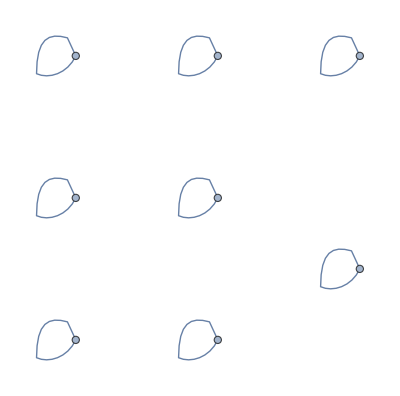
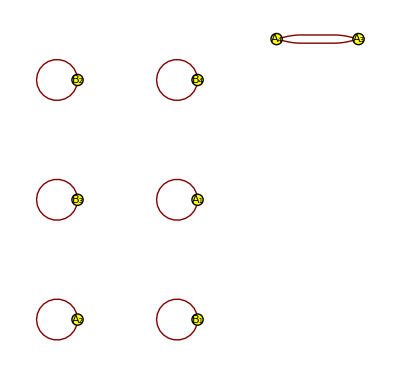
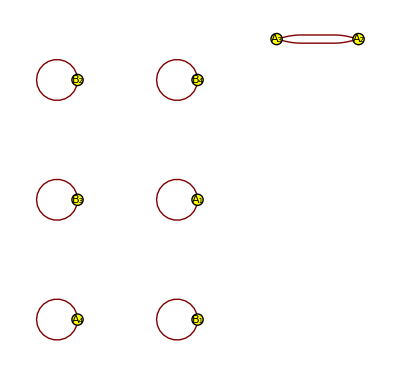
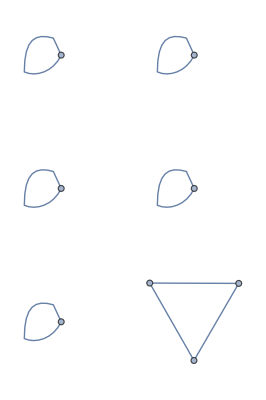
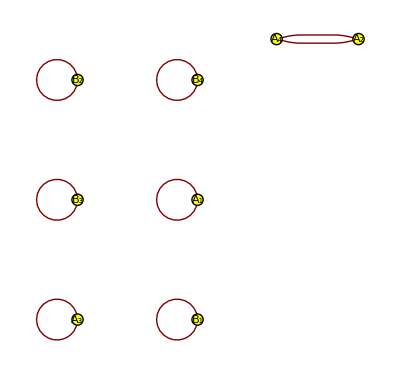
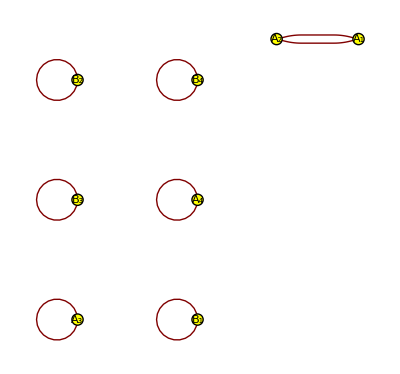
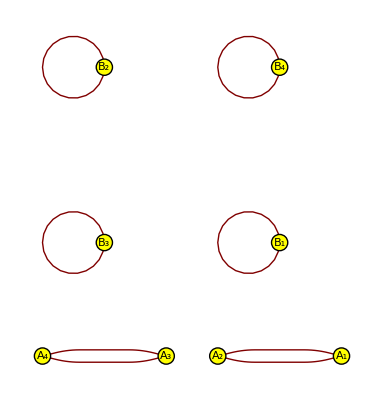
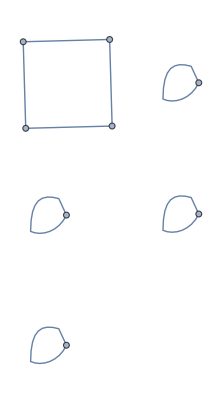
{{-Graphics-,ComplexInfinity},{-Graphics-,1/30},{-Graphics-,1/30},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,1/30},{-Graphics-,1/30},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,1/30},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,1/30},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,1/30},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,1/30},{-Graphics-,1/30},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,1/30},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,1/30},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,1/30},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,1/30},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,1/30},{-Graphics-,1/30},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,1/30},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,1/30},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,1/30},{-Graphics-,ComplexInfinity},{-Graphics-,1/30},{-Graphics-,1/30},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,1/30},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,1/30},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,1/30},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,1/30},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,1/30},{-Graphics-,1/30},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,1/30},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,1/30},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,1/30},{-Graphics-,1/30},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,1/30},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,1/30},{-Graphics-,1/30},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,1/30},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,1/30},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,1/30},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,1/30},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,1/30},{-Graphics-,1/30},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,1/30},{-Graphics-,1/30},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,1/30},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,1/30},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,1/30},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,1/30},{-Graphics-,1/30},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,1/30},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,1/30},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,1/30},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,1/30},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,1/30},{-Graphics-,1/30},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,1/30},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,1/30},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,1/30},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,1/30},{-Graphics-,1/30},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,1/30},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,1/30},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,1/30},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,1/30},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,1/30},{-Graphics-,1/30},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,1/30},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,1/30},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,1/30},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,1/30},{-Graphics-,1/30},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,1/30},{-Graphics-,1/30},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,1/30},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,1/30},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,1/30},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,1/30},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,1/30},{-Graphics-,1/30},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,1/30},{-Graphics-,1/30},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,1/30},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,1/30},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,1/30},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,1/30},{-Graphics-,1/30},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,1/30},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,1/30},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,1/30},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,1/30},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,1/30},{-Graphics-,1/30},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,1/30},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,1/30},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,1/30},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,1/30},{-Graphics-,1/30},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,1/30},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,1/30},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,1/30},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,1/30},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,1/30},{-Graphics-,1/30},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,1/30},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,1/30},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,1/30},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,1/30},{-Graphics-,1/30},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,1/30},{-Graphics-,1/30},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,1/30},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,1/30},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,1/30},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,1/30},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,1/30},{-Graphics-,1/30},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,1/30},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,1/30},{-Graphics-,1/30},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,1/30},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,1/30},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,1/30},{-Graphics-,1/30},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,1/30},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,1/30},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,1/30},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,1/30},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,1/30},{-Graphics-,1/30},{-Graphics-,ComplexInfinity},{-Graphics-,1/30},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,1/30},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,1/30},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,1/30},{-Graphics-,1/30},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,1/30},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,1/30},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,1/30},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,1/30},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,1/30},{-Graphics-,1/30},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,1/30},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,1/30},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,1/30},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,1/30},{-Graphics-,1/30},{-Graphics-,ComplexInfinity},{-Graphics-,ComplexInfinity},{-Graphics-,1/30},{-Graphics-,1/30},{-Graphics-,ComplexInfinity}}

```mathematica
visualizeTN[Out[24]]
```

```mathematica
MatrixForm[%29]
```

(-Graphics- | ComplexInfinity
-Graphics- | 1/30
-Graphics- | 1/30
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | 1/30
-Graphics- | 1/30
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | 1/30
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | 1/30
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | 1/30
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | 1/30
-Graphics- | 1/30
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | 1/30
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | 1/30
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | 1/30
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | 1/30
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | 1/30
-Graphics- | 1/30
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | 1/30
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | 1/30
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | 1/30
-Graphics- | ComplexInfinity
-Graphics- | 1/30
-Graphics- | 1/30
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | 1/30
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | 1/30
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | 1/30
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | 1/30
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | 1/30
-Graphics- | 1/30
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | 1/30
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | 1/30
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | 1/30
-Graphics- | 1/30
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | 1/30
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | 1/30
-Graphics- | 1/30
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | 1/30
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | 1/30
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | 1/30
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | 1/30
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | 1/30
-Graphics- | 1/30
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | 1/30
-Graphics- | 1/30
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | 1/30
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | 1/30
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | 1/30
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | 1/30
-Graphics- | 1/30
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | 1/30
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | 1/30
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | 1/30
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | 1/30
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | 1/30
-Graphics- | 1/30
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | 1/30
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | 1/30
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | 1/30
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | 1/30
-Graphics- | 1/30
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | 1/30
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | 1/30
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | 1/30
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | 1/30
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | 1/30
-Graphics- | 1/30
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | 1/30
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | 1/30
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | 1/30
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | 1/30
-Graphics- | 1/30
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | 1/30
-Graphics- | 1/30
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | 1/30
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | 1/30
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | 1/30
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | 1/30
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | 1/30
-Graphics- | 1/30
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | 1/30
-Graphics- | 1/30
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | 1/30
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | 1/30
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | 1/30
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | 1/30
-Graphics- | 1/30
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | 1/30
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | 1/30
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | 1/30
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | 1/30
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | 1/30
-Graphics- | 1/30
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | 1/30
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | 1/30
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | 1/30
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | 1/30
-Graphics- | 1/30
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | 1/30
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | 1/30
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | 1/30
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | 1/30
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | 1/30
-Graphics- | 1/30
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | 1/30
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | 1/30
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | 1/30
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | 1/30
-Graphics- | 1/30
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | 1/30
-Graphics- | 1/30
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | 1/30
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | 1/30
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | 1/30
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | 1/30
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | 1/30
-Graphics- | 1/30
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | 1/30
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | 1/30
-Graphics- | 1/30
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | 1/30
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | 1/30
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | 1/30
-Graphics- | 1/30
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | 1/30
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | 1/30
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | 1/30
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | 1/30
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | 1/30
-Graphics- | 1/30
-Graphics- | ComplexInfinity
-Graphics- | 1/30
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | 1/30
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | 1/30
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | 1/30
-Graphics- | 1/30
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | 1/30
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | 1/30
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | 1/30
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | 1/30
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | 1/30
-Graphics- | 1/30
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | 1/30
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | 1/30
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | 1/30
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | 1/30
-Graphics- | 1/30
-Graphics- | ComplexInfinity
-Graphics- | ComplexInfinity
-Graphics- | 1/30
-Graphics- | 1/30
-Graphics- | ComplexInfinity)

```mathematica
Dimensions[%29]
```

{576,2}

```mathematica
Last[{576,2}]
```

2

```mathematica
Range[2]
```

{1,2}

```mathematica
Last[{1,2}]
```

2